```mathematica
1.45773797371132511771853821938639576913034958372149298861250168621695251549917815691631008161325884963919740551883872783795346840404270157147580651970611179541626358994255981704216209413581741410543249^2
```

2.125

```mathematica
1.76776695296636881100211090526212259821208984422118509147084967248841559807763379856298441790955196591876730778864037128115604506981342151580515187137491978926652833240938199094474993812644097757571433^2
```

3.125

```mathematica
Expand[(8k+1)/8/.Solve[n==2k+1,k]]
```

{-3/8+n/2}

```mathematica
Table[(Solve[8l^2-(4n-3)==0,l][[2]][[1]][[2]]/.n->i)^2,{i,3,21,2}]
```

{9/8,17/8,25/8,33/8,41/8,49/8,57/8,65/8,73/8,81/8}

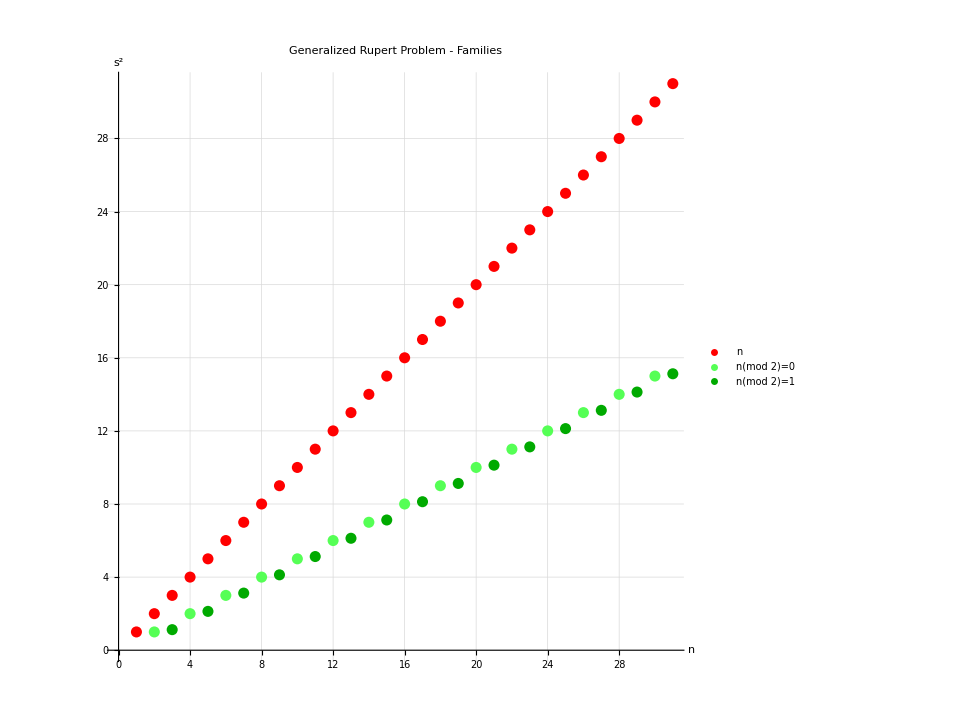

```mathematica
ListPlot[{Table[{n,n},{n,1,31}],Table[{n,n/2},{n,2,31,2}],Table[{n,n/2-3/8},{n,3,31,2}]},AspectRatio->1,GridLines->Automatic,PlotRange->{{0,Automatic},Automatic},PlotStyle->{Red,Lighter[Green],Darker[Green]},PlotLegends->{Placed[PointLegend[Automatic,{Style["n",18]},LegendLabel->Style["m = 1",18],LegendFunction->(Framed[#,Background->White,RoundingRadius->5]&),LegendMarkerSize->15],{0.88,0.95}],Placed[PointLegend[{Lighter[Green],Darker[Green]},{Style["n(mod 2)=0",18],Style["n(mod 2)=1",18]},LegendLabel->Style["m = 2",18],LegendFunction->(Framed[#,Background->White,RoundingRadius->5]&),LegendMarkerSize->15],{0.90,0.56}]},PlotLabel->Style["Generalized Rupert Problem - Families",24],AxesLabel->{Style["n",20],Style[s^2,20]}]
```

```mathematica
m0100 =Map[{#[[1]],#[[2]] #[[2]]}&,Map[ToExpression, ArrayReshape[Import["/Users/ligocki/Rupert/m01_00.txt","Words"],{100,3}]][[;;,2;;3]]];
```

```mathematica
m0200 =Map[{#[[1]],#[[2]] #[[2]]}&,Map[ToExpression, ArrayReshape[Import["/Users/ligocki/Rupert/m02_00.txt","Words"],{50,3}]][[;;,2;;3]]];
```

```mathematica
m0201 =Map[{#[[1]],#[[2]] #[[2]]}&,Map[ToExpression, ArrayReshape[Import["/Users/ligocki/Rupert/m02_01.txt","Words"],{49,3}]][[;;,2;;3]]];
```

```mathematica
m0300 =Map[{#[[1]],#[[2]] #[[2]]}&,Map[ToExpression, ArrayReshape[Import["/Users/ligocki/Rupert/m03_00.txt","Words"],{33,3}]][[;;,2;;3]]];
```

```mathematica
m0301 =Map[{#[[1]],#[[2]] #[[2]]}&,Map[ToExpression, ArrayReshape[Import["/Users/ligocki/Rupert/m03_01.txt","Words"],{16,3}]][[;;,2;;3]]];
```

```mathematica
m0302 =Map[{#[[1]],#[[2]] #[[2]]}&,Map[ToExpression, ArrayReshape[Import["/Users/ligocki/Rupert/m03_02.txt","Words"],{15,3}]][[;;,2;;3]]];
```

```mathematica
m0400 =Map[{#[[1]],#[[2]] #[[2]]}&,Map[ToExpression, ArrayReshape[Import["/Users/ligocki/Rupert/m04_00.txt","Words"],{25,3}]][[;;,2;;3]]];
```

```mathematica
m0401 =Map[{#[[1]],#[[2]] #[[2]]}&,Map[ToExpression, ArrayReshape[Import["/Users/ligocki/Rupert/m04_01.txt","Words"],{12,3}]][[;;,2;;3]]];
```

```mathematica
m0402 =Map[{#[[1]],#[[2]] #[[2]]}&,Map[ToExpression, ArrayReshape[Import["/Users/ligocki/Rupert/m04_02.txt","Words"],{24,3}]][[;;,2;;3]]];
```

```mathematica
m0403 =Map[{#[[1]],#[[2]] #[[2]]}&,Map[ToExpression, ArrayReshape[Import["/Users/ligocki/Rupert/m04_03.txt","Words"],{11,3}]][[;;,2;;3]]];
```

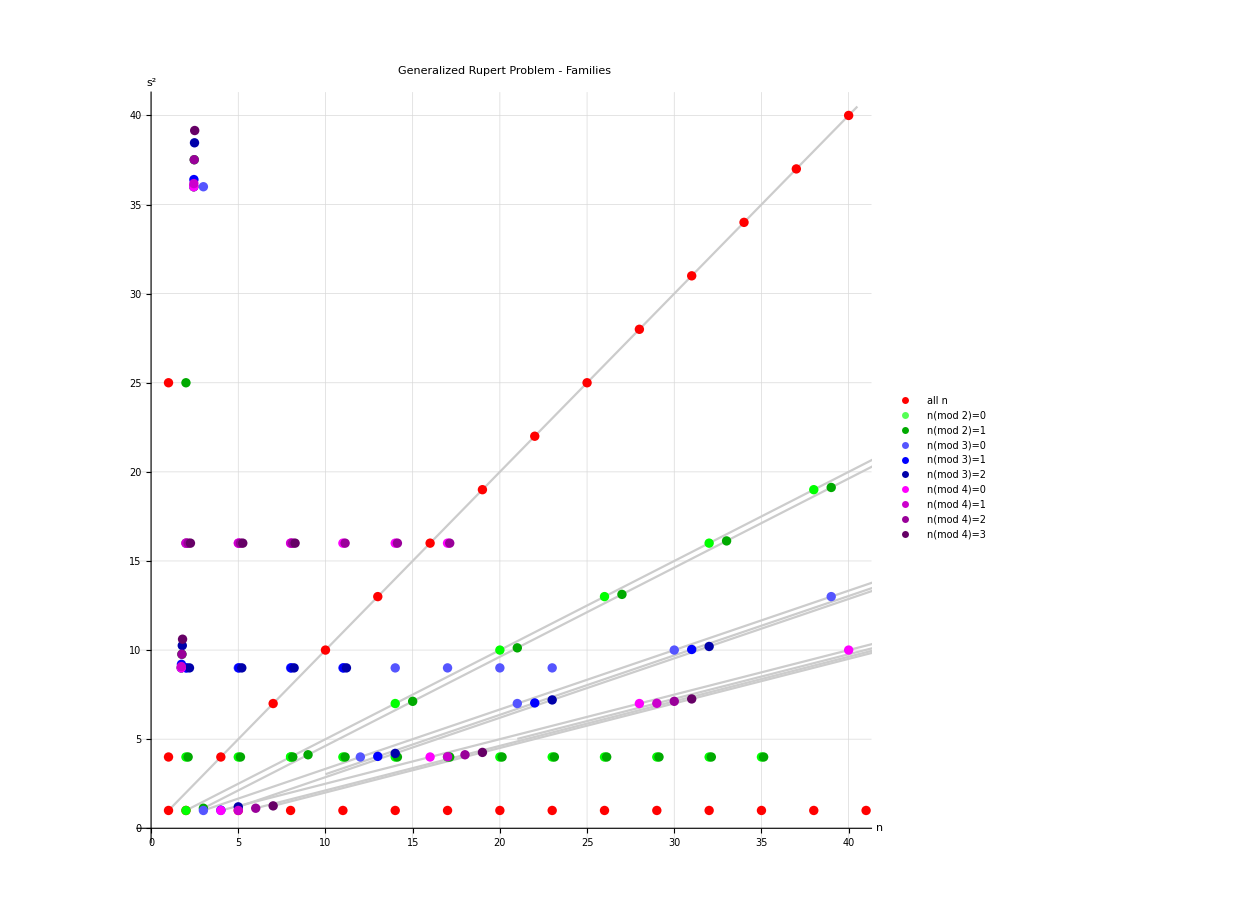

```mathematica
Show[Plot[{x},{x,1,50},PlotStyle->RGBColor[0.8,0.8,0.8],AspectRatio->1,GridLines->Automatic,PlotRange->{{0,40.5},{0,40.5}},PlotLegends->{Placed[PointLegend[{Red},{Style["all n",12]},LegendLabel->Style["m = 1",12],LegendFunction->(Framed[#,Background->White,RoundingRadius->5]&),LegendMarkerSize->10],{0.25,0.94}],Placed[PointLegend[{Lighter[Green],Darker[Green]},{Style["n(mod 2)=0",12],Style["n(mod 2)=1",12]},LegendLabel->Style["m = 2",12],LegendFunction->(Framed[#,Background->White,RoundingRadius->5]&),LegendMarkerSize->10],{0.25,0.86}],Placed[PointLegend[{Lighter[Blue],Blue,Darker[Blue]},{Style["n(mod 3)=0",12],Style["n(mod 3)=1",12],Style["n(mod 3)=2",12]},LegendLabel->Style["m = 3",12],LegendFunction->(Framed[#,Background->White,RoundingRadius->5]&),LegendMarkerSize->10],{0.25,0.755}],Placed[PointLegend[{RGBColor[1,0,1],RGBColor[0.8,0,0.8],RGBColor[0.6,0,0.6],RGBColor[0.4,0,0.4]},{Style["n(mod 4)=0",12],Style["n(mod 4)=1",12],Style["n(mod 4)=2",12],Style["n(mod 4)=3",12]},LegendLabel->Style["m = 4",12],LegendFunction->(Framed[#,Background->White,RoundingRadius->5]&),LegendMarkerSize->10],{0.25,0.626}]},PlotLabel->Style["Generalized Rupert Problem - Families",24],AxesLabel->{Style["n",20],Style[s^2,20]}],Plot[{x/2-0.000000},{x,2,50},PlotStyle->RGBColor[0.8,0.8,0.8]],Plot[{x/2-0.375000},{x,3,50},PlotStyle->RGBColor[0.8,0.8,0.8]],Plot[{x/3-0.000000},{x,3,50},PlotStyle->RGBColor[0.8,0.8,0.8]],Plot[{x/3-0.299962},{x,10,50},PlotStyle->RGBColor[0.8,0.8,0.8]],Plot[{x/3-0.464625},{x,5,50},PlotStyle->RGBColor[0.8,0.8,0.8]],Plot[{x/4-0.000000},{x,4,50},PlotStyle->RGBColor[0.8,0.8,0.8]],Plot[{x/4-0.235281},{x,21,50},PlotStyle->RGBColor[0.8,0.8,0.8]],Plot[{x/4-0.375000},{x,6,50},PlotStyle->RGBColor[0.8,0.8,0.8]],Plot[{x/4-0.492640},{x,7,50},PlotStyle->RGBColor[0.8,0.8,0.8]],ListPlot[{m0100,m0200,m0201,m0300,m0301,m0302,m0400,m0401,m0402,m0403},PlotStyle->{Red,Green,Darker[Green],Lighter[Blue],Blue,Darker[Blue],RGBColor[1,0,1],RGBColor[0.8,0,0.8],RGBColor[0.6,0,0.6],RGBColor[0.4,0,0.4]}]]
```

```mathematica
Export["/Users/ligocki/Rupert/Results01.png",%256,"PNG"]
```

/Users/ligocki/Rupert/Results01.png

```mathematica
Export["/Users/ligocki/Rupert/Rupert01.pdf",%239,"PDF"]
```

/Users/ligocki/Rupert/Rupert01.pdf

```mathematica
Export["/Users/ligocki/Rupert/Results01.png",%239,"PNG"]
```

/Users/ligocki/Rupert/Results01.png

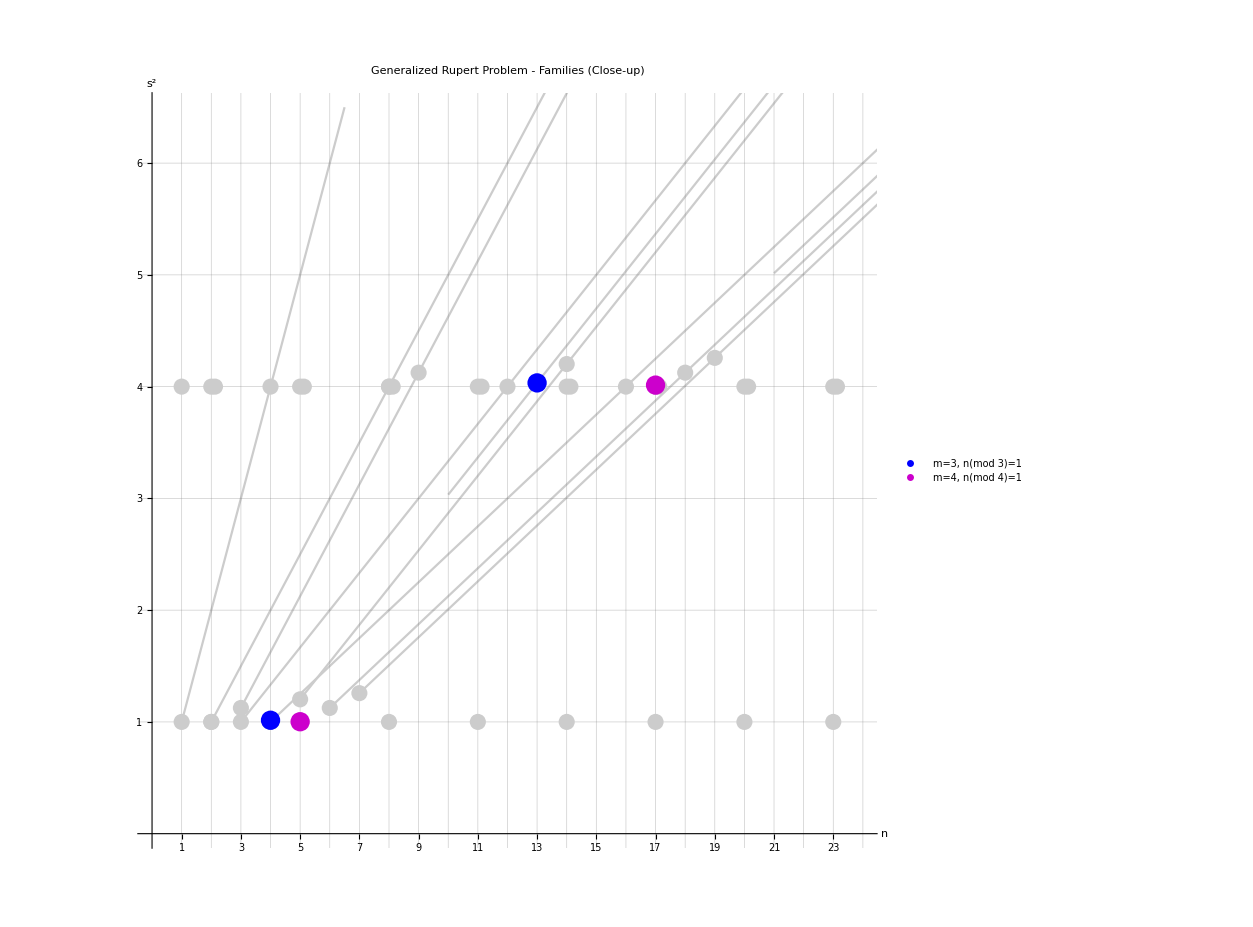

```mathematica
xmax=24;ymax=6.5;Show[Plot[{x},{x,1,50},PlotStyle->RGBColor[0.8,0.8,0.8],AspectRatio->1,Ticks->{Range[xmax],Range[ymax]},PlotRange->{{0,xmax},{0,ymax}},GridLines->{Range[xmax],Range[ymax]},PlotLegends->{Placed[PointLegend[{Blue,RGBColor[0.8,0,0.8]},{Style["m=3, n(mod 3)=1",12],Style["m=4, n(mod 4)=1",12]},LegendFunction->(Framed[#,Background->White,RoundingRadius->5]&),LegendMarkerSize->22.5],{0.8,0.4}]},PlotLabel->Style["Generalized Rupert Problem - Families (Close-up)",24],AxesLabel->{Style["n",20],Style[s^2,20]}],Plot[{x/2-0.000000},{x,2,50},PlotStyle->RGBColor[0.8,0.8,0.8]],Plot[{x/2-0.375000},{x,3,50},PlotStyle->RGBColor[0.8,0.8,0.8]],Plot[{x/3-0.000000},{x,3,50},PlotStyle->RGBColor[0.8,0.8,0.8]],Plot[{x/3-0.299962},{x,10,50},PlotStyle->RGBColor[0.8,0.8,0.8]],Plot[{x/3-0.464625},{x,5,50},PlotStyle->RGBColor[0.8,0.8,0.8]],Plot[{x/4-0.000000},{x,4,50},PlotStyle->RGBColor[0.8,0.8,0.8]],Plot[{x/4-0.235281},{x,21,50},PlotStyle->RGBColor[0.8,0.8,0.8]],Plot[{x/4-0.375000},{x,6,50},PlotStyle->RGBColor[0.8,0.8,0.8]],Plot[{x/4-0.492640},{x,7,50},PlotStyle->RGBColor[0.8,0.8,0.8]],ListPlot[{m0100,m0200,m0201,m0300,m0301,m0302,m0400,m0401,m0402,m0403},PlotStyle->{{pc,ps},{pc,ps},{pc,ps},{pc,ps},{Blue,ps},{pc,ps},{pc,ps},{RGBColor[0.8,0,0.8],ps},{pc,ps},{pc,ps}}/.{ps->PointSize[0.0125],pc->RGBColor[0.8,0.8,0.8]}],ListPlot[{m0301,m0401},PlotStyle->{{Blue,ps},{RGBColor[0.8,0,0.8],ps}}/.{ps->PointSize[0.015]}]]
```

```mathematica
dof[m_,n_]:=(n(n-1)/2)-((n-m)(n-m-1)/2)
```

```mathematica
dof[3,7]
```

15

```mathematica
dof[3,10]
```

24

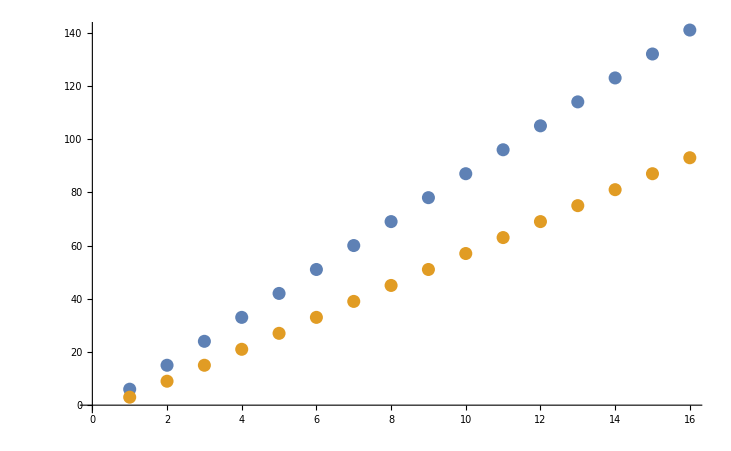

```mathematica
ListPlot[{Table[dof[3,n],{n,4,50,3}],Table[dof[3,n]-(n-1),{n,4,50,3}]}]
```

```mathematica
Collect[Simplify[dof[m,n]],n]
```

-1/2 m (1+m)+m n

```mathematica
Collect[Simplify[dof[m,n]-(n-1)],n]
```

-1/2 (-1+m) (2+m)+(-1+m) n

```mathematica
Collect[Simplify[dof[3,n]],n]
```

-6+3 n

```mathematica
Collect[Simplify[dof[3,n]-(n-1)],n]
```

-5+2 n

```mathematica
Table[{n,dof[3,n],dof[3,n]-(n-1)},{n,4,50,3}]//MatrixForm
```

(4 | 6 | 3
7 | 15 | 9
10 | 24 | 15
13 | 33 | 21
16 | 42 | 27
19 | 51 | 33
22 | 60 | 39
25 | 69 | 45
28 | 78 | 51
31 | 87 | 57
34 | 96 | 63
37 | 105 | 69
40 | 114 | 75
43 | 123 | 81
46 | 132 | 87
49 | 141 | 93)

```mathematica
m003010:={{0,a,0,m14,m15,m16,m17,m18,m19,m110},{0,a,0,m24,m25,m26,m27,m28,m29,m210},{0,a,0,m34,m35,m36,m37,m38,m39,m310},{0,0,a,m44,m45,m46,m47,m48,m49,m410},{0,0,a,m54,m55,m56,m57,m58,m59,m510},{0,0,a,m64,m65,m66,m67,m68,m69,m610},{b,(a-b),0,m74,m75,m76,m77,m78,m79,m710},{b,-(a-b),0,m84,m85,m86,m87,m88,m89,m810},{b,0,(a-b),m94,m95,m96,m97,m98,m99,m910},{b,0,-(a-b),m104,m105,m106,m107,m108,m109,m1010}}
```

```mathematica
m003010//MatrixForm
```

(0 | a | 0 | m14 | m15 | m16 | m17 | m18 | m19 | m110
0 | a | 0 | m24 | m25 | m26 | m27 | m28 | m29 | m210
0 | a | 0 | m34 | m35 | m36 | m37 | m38 | m39 | m310
0 | 0 | a | m44 | m45 | m46 | m47 | m48 | m49 | m410
0 | 0 | a | m54 | m55 | m56 | m57 | m58 | m59 | m510
0 | 0 | a | m64 | m65 | m66 | m67 | m68 | m69 | m610
b | a-b | 0 | m74 | m75 | m76 | m77 | m78 | m79 | m710
b | -a+b | 0 | m84 | m85 | m86 | m87 | m88 | m89 | m810
b | 0 | a-b | m94 | m95 | m96 | m97 | m98 | m99 | m910
b | 0 | -a+b | m104 | m105 | m106 | m107 | m108 | m109 | m1010)

```mathematica
cons003010:=m003010.Transpose[m003010]
```

```mathematica
cons003010//MatrixForm
```

(a^2+m110^2+m14^2+m15^2+m16^2+m17^2+m18^2+m19^2 | a^2+m110 m210+m14 m24+m15 m25+m16 m26+m17 m27+m18 m28+m19 m29 | a^2+m110 m310+m14 m34+m15 m35+m16 m36+m17 m37+m18 m38+m19 m39 | m110 m410+m14 m44+m15 m45+m16 m46+m17 m47+m18 m48+m19 m49 | m110 m510+m14 m54+m15 m55+m16 m56+m17 m57+m18 m58+m19 m59 | m110 m610+m14 m64+m15 m65+m16 m66+m17 m67+m18 m68+m19 m69 | a (a-b)+m110 m710+m14 m74+m15 m75+m16 m76+m17 m77+m18 m78+m19 m79 | a (-a+b)+m110 m810+m14 m84+m15 m85+m16 m86+m17 m87+m18 m88+m19 m89 | m110 m910+m14 m94+m15 m95+m16 m96+m17 m97+m18 m98+m19 m99 | m1010 m110+m104 m14+m105 m15+m106 m16+m107 m17+m108 m18+m109 m19
a^2+m110 m210+m14 m24+m15 m25+m16 m26+m17 m27+m18 m28+m19 m29 | a^2+m210^2+m24^2+m25^2+m26^2+m27^2+m28^2+m29^2 | a^2+m210 m310+m24 m34+m25 m35+m26 m36+m27 m37+m28 m38+m29 m39 | m210 m410+m24 m44+m25 m45+m26 m46+m27 m47+m28 m48+m29 m49 | m210 m510+m24 m54+m25 m55+m26 m56+m27 m57+m28 m58+m29 m59 | m210 m610+m24 m64+m25 m65+m26 m66+m27 m67+m28 m68+m29 m69 | a (a-b)+m210 m710+m24 m74+m25 m75+m26 m76+m27 m77+m28 m78+m29 m79 | a (-a+b)+m210 m810+m24 m84+m25 m85+m26 m86+m27 m87+m28 m88+m29 m89 | m210 m910+m24 m94+m25 m95+m26 m96+m27 m97+m28 m98+m29 m99 | m1010 m210+m104 m24+m105 m25+m106 m26+m107 m27+m108 m28+m109 m29
a^2+m110 m310+m14 m34+m15 m35+m16 m36+m17 m37+m18 m38+m19 m39 | a^2+m210 m310+m24 m34+m25 m35+m26 m36+m27 m37+m28 m38+m29 m39 | a^2+m310^2+m34^2+m35^2+m36^2+m37^2+m38^2+m39^2 | m310 m410+m34 m44+m35 m45+m36 m46+m37 m47+m38 m48+m39 m49 | m310 m510+m34 m54+m35 m55+m36 m56+m37 m57+m38 m58+m39 m59 | m310 m610+m34 m64+m35 m65+m36 m66+m37 m67+m38 m68+m39 m69 | a (a-b)+m310 m710+m34 m74+m35 m75+m36 m76+m37 m77+m38 m78+m39 m79 | a (-a+b)+m310 m810+m34 m84+m35 m85+m36 m86+m37 m87+m38 m88+m39 m89 | m310 m910+m34 m94+m35 m95+m36 m96+m37 m97+m38 m98+m39 m99 | m1010 m310+m104 m34+m105 m35+m106 m36+m107 m37+m108 m38+m109 m39
m110 m410+m14 m44+m15 m45+m16 m46+m17 m47+m18 m48+m19 m49 | m210 m410+m24 m44+m25 m45+m26 m46+m27 m47+m28 m48+m29 m49 | m310 m410+m34 m44+m35 m45+m36 m46+m37 m47+m38 m48+m39 m49 | a^2+m410^2+m44^2+m45^2+m46^2+m47^2+m48^2+m49^2 | a^2+m410 m510+m44 m54+m45 m55+m46 m56+m47 m57+m48 m58+m49 m59 | a^2+m410 m610+m44 m64+m45 m65+m46 m66+m47 m67+m48 m68+m49 m69 | m410 m710+m44 m74+m45 m75+m46 m76+m47 m77+m48 m78+m49 m79 | m410 m810+m44 m84+m45 m85+m46 m86+m47 m87+m48 m88+m49 m89 | a (a-b)+m410 m910+m44 m94+m45 m95+m46 m96+m47 m97+m48 m98+m49 m99 | a (-a+b)+m1010 m410+m104 m44+m105 m45+m106 m46+m107 m47+m108 m48+m109 m49
m110 m510+m14 m54+m15 m55+m16 m56+m17 m57+m18 m58+m19 m59 | m210 m510+m24 m54+m25 m55+m26 m56+m27 m57+m28 m58+m29 m59 | m310 m510+m34 m54+m35 m55+m36 m56+m37 m57+m38 m58+m39 m59 | a^2+m410 m510+m44 m54+m45 m55+m46 m56+m47 m57+m48 m58+m49 m59 | a^2+m510^2+m54^2+m55^2+m56^2+m57^2+m58^2+m59^2 | a^2+m510 m610+m54 m64+m55 m65+m56 m66+m57 m67+m58 m68+m59 m69 | m510 m710+m54 m74+m55 m75+m56 m76+m57 m77+m58 m78+m59 m79 | m510 m810+m54 m84+m55 m85+m56 m86+m57 m87+m58 m88+m59 m89 | a (a-b)+m510 m910+m54 m94+m55 m95+m56 m96+m57 m97+m58 m98+m59 m99 | a (-a+b)+m1010 m510+m104 m54+m105 m55+m106 m56+m107 m57+m108 m58+m109 m59
m110 m610+m14 m64+m15 m65+m16 m66+m17 m67+m18 m68+m19 m69 | m210 m610+m24 m64+m25 m65+m26 m66+m27 m67+m28 m68+m29 m69 | m310 m610+m34 m64+m35 m65+m36 m66+m37 m67+m38 m68+m39 m69 | a^2+m410 m610+m44 m64+m45 m65+m46 m66+m47 m67+m48 m68+m49 m69 | a^2+m510 m610+m54 m64+m55 m65+m56 m66+m57 m67+m58 m68+m59 m69 | a^2+m610^2+m64^2+m65^2+m66^2+m67^2+m68^2+m69^2 | m610 m710+m64 m74+m65 m75+m66 m76+m67 m77+m68 m78+m69 m79 | m610 m810+m64 m84+m65 m85+m66 m86+m67 m87+m68 m88+m69 m89 | a (a-b)+m610 m910+m64 m94+m65 m95+m66 m96+m67 m97+m68 m98+m69 m99 | a (-a+b)+m1010 m610+m104 m64+m105 m65+m106 m66+m107 m67+m108 m68+m109 m69
a (a-b)+m110 m710+m14 m74+m15 m75+m16 m76+m17 m77+m18 m78+m19 m79 | a (a-b)+m210 m710+m24 m74+m25 m75+m26 m76+m27 m77+m28 m78+m29 m79 | a (a-b)+m310 m710+m34 m74+m35 m75+m36 m76+m37 m77+m38 m78+m39 m79 | m410 m710+m44 m74+m45 m75+m46 m76+m47 m77+m48 m78+m49 m79 | m510 m710+m54 m74+m55 m75+m56 m76+m57 m77+m58 m78+m59 m79 | m610 m710+m64 m74+m65 m75+m66 m76+m67 m77+m68 m78+m69 m79 | (a-b)^2+b^2+m710^2+m74^2+m75^2+m76^2+m77^2+m78^2+m79^2 | b^2+(a-b) (-a+b)+m710 m810+m74 m84+m75 m85+m76 m86+m77 m87+m78 m88+m79 m89 | b^2+m710 m910+m74 m94+m75 m95+m76 m96+m77 m97+m78 m98+m79 m99 | b^2+m1010 m710+m104 m74+m105 m75+m106 m76+m107 m77+m108 m78+m109 m79
a (-a+b)+m110 m810+m14 m84+m15 m85+m16 m86+m17 m87+m18 m88+m19 m89 | a (-a+b)+m210 m810+m24 m84+m25 m85+m26 m86+m27 m87+m28 m88+m29 m89 | a (-a+b)+m310 m810+m34 m84+m35 m85+m36 m86+m37 m87+m38 m88+m39 m89 | m410 m810+m44 m84+m45 m85+m46 m86+m47 m87+m48 m88+m49 m89 | m510 m810+m54 m84+m55 m85+m56 m86+m57 m87+m58 m88+m59 m89 | m610 m810+m64 m84+m65 m85+m66 m86+m67 m87+m68 m88+m69 m89 | b^2+(a-b) (-a+b)+m710 m810+m74 m84+m75 m85+m76 m86+m77 m87+m78 m88+m79 m89 | b^2+(-a+b)^2+m810^2+m84^2+m85^2+m86^2+m87^2+m88^2+m89^2 | b^2+m810 m910+m84 m94+m85 m95+m86 m96+m87 m97+m88 m98+m89 m99 | b^2+m1010 m810+m104 m84+m105 m85+m106 m86+m107 m87+m108 m88+m109 m89
m110 m910+m14 m94+m15 m95+m16 m96+m17 m97+m18 m98+m19 m99 | m210 m910+m24 m94+m25 m95+m26 m96+m27 m97+m28 m98+m29 m99 | m310 m910+m34 m94+m35 m95+m36 m96+m37 m97+m38 m98+m39 m99 | a (a-b)+m410 m910+m44 m94+m45 m95+m46 m96+m47 m97+m48 m98+m49 m99 | a (a-b)+m510 m910+m54 m94+m55 m95+m56 m96+m57 m97+m58 m98+m59 m99 | a (a-b)+m610 m910+m64 m94+m65 m95+m66 m96+m67 m97+m68 m98+m69 m99 | b^2+m710 m910+m74 m94+m75 m95+m76 m96+m77 m97+m78 m98+m79 m99 | b^2+m810 m910+m84 m94+m85 m95+m86 m96+m87 m97+m88 m98+m89 m99 | (a-b)^2+b^2+m910^2+m94^2+m95^2+m96^2+m97^2+m98^2+m99^2 | b^2+(a-b) (-a+b)+m1010 m910+m104 m94+m105 m95+m106 m96+m107 m97+m108 m98+m109 m99
m1010 m110+m104 m14+m105 m15+m106 m16+m107 m17+m108 m18+m109 m19 | m1010 m210+m104 m24+m105 m25+m106 m26+m107 m27+m108 m28+m109 m29 | m1010 m310+m104 m34+m105 m35+m106 m36+m107 m37+m108 m38+m109 m39 | a (-a+b)+m1010 m410+m104 m44+m105 m45+m106 m46+m107 m47+m108 m48+m109 m49 | a (-a+b)+m1010 m510+m104 m54+m105 m55+m106 m56+m107 m57+m108 m58+m109 m59 | a (-a+b)+m1010 m610+m104 m64+m105 m65+m106 m66+m107 m67+m108 m68+m109 m69 | b^2+m1010 m710+m104 m74+m105 m75+m106 m76+m107 m77+m108 m78+m109 m79 | b^2+m1010 m810+m104 m84+m105 m85+m106 m86+m107 m87+m108 m88+m109 m89 | b^2+(a-b) (-a+b)+m1010 m910+m104 m94+m105 m95+m106 m96+m107 m97+m108 m98+m109 m99 | b^2+(-a+b)^2+m1010^2+m104^2+m105^2+m106^2+m107^2+m108^2+m109^2)

```mathematica
Table[Simplify[cons003010[[i,i]]==1],{i,1,10}]//MatrixForm
```

(a^2+m110^2+m14^2+m15^2+m16^2+m17^2+m18^2+m19^2==1
a^2+m210^2+m24^2+m25^2+m26^2+m27^2+m28^2+m29^2==1
a^2+m310^2+m34^2+m35^2+m36^2+m37^2+m38^2+m39^2==1
a^2+m410^2+m44^2+m45^2+m46^2+m47^2+m48^2+m49^2==1
a^2+m510^2+m54^2+m55^2+m56^2+m57^2+m58^2+m59^2==1
a^2+m610^2+m64^2+m65^2+m66^2+m67^2+m68^2+m69^2==1
(a-b)^2+b^2+m710^2+m74^2+m75^2+m76^2+m77^2+m78^2+m79^2==1
(a-b)^2+b^2+m810^2+m84^2+m85^2+m86^2+m87^2+m88^2+m89^2==1
(a-b)^2+b^2+m910^2+m94^2+m95^2+m96^2+m97^2+m98^2+m99^2==1
(a-b)^2+b^2+m1010^2+m104^2+m105^2+m106^2+m107^2+m108^2+m109^2==1)

```mathematica
Timing[Solve[Join[Table[cons003010[[i,i]]==1,{i,1,10}]]][[1]]//MatrixForm]
```

{0.558755,(m109→-√(1-a^2+2 a b-2 b^2-m1010^2-m104^2-m105^2-m106^2-m107^2-m108^2)
m19→-√(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2)
m29→-√(1-a^2-m210^2-m24^2-m25^2-m26^2-m27^2-m28^2)
m39→-√(1-a^2-m310^2-m34^2-m35^2-m36^2-m37^2-m38^2)
m49→-√(1-a^2-m410^2-m44^2-m45^2-m46^2-m47^2-m48^2)
m59→-√(1-a^2-m510^2-m54^2-m55^2-m56^2-m57^2-m58^2)
m69→-√(1-a^2-m610^2-m64^2-m65^2-m66^2-m67^2-m68^2)
m79→-√(1-a^2+2 a b-2 b^2-m710^2-m74^2-m75^2-m76^2-m77^2-m78^2)
m89→-√(1-a^2+2 a b-2 b^2-m810^2-m84^2-m85^2-m86^2-m87^2-m88^2)
m99→-√(1-a^2+2 a b-2 b^2-m910^2-m94^2-m95^2-m96^2-m97^2-m98^2))}

```mathematica
Table[Simplify[cons003010[[1,i]]==If[i==1,1,0]],{i,1,10}]//MatrixForm
```

(a^2+m110^2+m14^2+m15^2+m16^2+m17^2+m18^2+m19^2==1
a^2+m110 m210+m14 m24+m15 m25+m16 m26+m17 m27+m18 m28+m19 m29==0
a^2+m110 m310+m14 m34+m15 m35+m16 m36+m17 m37+m18 m38+m19 m39==0
m110 m410+m14 m44+m15 m45+m16 m46+m17 m47+m18 m48+m19 m49==0
m110 m510+m14 m54+m15 m55+m16 m56+m17 m57+m18 m58+m19 m59==0
m110 m610+m14 m64+m15 m65+m16 m66+m17 m67+m18 m68+m19 m69==0
a^2+m110 m710+m14 m74+m15 m75+m16 m76+m17 m77+m18 m78+m19 m79==a b
a^2==a b+m110 m810+m14 m84+m15 m85+m16 m86+m17 m87+m18 m88+m19 m89
m110 m910+m14 m94+m15 m95+m16 m96+m17 m97+m18 m98+m19 m99==0
m1010 m110+m104 m14+m105 m15+m106 m16+m107 m17+m108 m18+m109 m19==0)

```mathematica
Timing[Solve[Table[Simplify[cons003010[[1,i]]==If[i==1,1,0]],{i,1,10}],{m19,m29,m39,m49,m59,m69,m79,m89,m99,m109}][[1]]//MatrixForm]
```

{0.116563,(m19→-√(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2)
m29→(-a^2 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2)-m110 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m210-m14 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m24-m15 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m25-m16 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m26-m17 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m27-m18 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m28)/(-1+a^2+m110^2+m14^2+m15^2+m16^2+m17^2+m18^2)
m39→(-a^2 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2)-m110 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m310-m14 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m34-m15 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m35-m16 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m36-m17 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m37-m18 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m38)/(-1+a^2+m110^2+m14^2+m15^2+m16^2+m17^2+m18^2)
m49→(-m110 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m410-m14 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m44-m15 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m45-m16 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m46-m17 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m47-m18 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m48)/(-1+a^2+m110^2+m14^2+m15^2+m16^2+m17^2+m18^2)
m59→(-m110 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m510-m14 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m54-m15 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m55-m16 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m56-m17 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m57-m18 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m58)/(-1+a^2+m110^2+m14^2+m15^2+m16^2+m17^2+m18^2)
m69→(-m110 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m610-m14 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m64-m15 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m65-m16 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m66-m17 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m67-m18 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m68)/(-1+a^2+m110^2+m14^2+m15^2+m16^2+m17^2+m18^2)
m79→(a^2 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2)-a b √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2)+m110 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m710+m14 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m74+m15 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m75+m16 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m76+m17 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m77+m18 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m78)/(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2)
m89→(a^2 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2)-a b √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2)-m110 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m810-m14 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m84-m15 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m85-m16 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m86-m17 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m87-m18 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m88)/(-1+a^2+m110^2+m14^2+m15^2+m16^2+m17^2+m18^2)
m99→(-m110 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m910-m14 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m94-m15 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m95-m16 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m96-m17 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m97-m18 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2) m98)/(-1+a^2+m110^2+m14^2+m15^2+m16^2+m17^2+m18^2)
m109→(-m1010 m110 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2)-m104 m14 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2)-m105 m15 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2)-m106 m16 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2)-m107 m17 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2)-m108 m18 √(1-a^2-m110^2-m14^2-m15^2-m16^2-m17^2-m18^2))/(-1+a^2+m110^2+m14^2+m15^2+m16^2+m17^2+m18^2))}

```mathematica
Join[Table[cons003010[[1,i]]==If[i==1,1,0],{i,1,2}],Table[cons003010[[2,i]]==If[i==2,1,0],{i,2,2}],Table[cons003010[[3,i]]==If[i==3,1,0],{i,3,3}]]//MatrixForm
```

(a^2+m110^2+m14^2+m15^2+m16^2+m17^2+m18^2+m19^2==1
a^2+m110 m210+m14 m24+m15 m25+m16 m26+m17 m27+m18 m28+m19 m29==0
a^2+m210^2+m24^2+m25^2+m26^2+m27^2+m28^2+m29^2==1
a^2+m310^2+m34^2+m35^2+m36^2+m37^2+m38^2+m39^2==1)

```mathematica
Timing[Solve[Join[Table[cons003010[[1,i]]==If[i==1,1,0],{i,1,2}],Table[cons003010[[2,i]]==If[i==2,1,0],{i,2,2}],Table[cons003010[[3,i]]==If[i==3,1,0],{i,3,3}]]][[1]]//MatrixForm]
```

{30.2005,(m110→-√(1-a^2-m14^2-m15^2-m16^2-m17^2-m18^2-m19^2)
m28→(-2 a^2 m18+2 m18 √(1-a^2-m14^2-m15^2-m16^2-m17^2-m18^2-m19^2) m210-2 m14 m18 m24-2 m15 m18 m25-2 m16 m18 m26-2 m17 m18 m27-√((2 a^2 m18-2 m18 √(1-a^2-m14^2-m15^2-m16^2-m17^2-m18^2-m19^2) m210+2 m14 m18 m24+2 m15 m18 m25+2 m16 m18 m26+2 m17 m18 m27)^2-4 (m18^2+m19^2) (a^4-m19^2+a^2 m19^2-2 a^2 √(1-a^2-m14^2-m15^2-m16^2-m17^2-m18^2-m19^2) m210+m210^2-a^2 m210^2-m14^2 m210^2-m15^2 m210^2-m16^2 m210^2-m17^2 m210^2-m18^2 m210^2+2 a^2 m14 m24-2 m14 √(1-a^2-m14^2-m15^2-m16^2-m17^2-m18^2-m19^2) m210 m24+m14^2 m24^2+m19^2 m24^2+2 a^2 m15 m25-2 m15 √(1-a^2-m14^2-m15^2-m16^2-m17^2-m18^2-m19^2) m210 m25+2 m14 m15 m24 m25+m15^2 m25^2+m19^2 m25^2+2 a^2 m16 m26-2 m16 √(1-a^2-m14^2-m15^2-m16^2-m17^2-m18^2-m19^2) m210 m26+2 m14 m16 m24 m26+2 m15 m16 m25 m26+m16^2 m26^2+m19^2 m26^2+2 a^2 m17 m27-2 m17 √(1-a^2-m14^2-m15^2-m16^2-m17^2-m18^2-m19^2) m210 m27+2 m14 m17 m24 m27+2 m15 m17 m25 m27+2 m16 m17 m26 m27+m17^2 m27^2+m19^2 m27^2)))/(2 (m18^2+m19^2))
m29→(-a^2+(a^2 m18^2)/(m18^2+m19^2)+√(1-a^2-m14^2-m15^2-m16^2-m17^2-m18^2-m19^2) m210-(m18^2 √(1-a^2-m14^2-m15^2-m16^2-m17^2-m18^2-m19^2) m210)/(m18^2+m19^2)-m14 m24+(m14 m18^2 m24)/(m18^2+m19^2)-m15 m25+(m15 m18^2 m25)/(m18^2+m19^2)-m16 m26+(m16 m18^2 m26)/(m18^2+m19^2)-m17 m27+(m17 m18^2 m27)/(m18^2+m19^2)+(m18 √((2 a^2 m18-2 m18 √(1-a^2-m14^2-m15^2-m16^2-m17^2-m18^2-m19^2) m210+2 m14 m18 m24+2 m15 m18 m25+2 m16 m18 m26+2 m17 m18 m27)^2-4 (m18^2+m19^2) (a^4-m19^2+a^2 m19^2-2 a^2 √(1-a^2-m14^2-m15^2-m16^2-m17^2-m18^2-m19^2) m210+m210^2-a^2 m210^2-m14^2 m210^2-m15^2 m210^2-m16^2 m210^2-m17^2 m210^2-m18^2 m210^2+2 a^2 m14 m24-2 m14 √(1-a^2-m14^2-m15^2-m16^2-m17^2-m18^2-m19^2) m210 m24+m14^2 m24^2+m19^2 m24^2+2 a^2 m15 m25-2 m15 √(1-a^2-m14^2-m15^2-m16^2-m17^2-m18^2-m19^2) m210 m25+2 m14 m15 m24 m25+m15^2 m25^2+m19^2 m25^2+2 a^2 m16 m26-2 m16 √(1-a^2-m14^2-m15^2-m16^2-m17^2-m18^2-m19^2) m210 m26+2 m14 m16 m24 m26+2 m15 m16 m25 m26+m16^2 m26^2+m19^2 m26^2+2 a^2 m17 m27-2 m17 √(1-a^2-m14^2-m15^2-m16^2-m17^2-m18^2-m19^2) m210 m27+2 m14 m17 m24 m27+2 m15 m17 m25 m27+2 m16 m17 m26 m27+m17^2 m27^2+m19^2 m27^2)))/(2 (m18^2+m19^2)))/m19
m39→-√(1-a^2-m310^2-m34^2-m35^2-m36^2-m37^2-m38^2))}

```mathematica
Join[Table[cons003010[[1,i]]==If[i==1,1,0],{i,1,2}],Table[cons003010[[2,i]]==If[i==2,1,0],{i,2,3}],Table[cons003010[[3,i]]==If[i==3,1,0],{i,3,3}]]//MatrixForm
```

(a^2+m110^2+m14^2+m15^2+m16^2+m17^2+m18^2+m19^2==1
a^2+m110 m210+m14 m24+m15 m25+m16 m26+m17 m27+m18 m28+m19 m29==0
a^2+m210^2+m24^2+m25^2+m26^2+m27^2+m28^2+m29^2==1
a^2+m210 m310+m24 m34+m25 m35+m26 m36+m27 m37+m28 m38+m29 m39==0
a^2+m310^2+m34^2+m35^2+m36^2+m37^2+m38^2+m39^2==1)

```mathematica
rot[t_,i_,j_,n_]:=Module[{mm,tt},(mm=IdentityMatrix[n];ToExpression[StringJoin[ToString[tt],"=",ToString[t],ToString[i],ToString[j]]];
mm[[i,i]]=Cos[tt];mm[[i,j]]=-Sin[tt];mm[[j,i]]=Sin[tt];mm[[j,j]]=Cos[tt];mm)]
```

```mathematica
fullRotMat[t_,m_,n_]:=Module[{mm},(mm=IdentityMatrix[n];For[i=1,i<=n,i++,For[j=i+1,j<=n,j++,If[i<=m||j<=m,mm=mm.rot[t,i,j,n],Nothing]]];mm)]
```

```mathematica
sumRows[mm_,m_,n_]:=Table[Sum[Map[Abs,mm][[j,i]],{i,1,m}],{j,1,n}]
```

```mathematica
makeEqn[ms_,n_]:=Table[l==ms[[i]],{i,1,n}]
```

```mathematica
trySolve[mm_,m_,n_]:=Module[{mmm,mms,mme},(
mmm=mm;
Print[mmm//MatrixForm];
mms=sumRows[mmm,m,n];
Print[mms//MatrixForm];
mme=makeEqn[mms,n];
Print[mme//MatrixForm];
Solve[mme,Reals][[1]]
)]
```

```mathematica
mm001002=fullRotMat[t,1,2];mm001002//MatrixForm
```

(Cos[t12] | -Sin[t12]
Sin[t12] | Cos[t12])

```mathematica
mm001002zero=mm001002; mm001002zero//MatrixForm
```

(Cos[t12] | -Sin[t12]
Sin[t12] | Cos[t12])

```mathematica
trySolve[mm001002zero,1,2]
```

(Cos[t12] | -Sin[t12]
Sin[t12] | Cos[t12])

(Abs[Cos[t12]]
Abs[Sin[t12]])

(l==Abs[Cos[t12]]
l==Abs[Sin[t12]])

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{l→1/(√2),t12→-π/4}

```mathematica
mm001003=fullRotMat[t,1,3];mm001003//MatrixForm
```

(Cos[t12] Cos[t13] | -Sin[t12] | -Cos[t12] Sin[t13]
Cos[t13] Sin[t12] | Cos[t12] | -Sin[t12] Sin[t13]
Sin[t13] | 0 | Cos[t13])

```mathematica
mm001003zero=mm001003; mm001003zero//MatrixForm
```

(Cos[t12] Cos[t13] | -Sin[t12] | -Cos[t12] Sin[t13]
Cos[t13] Sin[t12] | Cos[t12] | -Sin[t12] Sin[t13]
Sin[t13] | 0 | Cos[t13])

```mathematica
trySolve[mm001003zero,1,3]
```

(Cos[t12] Cos[t13] | -Sin[t12] | -Cos[t12] Sin[t13]
Cos[t13] Sin[t12] | Cos[t12] | -Sin[t12] Sin[t13]
Sin[t13] | 0 | Cos[t13])

(Abs[Cos[t12] Cos[t13]]
Abs[Cos[t13] Sin[t12]]
Abs[Sin[t13]])

(l==Abs[Cos[t12] Cos[t13]]
l==Abs[Cos[t13] Sin[t12]]
l==Abs[Sin[t13]])

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{l→1/(√3),t12→-(3 π)/4,t13→-ArcCos[-√(2/3)]}

```mathematica
mm002003=fullRotMat[t,2,3];mm002003//MatrixForm
```

(Cos[t12] Cos[t13] | -Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23] | -Cos[t12] Cos[t23] Sin[t13]+Sin[t12] Sin[t23]
Cos[t13] Sin[t12] | Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23] | -Cos[t23] Sin[t12] Sin[t13]-Cos[t12] Sin[t23]
Sin[t13] | Cos[t13] Sin[t23] | Cos[t13] Cos[t23])

```mathematica
mm002003zero=mm002003/.{t13->0};mm002003zero//MatrixForm
```

(Cos[t12] | -Cos[t23] Sin[t12] | Sin[t12] Sin[t23]
Sin[t12] | Cos[t12] Cos[t23] | -Cos[t12] Sin[t23]
0 | Sin[t23] | Cos[t23])

```mathematica
trySolve[mm002003zero,2,3]
```

(Cos[t12] | -Cos[t23] Sin[t12] | Sin[t12] Sin[t23]
Sin[t12] | Cos[t12] Cos[t23] | -Cos[t12] Sin[t23]
0 | Sin[t23] | Cos[t23])

(Abs[Cos[t12]]+Abs[Cos[t23] Sin[t12]]
Abs[Cos[t12] Cos[t23]]+Abs[Sin[t12]]
Abs[Sin[t23]])

(l==Abs[Cos[t12]]+Abs[Cos[t23] Sin[t12]]
l==Abs[Cos[t12] Cos[t23]]+Abs[Sin[t12]]
l==Abs[Sin[t23]])

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{l→(2 √2)/3,t12→-(3 π)/4,t23→-ArcCos[-1/3]}

```mathematica
mm001004=fullRotMat[t,1,4];mm001004//MatrixForm
```

(Cos[t12] Cos[t13] Cos[t14] | -Sin[t12] | -Cos[t12] Sin[t13] | -Cos[t12] Cos[t13] Sin[t14]
Cos[t13] Cos[t14] Sin[t12] | Cos[t12] | -Sin[t12] Sin[t13] | -Cos[t13] Sin[t12] Sin[t14]
Cos[t14] Sin[t13] | 0 | Cos[t13] | -Sin[t13] Sin[t14]
Sin[t14] | 0 | 0 | Cos[t14])

```mathematica
mm001004zero=mm001004;mm001004zero//MatrixForm
```

(Cos[t12] Cos[t13] Cos[t14] | -Sin[t12] | -Cos[t12] Sin[t13] | -Cos[t12] Cos[t13] Sin[t14]
Cos[t13] Cos[t14] Sin[t12] | Cos[t12] | -Sin[t12] Sin[t13] | -Cos[t13] Sin[t12] Sin[t14]
Cos[t14] Sin[t13] | 0 | Cos[t13] | -Sin[t13] Sin[t14]
Sin[t14] | 0 | 0 | Cos[t14])

```mathematica
trySolve[mm001004zero,1,4]
```

(Cos[t12] Cos[t13] Cos[t14] | -Sin[t12] | -Cos[t12] Sin[t13] | -Cos[t12] Cos[t13] Sin[t14]
Cos[t13] Cos[t14] Sin[t12] | Cos[t12] | -Sin[t12] Sin[t13] | -Cos[t13] Sin[t12] Sin[t14]
Cos[t14] Sin[t13] | 0 | Cos[t13] | -Sin[t13] Sin[t14]
Sin[t14] | 0 | 0 | Cos[t14])

(Abs[Cos[t12] Cos[t13] Cos[t14]]
Abs[Cos[t13] Cos[t14] Sin[t12]]
Abs[Cos[t14] Sin[t13]]
Abs[Sin[t14]])

(l==Abs[Cos[t12] Cos[t13] Cos[t14]]
l==Abs[Cos[t13] Cos[t14] Sin[t12]]
l==Abs[Cos[t14] Sin[t13]]
l==Abs[Sin[t14]])

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{l→1/2,t12→-(3 π)/4,t13→-ArcCos[-√(2/3)],t14→-(5 π)/6}

```mathematica
mm002004=fullRotMat[t,2,4];mm002004//MatrixForm
```

(Cos[t12] Cos[t13] Cos[t14] | Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24] | -Cos[t12] Cos[t23] Sin[t13]+Sin[t12] Sin[t23] | -Cos[t12] Cos[t13] Cos[t24] Sin[t14]-(-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23]) Sin[t24]
Cos[t13] Cos[t14] Sin[t12] | Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24] | -Cos[t23] Sin[t12] Sin[t13]-Cos[t12] Sin[t23] | -Cos[t13] Cos[t24] Sin[t12] Sin[t14]-(Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23]) Sin[t24]
Cos[t14] Sin[t13] | Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24] | Cos[t13] Cos[t23] | -Cos[t24] Sin[t13] Sin[t14]-Cos[t13] Sin[t23] Sin[t24]
Sin[t14] | Cos[t14] Sin[t24] | 0 | Cos[t14] Cos[t24])

```mathematica
mm002004zero=mm002004/.{t14->0,t13->0};mm002004zero//MatrixForm
```

(Cos[t12] | -Cos[t23] Cos[t24] Sin[t12] | Sin[t12] Sin[t23] | Cos[t23] Sin[t12] Sin[t24]
Sin[t12] | Cos[t12] Cos[t23] Cos[t24] | -Cos[t12] Sin[t23] | -Cos[t12] Cos[t23] Sin[t24]
0 | Cos[t24] Sin[t23] | Cos[t23] | -Sin[t23] Sin[t24]
0 | Sin[t24] | 0 | Cos[t24])

```mathematica
trySolve[mm002004zero,2,4]
```

(Cos[t12] | -Cos[t23] Cos[t24] Sin[t12] | Sin[t12] Sin[t23] | Cos[t23] Sin[t12] Sin[t24]
Sin[t12] | Cos[t12] Cos[t23] Cos[t24] | -Cos[t12] Sin[t23] | -Cos[t12] Cos[t23] Sin[t24]
0 | Cos[t24] Sin[t23] | Cos[t23] | -Sin[t23] Sin[t24]
0 | Sin[t24] | 0 | Cos[t24])

(Abs[Cos[t12]]+Abs[Cos[t23] Cos[t24] Sin[t12]]
Abs[Cos[t12] Cos[t23] Cos[t24]]+Abs[Sin[t12]]
Abs[Cos[t24] Sin[t23]]
Abs[Sin[t24]])

(l==Abs[Cos[t12]]+Abs[Cos[t23] Cos[t24] Sin[t12]]
l==Abs[Cos[t12] Cos[t23] Cos[t24]]+Abs[Sin[t12]]
l==Abs[Cos[t24] Sin[t23]]
l==Abs[Sin[t24]])

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{l→1/(√2),t12→-(3 π)/4,t23→-π/2,t24→-(3 π)/4}

```mathematica
mm003004=fullRotMat[t,3,4];mm003004//MatrixForm
```

(Cos[t12] Cos[t13] Cos[t14] | Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24] | Cos[t34] (-Cos[t12] Cos[t23] Sin[t13]+Sin[t12] Sin[t23])+(-Cos[t12] Cos[t13] Cos[t24] Sin[t14]-(-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23]) Sin[t24]) Sin[t34] | Cos[t34] (-Cos[t12] Cos[t13] Cos[t24] Sin[t14]-(-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23]) Sin[t24])-(-Cos[t12] Cos[t23] Sin[t13]+Sin[t12] Sin[t23]) Sin[t34]
Cos[t13] Cos[t14] Sin[t12] | Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24] | Cos[t34] (-Cos[t23] Sin[t12] Sin[t13]-Cos[t12] Sin[t23])+(-Cos[t13] Cos[t24] Sin[t12] Sin[t14]-(Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23]) Sin[t24]) Sin[t34] | Cos[t34] (-Cos[t13] Cos[t24] Sin[t12] Sin[t14]-(Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23]) Sin[t24])-(-Cos[t23] Sin[t12] Sin[t13]-Cos[t12] Sin[t23]) Sin[t34]
Cos[t14] Sin[t13] | Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24] | Cos[t13] Cos[t23] Cos[t34]+(-Cos[t24] Sin[t13] Sin[t14]-Cos[t13] Sin[t23] Sin[t24]) Sin[t34] | Cos[t34] (-Cos[t24] Sin[t13] Sin[t14]-Cos[t13] Sin[t23] Sin[t24])-Cos[t13] Cos[t23] Sin[t34]
Sin[t14] | Cos[t14] Sin[t24] | Cos[t14] Cos[t24] Sin[t34] | Cos[t14] Cos[t24] Cos[t34])

```mathematica
mm003004zero=mm003004/.{t14->0,t13->0,t24->0};mm003004zero//MatrixForm
```

(Cos[t12] | -Cos[t23] Sin[t12] | Cos[t34] Sin[t12] Sin[t23] | -Sin[t12] Sin[t23] Sin[t34]
Sin[t12] | Cos[t12] Cos[t23] | -Cos[t12] Cos[t34] Sin[t23] | Cos[t12] Sin[t23] Sin[t34]
0 | Sin[t23] | Cos[t23] Cos[t34] | -Cos[t23] Sin[t34]
0 | 0 | Sin[t34] | Cos[t34])

```mathematica
trySolve[mm003004zero,3,4]
```

(Cos[t12] | -Cos[t23] Sin[t12] | Cos[t34] Sin[t12] Sin[t23] | -Sin[t12] Sin[t23] Sin[t34]
Sin[t12] | Cos[t12] Cos[t23] | -Cos[t12] Cos[t34] Sin[t23] | Cos[t12] Sin[t23] Sin[t34]
0 | Sin[t23] | Cos[t23] Cos[t34] | -Cos[t23] Sin[t34]
0 | 0 | Sin[t34] | Cos[t34])

(Abs[Cos[t12]]+Abs[Cos[t23] Sin[t12]]+Abs[Cos[t34] Sin[t12] Sin[t23]]
Abs[Cos[t12] Cos[t23]]+Abs[Sin[t12]]+Abs[Cos[t12] Cos[t34] Sin[t23]]
Abs[Cos[t23] Cos[t34]]+Abs[Sin[t23]]
Abs[Sin[t34]])

(l==Abs[Cos[t12]]+Abs[Cos[t23] Sin[t12]]+Abs[Cos[t34] Sin[t12] Sin[t23]]
l==Abs[Cos[t12] Cos[t23]]+Abs[Sin[t12]]+Abs[Cos[t12] Cos[t34] Sin[t23]]
l==Abs[Cos[t23] Cos[t34]]+Abs[Sin[t23]]
l==Abs[Sin[t34]])

$Aborted

```mathematica
mm001005=fullRotMat[t,1,5];mm001005//MatrixForm
```

(Cos[t12] Cos[t13] Cos[t14] Cos[t15] | -Sin[t12] | -Cos[t12] Sin[t13] | -Cos[t12] Cos[t13] Sin[t14] | -Cos[t12] Cos[t13] Cos[t14] Sin[t15]
Cos[t13] Cos[t14] Cos[t15] Sin[t12] | Cos[t12] | -Sin[t12] Sin[t13] | -Cos[t13] Sin[t12] Sin[t14] | -Cos[t13] Cos[t14] Sin[t12] Sin[t15]
Cos[t14] Cos[t15] Sin[t13] | 0 | Cos[t13] | -Sin[t13] Sin[t14] | -Cos[t14] Sin[t13] Sin[t15]
Cos[t15] Sin[t14] | 0 | 0 | Cos[t14] | -Sin[t14] Sin[t15]
Sin[t15] | 0 | 0 | 0 | Cos[t15])

```mathematica
mm001005zero=mm001005;mm001005zero//MatrixForm
```

(Cos[t12] Cos[t13] Cos[t14] Cos[t15] | -Sin[t12] | -Cos[t12] Sin[t13] | -Cos[t12] Cos[t13] Sin[t14] | -Cos[t12] Cos[t13] Cos[t14] Sin[t15]
Cos[t13] Cos[t14] Cos[t15] Sin[t12] | Cos[t12] | -Sin[t12] Sin[t13] | -Cos[t13] Sin[t12] Sin[t14] | -Cos[t13] Cos[t14] Sin[t12] Sin[t15]
Cos[t14] Cos[t15] Sin[t13] | 0 | Cos[t13] | -Sin[t13] Sin[t14] | -Cos[t14] Sin[t13] Sin[t15]
Cos[t15] Sin[t14] | 0 | 0 | Cos[t14] | -Sin[t14] Sin[t15]
Sin[t15] | 0 | 0 | 0 | Cos[t15])

```mathematica
trySolve[mm001005zero,1,5]
```

(Cos[t12] Cos[t13] Cos[t14] Cos[t15] | -Sin[t12] | -Cos[t12] Sin[t13] | -Cos[t12] Cos[t13] Sin[t14] | -Cos[t12] Cos[t13] Cos[t14] Sin[t15]
Cos[t13] Cos[t14] Cos[t15] Sin[t12] | Cos[t12] | -Sin[t12] Sin[t13] | -Cos[t13] Sin[t12] Sin[t14] | -Cos[t13] Cos[t14] Sin[t12] Sin[t15]
Cos[t14] Cos[t15] Sin[t13] | 0 | Cos[t13] | -Sin[t13] Sin[t14] | -Cos[t14] Sin[t13] Sin[t15]
Cos[t15] Sin[t14] | 0 | 0 | Cos[t14] | -Sin[t14] Sin[t15]
Sin[t15] | 0 | 0 | 0 | Cos[t15])

(Abs[Cos[t12] Cos[t13] Cos[t14] Cos[t15]]
Abs[Cos[t13] Cos[t14] Cos[t15] Sin[t12]]
Abs[Cos[t14] Cos[t15] Sin[t13]]
Abs[Cos[t15] Sin[t14]]
Abs[Sin[t15]])

(l==Abs[Cos[t12] Cos[t13] Cos[t14] Cos[t15]]
l==Abs[Cos[t13] Cos[t14] Cos[t15] Sin[t12]]
l==Abs[Cos[t14] Cos[t15] Sin[t13]]
l==Abs[Cos[t15] Sin[t14]]
l==Abs[Sin[t15]])

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{l→1/(√5),t12→-(3 π)/4,t13→-ArcCos[-√(2/3)],t14→-(5 π)/6,t15→-ArcCos[-2/(√5)]}

```mathematica
mm002005=fullRotMat[t,2,5];mm002005//MatrixForm
```

(Cos[t12] Cos[t13] Cos[t14] Cos[t15] | Cos[t25] (Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24])-Cos[t12] Cos[t13] Cos[t14] Sin[t15] Sin[t25] | -Cos[t12] Cos[t23] Sin[t13]+Sin[t12] Sin[t23] | -Cos[t12] Cos[t13] Cos[t24] Sin[t14]-(-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23]) Sin[t24] | -Cos[t12] Cos[t13] Cos[t14] Cos[t25] Sin[t15]-(Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24]) Sin[t25]
Cos[t13] Cos[t14] Cos[t15] Sin[t12] | Cos[t25] (Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24])-Cos[t13] Cos[t14] Sin[t12] Sin[t15] Sin[t25] | -Cos[t23] Sin[t12] Sin[t13]-Cos[t12] Sin[t23] | -Cos[t13] Cos[t24] Sin[t12] Sin[t14]-(Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23]) Sin[t24] | -Cos[t13] Cos[t14] Cos[t25] Sin[t12] Sin[t15]-(Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24]) Sin[t25]
Cos[t14] Cos[t15] Sin[t13] | Cos[t25] (Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24])-Cos[t14] Sin[t13] Sin[t15] Sin[t25] | Cos[t13] Cos[t23] | -Cos[t24] Sin[t13] Sin[t14]-Cos[t13] Sin[t23] Sin[t24] | -Cos[t14] Cos[t25] Sin[t13] Sin[t15]-(Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24]) Sin[t25]
Cos[t15] Sin[t14] | Cos[t14] Cos[t25] Sin[t24]-Sin[t14] Sin[t15] Sin[t25] | 0 | Cos[t14] Cos[t24] | -Cos[t25] Sin[t14] Sin[t15]-Cos[t14] Sin[t24] Sin[t25]
Sin[t15] | Cos[t15] Sin[t25] | 0 | 0 | Cos[t15] Cos[t25])

```mathematica
mm002005zero=mm002005/.{t15->0,t14->0,t23->0};mm002005zero//MatrixForm
```

(Cos[t12] Cos[t13] | -Cos[t24] Cos[t25] Sin[t12] | -Cos[t12] Sin[t13] | Sin[t12] Sin[t24] | Cos[t24] Sin[t12] Sin[t25]
Cos[t13] Sin[t12] | Cos[t12] Cos[t24] Cos[t25] | -Sin[t12] Sin[t13] | -Cos[t12] Sin[t24] | -Cos[t12] Cos[t24] Sin[t25]
Sin[t13] | 0 | Cos[t13] | 0 | 0
0 | Cos[t25] Sin[t24] | 0 | Cos[t24] | -Sin[t24] Sin[t25]
0 | Sin[t25] | 0 | 0 | Cos[t25])

```mathematica
trySolve[mm002005zero,2,5]
```

(Cos[t12] Cos[t13] | -Cos[t24] Cos[t25] Sin[t12] | -Cos[t12] Sin[t13] | Sin[t12] Sin[t24] | Cos[t24] Sin[t12] Sin[t25]
Cos[t13] Sin[t12] | Cos[t12] Cos[t24] Cos[t25] | -Sin[t12] Sin[t13] | -Cos[t12] Sin[t24] | -Cos[t12] Cos[t24] Sin[t25]
Sin[t13] | 0 | Cos[t13] | 0 | 0
0 | Cos[t25] Sin[t24] | 0 | Cos[t24] | -Sin[t24] Sin[t25]
0 | Sin[t25] | 0 | 0 | Cos[t25])

(Abs[Cos[t12] Cos[t13]]+Abs[Cos[t24] Cos[t25] Sin[t12]]
Abs[Cos[t12] Cos[t24] Cos[t25]]+Abs[Cos[t13] Sin[t12]]
Abs[Sin[t13]]
Abs[Cos[t25] Sin[t24]]
Abs[Sin[t25]])

(l==Abs[Cos[t12] Cos[t13]]+Abs[Cos[t24] Cos[t25] Sin[t12]]
l==Abs[Cos[t12] Cos[t24] Cos[t25]]+Abs[Cos[t13] Sin[t12]]
l==Abs[Sin[t13]]
l==Abs[Cos[t25] Sin[t24]]
l==Abs[Sin[t25]])

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{l→2 √(2/17),t12→-(3 π)/4,t13→-ArcCos[-3/(√17)],t24→-ArcCos[-1/3],t25→-ArcCos[-3/(√17)]}

```mathematica
Table[{2,n,dof[2,n],dof[2,n]-(n-1)},{n,3,5,2}]//MatrixForm
```

(2 | 3 | 3 | 1
2 | 5 | 7 | 3)

```mathematica
Table[{3,n,dof[3,n],dof[3,n]-(n-1)},{n,5,5,3}]//MatrixForm
```

(3 | 5 | 9 | 5)

```mathematica
mm003005=fullRotMat[t,3,5];mm003005//MatrixForm
```

(Cos[t12] Cos[t13] Cos[t14] Cos[t15] | Cos[t25] (Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24])-Cos[t12] Cos[t13] Cos[t14] Sin[t15] Sin[t25] | Cos[t35] (Cos[t34] (-Cos[t12] Cos[t23] Sin[t13]+Sin[t12] Sin[t23])+(-Cos[t12] Cos[t13] Cos[t24] Sin[t14]-(-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23]) Sin[t24]) Sin[t34])+(-Cos[t12] Cos[t13] Cos[t14] Cos[t25] Sin[t15]-(Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24]) Sin[t25]) Sin[t35] | Cos[t34] (-Cos[t12] Cos[t13] Cos[t24] Sin[t14]-(-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23]) Sin[t24])-(-Cos[t12] Cos[t23] Sin[t13]+Sin[t12] Sin[t23]) Sin[t34] | Cos[t35] (-Cos[t12] Cos[t13] Cos[t14] Cos[t25] Sin[t15]-(Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24]) Sin[t25])-(Cos[t34] (-Cos[t12] Cos[t23] Sin[t13]+Sin[t12] Sin[t23])+(-Cos[t12] Cos[t13] Cos[t24] Sin[t14]-(-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23]) Sin[t24]) Sin[t34]) Sin[t35]
Cos[t13] Cos[t14] Cos[t15] Sin[t12] | Cos[t25] (Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24])-Cos[t13] Cos[t14] Sin[t12] Sin[t15] Sin[t25] | Cos[t35] (Cos[t34] (-Cos[t23] Sin[t12] Sin[t13]-Cos[t12] Sin[t23])+(-Cos[t13] Cos[t24] Sin[t12] Sin[t14]-(Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23]) Sin[t24]) Sin[t34])+(-Cos[t13] Cos[t14] Cos[t25] Sin[t12] Sin[t15]-(Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24]) Sin[t25]) Sin[t35] | Cos[t34] (-Cos[t13] Cos[t24] Sin[t12] Sin[t14]-(Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23]) Sin[t24])-(-Cos[t23] Sin[t12] Sin[t13]-Cos[t12] Sin[t23]) Sin[t34] | Cos[t35] (-Cos[t13] Cos[t14] Cos[t25] Sin[t12] Sin[t15]-(Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24]) Sin[t25])-(Cos[t34] (-Cos[t23] Sin[t12] Sin[t13]-Cos[t12] Sin[t23])+(-Cos[t13] Cos[t24] Sin[t12] Sin[t14]-(Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23]) Sin[t24]) Sin[t34]) Sin[t35]
Cos[t14] Cos[t15] Sin[t13] | Cos[t25] (Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24])-Cos[t14] Sin[t13] Sin[t15] Sin[t25] | Cos[t35] (Cos[t13] Cos[t23] Cos[t34]+(-Cos[t24] Sin[t13] Sin[t14]-Cos[t13] Sin[t23] Sin[t24]) Sin[t34])+(-Cos[t14] Cos[t25] Sin[t13] Sin[t15]-(Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24]) Sin[t25]) Sin[t35] | Cos[t34] (-Cos[t24] Sin[t13] Sin[t14]-Cos[t13] Sin[t23] Sin[t24])-Cos[t13] Cos[t23] Sin[t34] | Cos[t35] (-Cos[t14] Cos[t25] Sin[t13] Sin[t15]-(Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24]) Sin[t25])-(Cos[t13] Cos[t23] Cos[t34]+(-Cos[t24] Sin[t13] Sin[t14]-Cos[t13] Sin[t23] Sin[t24]) Sin[t34]) Sin[t35]
Cos[t15] Sin[t14] | Cos[t14] Cos[t25] Sin[t24]-Sin[t14] Sin[t15] Sin[t25] | Cos[t14] Cos[t24] Cos[t35] Sin[t34]+(-Cos[t25] Sin[t14] Sin[t15]-Cos[t14] Sin[t24] Sin[t25]) Sin[t35] | Cos[t14] Cos[t24] Cos[t34] | Cos[t35] (-Cos[t25] Sin[t14] Sin[t15]-Cos[t14] Sin[t24] Sin[t25])-Cos[t14] Cos[t24] Sin[t34] Sin[t35]
Sin[t15] | Cos[t15] Sin[t25] | Cos[t15] Cos[t25] Sin[t35] | 0 | Cos[t15] Cos[t25] Cos[t35])

```mathematica
mm003005zero=mm003005/.{t15->0,t14->0,t13->0,t25->0,t23->Pi/2};mm003005zero//MatrixForm
```

(Cos[t12] | 0 | Cos[t34] Cos[t35] Sin[t12] | -Sin[t12] Sin[t34] | -Cos[t34] Sin[t12] Sin[t35]
Sin[t12] | 0 | -Cos[t12] Cos[t34] Cos[t35] | Cos[t12] Sin[t34] | Cos[t12] Cos[t34] Sin[t35]
0 | Cos[t24] | -Cos[t35] Sin[t24] Sin[t34] | -Cos[t34] Sin[t24] | Sin[t24] Sin[t34] Sin[t35]
0 | Sin[t24] | Cos[t24] Cos[t35] Sin[t34] | Cos[t24] Cos[t34] | -Cos[t24] Sin[t34] Sin[t35]
0 | 0 | Sin[t35] | 0 | Cos[t35])

```mathematica
trySolve[mm003005zero,3,5]
```

(Cos[t12] | 0 | Cos[t34] Cos[t35] Sin[t12] | -Sin[t12] Sin[t34] | -Cos[t34] Sin[t12] Sin[t35]
Sin[t12] | 0 | -Cos[t12] Cos[t34] Cos[t35] | Cos[t12] Sin[t34] | Cos[t12] Cos[t34] Sin[t35]
0 | Cos[t24] | -Cos[t35] Sin[t24] Sin[t34] | -Cos[t34] Sin[t24] | Sin[t24] Sin[t34] Sin[t35]
0 | Sin[t24] | Cos[t24] Cos[t35] Sin[t34] | Cos[t24] Cos[t34] | -Cos[t24] Sin[t34] Sin[t35]
0 | 0 | Sin[t35] | 0 | Cos[t35])

(Abs[Cos[t12]]+Abs[Cos[t34] Cos[t35] Sin[t12]]
Abs[Cos[t12] Cos[t34] Cos[t35]]+Abs[Sin[t12]]
Abs[Cos[t24]]+Abs[Cos[t35] Sin[t24] Sin[t34]]
Abs[Sin[t24]]+Abs[Cos[t24] Cos[t35] Sin[t34]]
Abs[Sin[t35]])

(l==Abs[Cos[t12]]+Abs[Cos[t34] Cos[t35] Sin[t12]]
l==Abs[Cos[t12] Cos[t34] Cos[t35]]+Abs[Sin[t12]]
l==Abs[Cos[t24]]+Abs[Cos[t35] Sin[t24] Sin[t34]]
l==Abs[Sin[t24]]+Abs[Cos[t24] Cos[t35] Sin[t34]]
l==Abs[Sin[t35]])

$Aborted

```mathematica
mm004005=fullRotMat[t,4,5];mm004005//MatrixForm
```

(Cos[t12] Cos[t13] Cos[t14] Cos[t15] | Cos[t25] (Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24])-Cos[t12] Cos[t13] Cos[t14] Sin[t15] Sin[t25] | Cos[t35] (Cos[t34] (-Cos[t12] Cos[t23] Sin[t13]+Sin[t12] Sin[t23])+(-Cos[t12] Cos[t13] Cos[t24] Sin[t14]-(-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23]) Sin[t24]) Sin[t34])+(-Cos[t12] Cos[t13] Cos[t14] Cos[t25] Sin[t15]-(Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24]) Sin[t25]) Sin[t35] | Cos[t45] (Cos[t34] (-Cos[t12] Cos[t13] Cos[t24] Sin[t14]-(-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23]) Sin[t24])-(-Cos[t12] Cos[t23] Sin[t13]+Sin[t12] Sin[t23]) Sin[t34])+(Cos[t35] (-Cos[t12] Cos[t13] Cos[t14] Cos[t25] Sin[t15]-(Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24]) Sin[t25])-(Cos[t34] (-Cos[t12] Cos[t23] Sin[t13]+Sin[t12] Sin[t23])+(-Cos[t12] Cos[t13] Cos[t24] Sin[t14]-(-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23]) Sin[t24]) Sin[t34]) Sin[t35]) Sin[t45] | Cos[t45] (Cos[t35] (-Cos[t12] Cos[t13] Cos[t14] Cos[t25] Sin[t15]-(Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24]) Sin[t25])-(Cos[t34] (-Cos[t12] Cos[t23] Sin[t13]+Sin[t12] Sin[t23])+(-Cos[t12] Cos[t13] Cos[t24] Sin[t14]-(-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23]) Sin[t24]) Sin[t34]) Sin[t35])-(Cos[t34] (-Cos[t12] Cos[t13] Cos[t24] Sin[t14]-(-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23]) Sin[t24])-(-Cos[t12] Cos[t23] Sin[t13]+Sin[t12] Sin[t23]) Sin[t34]) Sin[t45]
Cos[t13] Cos[t14] Cos[t15] Sin[t12] | Cos[t25] (Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24])-Cos[t13] Cos[t14] Sin[t12] Sin[t15] Sin[t25] | Cos[t35] (Cos[t34] (-Cos[t23] Sin[t12] Sin[t13]-Cos[t12] Sin[t23])+(-Cos[t13] Cos[t24] Sin[t12] Sin[t14]-(Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23]) Sin[t24]) Sin[t34])+(-Cos[t13] Cos[t14] Cos[t25] Sin[t12] Sin[t15]-(Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24]) Sin[t25]) Sin[t35] | Cos[t45] (Cos[t34] (-Cos[t13] Cos[t24] Sin[t12] Sin[t14]-(Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23]) Sin[t24])-(-Cos[t23] Sin[t12] Sin[t13]-Cos[t12] Sin[t23]) Sin[t34])+(Cos[t35] (-Cos[t13] Cos[t14] Cos[t25] Sin[t12] Sin[t15]-(Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24]) Sin[t25])-(Cos[t34] (-Cos[t23] Sin[t12] Sin[t13]-Cos[t12] Sin[t23])+(-Cos[t13] Cos[t24] Sin[t12] Sin[t14]-(Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23]) Sin[t24]) Sin[t34]) Sin[t35]) Sin[t45] | Cos[t45] (Cos[t35] (-Cos[t13] Cos[t14] Cos[t25] Sin[t12] Sin[t15]-(Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24]) Sin[t25])-(Cos[t34] (-Cos[t23] Sin[t12] Sin[t13]-Cos[t12] Sin[t23])+(-Cos[t13] Cos[t24] Sin[t12] Sin[t14]-(Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23]) Sin[t24]) Sin[t34]) Sin[t35])-(Cos[t34] (-Cos[t13] Cos[t24] Sin[t12] Sin[t14]-(Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23]) Sin[t24])-(-Cos[t23] Sin[t12] Sin[t13]-Cos[t12] Sin[t23]) Sin[t34]) Sin[t45]
Cos[t14] Cos[t15] Sin[t13] | Cos[t25] (Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24])-Cos[t14] Sin[t13] Sin[t15] Sin[t25] | Cos[t35] (Cos[t13] Cos[t23] Cos[t34]+(-Cos[t24] Sin[t13] Sin[t14]-Cos[t13] Sin[t23] Sin[t24]) Sin[t34])+(-Cos[t14] Cos[t25] Sin[t13] Sin[t15]-(Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24]) Sin[t25]) Sin[t35] | Cos[t45] (Cos[t34] (-Cos[t24] Sin[t13] Sin[t14]-Cos[t13] Sin[t23] Sin[t24])-Cos[t13] Cos[t23] Sin[t34])+(Cos[t35] (-Cos[t14] Cos[t25] Sin[t13] Sin[t15]-(Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24]) Sin[t25])-(Cos[t13] Cos[t23] Cos[t34]+(-Cos[t24] Sin[t13] Sin[t14]-Cos[t13] Sin[t23] Sin[t24]) Sin[t34]) Sin[t35]) Sin[t45] | Cos[t45] (Cos[t35] (-Cos[t14] Cos[t25] Sin[t13] Sin[t15]-(Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24]) Sin[t25])-(Cos[t13] Cos[t23] Cos[t34]+(-Cos[t24] Sin[t13] Sin[t14]-Cos[t13] Sin[t23] Sin[t24]) Sin[t34]) Sin[t35])-(Cos[t34] (-Cos[t24] Sin[t13] Sin[t14]-Cos[t13] Sin[t23] Sin[t24])-Cos[t13] Cos[t23] Sin[t34]) Sin[t45]
Cos[t15] Sin[t14] | Cos[t14] Cos[t25] Sin[t24]-Sin[t14] Sin[t15] Sin[t25] | Cos[t14] Cos[t24] Cos[t35] Sin[t34]+(-Cos[t25] Sin[t14] Sin[t15]-Cos[t14] Sin[t24] Sin[t25]) Sin[t35] | Cos[t14] Cos[t24] Cos[t34] Cos[t45]+(Cos[t35] (-Cos[t25] Sin[t14] Sin[t15]-Cos[t14] Sin[t24] Sin[t25])-Cos[t14] Cos[t24] Sin[t34] Sin[t35]) Sin[t45] | Cos[t45] (Cos[t35] (-Cos[t25] Sin[t14] Sin[t15]-Cos[t14] Sin[t24] Sin[t25])-Cos[t14] Cos[t24] Sin[t34] Sin[t35])-Cos[t14] Cos[t24] Cos[t34] Sin[t45]
Sin[t15] | Cos[t15] Sin[t25] | Cos[t15] Cos[t25] Sin[t35] | Cos[t15] Cos[t25] Cos[t35] Sin[t45] | Cos[t15] Cos[t25] Cos[t35] Cos[t45])

```mathematica
mm004005zero=mm004005/.{t15->0,t14->0,t13->0,t25->0,t24->0,t35->0};mm004005zero//MatrixForm
```

(Cos[t12] | -Cos[t23] Sin[t12] | Cos[t34] Sin[t12] Sin[t23] | -Cos[t45] Sin[t12] Sin[t23] Sin[t34] | Sin[t12] Sin[t23] Sin[t34] Sin[t45]
Sin[t12] | Cos[t12] Cos[t23] | -Cos[t12] Cos[t34] Sin[t23] | Cos[t12] Cos[t45] Sin[t23] Sin[t34] | -Cos[t12] Sin[t23] Sin[t34] Sin[t45]
0 | Sin[t23] | Cos[t23] Cos[t34] | -Cos[t23] Cos[t45] Sin[t34] | Cos[t23] Sin[t34] Sin[t45]
0 | 0 | Sin[t34] | Cos[t34] Cos[t45] | -Cos[t34] Sin[t45]
0 | 0 | 0 | Sin[t45] | Cos[t45])

```mathematica
trySolve[mm004005zero,4,5]
```

(Cos[t12] | -Cos[t23] Sin[t12] | Cos[t34] Sin[t12] Sin[t23] | -Cos[t45] Sin[t12] Sin[t23] Sin[t34] | Sin[t12] Sin[t23] Sin[t34] Sin[t45]
Sin[t12] | Cos[t12] Cos[t23] | -Cos[t12] Cos[t34] Sin[t23] | Cos[t12] Cos[t45] Sin[t23] Sin[t34] | -Cos[t12] Sin[t23] Sin[t34] Sin[t45]
0 | Sin[t23] | Cos[t23] Cos[t34] | -Cos[t23] Cos[t45] Sin[t34] | Cos[t23] Sin[t34] Sin[t45]
0 | 0 | Sin[t34] | Cos[t34] Cos[t45] | -Cos[t34] Sin[t45]
0 | 0 | 0 | Sin[t45] | Cos[t45])

(Abs[Cos[t12]]+Abs[Cos[t23] Sin[t12]]+Abs[Cos[t34] Sin[t12] Sin[t23]]+Abs[Cos[t45] Sin[t12] Sin[t23] Sin[t34]]
Abs[Cos[t12] Cos[t23]]+Abs[Sin[t12]]+Abs[Cos[t12] Cos[t34] Sin[t23]]+Abs[Cos[t12] Cos[t45] Sin[t23] Sin[t34]]
Abs[Cos[t23] Cos[t34]]+Abs[Sin[t23]]+Abs[Cos[t23] Cos[t45] Sin[t34]]
Abs[Cos[t34] Cos[t45]]+Abs[Sin[t34]]
Abs[Sin[t45]])

(l==Abs[Cos[t12]]+Abs[Cos[t23] Sin[t12]]+Abs[Cos[t34] Sin[t12] Sin[t23]]+Abs[Cos[t45] Sin[t12] Sin[t23] Sin[t34]]
l==Abs[Cos[t12] Cos[t23]]+Abs[Sin[t12]]+Abs[Cos[t12] Cos[t34] Sin[t23]]+Abs[Cos[t12] Cos[t45] Sin[t23] Sin[t34]]
l==Abs[Cos[t23] Cos[t34]]+Abs[Sin[t23]]+Abs[Cos[t23] Cos[t45] Sin[t34]]
l==Abs[Cos[t34] Cos[t45]]+Abs[Sin[t34]]
l==Abs[Sin[t45]])

$Aborted

```mathematica
mm003007=fullRotMat[t,3,7];mm003007//MatrixForm
```

(Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] | Cos[t27] (Cos[t26] (Cos[t25] (Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24])-Cos[t12] Cos[t13] Cos[t14] Sin[t15] Sin[t25])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Sin[t16] Sin[t26])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Sin[t17] Sin[t27] | Cos[t37] (Cos[t36] (Cos[t35] (Cos[t34] (-Cos[t12] Cos[t23] Sin[t13]+Sin[t12] Sin[t23])+(-Cos[t12] Cos[t13] Cos[t24] Sin[t14]-(-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23]) Sin[t24]) Sin[t34])+(-Cos[t12] Cos[t13] Cos[t14] Cos[t25] Sin[t15]-(Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24]) Sin[t25]) Sin[t35])+(-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t26] Sin[t16]-(Cos[t25] (Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24])-Cos[t12] Cos[t13] Cos[t14] Sin[t15] Sin[t25]) Sin[t26]) Sin[t36])+(-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t27] Sin[t17]-(Cos[t26] (Cos[t25] (Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24])-Cos[t12] Cos[t13] Cos[t14] Sin[t15] Sin[t25])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Sin[t16] Sin[t26]) Sin[t27]) Sin[t37] | Cos[t34] (-Cos[t12] Cos[t13] Cos[t24] Sin[t14]-(-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23]) Sin[t24])-(-Cos[t12] Cos[t23] Sin[t13]+Sin[t12] Sin[t23]) Sin[t34] | Cos[t35] (-Cos[t12] Cos[t13] Cos[t14] Cos[t25] Sin[t15]-(Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24]) Sin[t25])-(Cos[t34] (-Cos[t12] Cos[t23] Sin[t13]+Sin[t12] Sin[t23])+(-Cos[t12] Cos[t13] Cos[t24] Sin[t14]-(-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23]) Sin[t24]) Sin[t34]) Sin[t35] | Cos[t36] (-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t26] Sin[t16]-(Cos[t25] (Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24])-Cos[t12] Cos[t13] Cos[t14] Sin[t15] Sin[t25]) Sin[t26])-(Cos[t35] (Cos[t34] (-Cos[t12] Cos[t23] Sin[t13]+Sin[t12] Sin[t23])+(-Cos[t12] Cos[t13] Cos[t24] Sin[t14]-(-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23]) Sin[t24]) Sin[t34])+(-Cos[t12] Cos[t13] Cos[t14] Cos[t25] Sin[t15]-(Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24]) Sin[t25]) Sin[t35]) Sin[t36] | Cos[t37] (-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t27] Sin[t17]-(Cos[t26] (Cos[t25] (Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24])-Cos[t12] Cos[t13] Cos[t14] Sin[t15] Sin[t25])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Sin[t16] Sin[t26]) Sin[t27])-(Cos[t36] (Cos[t35] (Cos[t34] (-Cos[t12] Cos[t23] Sin[t13]+Sin[t12] Sin[t23])+(-Cos[t12] Cos[t13] Cos[t24] Sin[t14]-(-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23]) Sin[t24]) Sin[t34])+(-Cos[t12] Cos[t13] Cos[t14] Cos[t25] Sin[t15]-(Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24]) Sin[t25]) Sin[t35])+(-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t26] Sin[t16]-(Cos[t25] (Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24])-Cos[t12] Cos[t13] Cos[t14] Sin[t15] Sin[t25]) Sin[t26]) Sin[t36]) Sin[t37]
Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Sin[t12] | Cos[t27] (Cos[t26] (Cos[t25] (Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24])-Cos[t13] Cos[t14] Sin[t12] Sin[t15] Sin[t25])-Cos[t13] Cos[t14] Cos[t15] Sin[t12] Sin[t16] Sin[t26])-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Sin[t12] Sin[t17] Sin[t27] | Cos[t37] (Cos[t36] (Cos[t35] (Cos[t34] (-Cos[t23] Sin[t12] Sin[t13]-Cos[t12] Sin[t23])+(-Cos[t13] Cos[t24] Sin[t12] Sin[t14]-(Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23]) Sin[t24]) Sin[t34])+(-Cos[t13] Cos[t14] Cos[t25] Sin[t12] Sin[t15]-(Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24]) Sin[t25]) Sin[t35])+(-Cos[t13] Cos[t14] Cos[t15] Cos[t26] Sin[t12] Sin[t16]-(Cos[t25] (Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24])-Cos[t13] Cos[t14] Sin[t12] Sin[t15] Sin[t25]) Sin[t26]) Sin[t36])+(-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t27] Sin[t12] Sin[t17]-(Cos[t26] (Cos[t25] (Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24])-Cos[t13] Cos[t14] Sin[t12] Sin[t15] Sin[t25])-Cos[t13] Cos[t14] Cos[t15] Sin[t12] Sin[t16] Sin[t26]) Sin[t27]) Sin[t37] | Cos[t34] (-Cos[t13] Cos[t24] Sin[t12] Sin[t14]-(Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23]) Sin[t24])-(-Cos[t23] Sin[t12] Sin[t13]-Cos[t12] Sin[t23]) Sin[t34] | Cos[t35] (-Cos[t13] Cos[t14] Cos[t25] Sin[t12] Sin[t15]-(Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24]) Sin[t25])-(Cos[t34] (-Cos[t23] Sin[t12] Sin[t13]-Cos[t12] Sin[t23])+(-Cos[t13] Cos[t24] Sin[t12] Sin[t14]-(Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23]) Sin[t24]) Sin[t34]) Sin[t35] | Cos[t36] (-Cos[t13] Cos[t14] Cos[t15] Cos[t26] Sin[t12] Sin[t16]-(Cos[t25] (Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24])-Cos[t13] Cos[t14] Sin[t12] Sin[t15] Sin[t25]) Sin[t26])-(Cos[t35] (Cos[t34] (-Cos[t23] Sin[t12] Sin[t13]-Cos[t12] Sin[t23])+(-Cos[t13] Cos[t24] Sin[t12] Sin[t14]-(Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23]) Sin[t24]) Sin[t34])+(-Cos[t13] Cos[t14] Cos[t25] Sin[t12] Sin[t15]-(Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24]) Sin[t25]) Sin[t35]) Sin[t36] | Cos[t37] (-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t27] Sin[t12] Sin[t17]-(Cos[t26] (Cos[t25] (Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24])-Cos[t13] Cos[t14] Sin[t12] Sin[t15] Sin[t25])-Cos[t13] Cos[t14] Cos[t15] Sin[t12] Sin[t16] Sin[t26]) Sin[t27])-(Cos[t36] (Cos[t35] (Cos[t34] (-Cos[t23] Sin[t12] Sin[t13]-Cos[t12] Sin[t23])+(-Cos[t13] Cos[t24] Sin[t12] Sin[t14]-(Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23]) Sin[t24]) Sin[t34])+(-Cos[t13] Cos[t14] Cos[t25] Sin[t12] Sin[t15]-(Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24]) Sin[t25]) Sin[t35])+(-Cos[t13] Cos[t14] Cos[t15] Cos[t26] Sin[t12] Sin[t16]-(Cos[t25] (Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24])-Cos[t13] Cos[t14] Sin[t12] Sin[t15] Sin[t25]) Sin[t26]) Sin[t36]) Sin[t37]
Cos[t14] Cos[t15] Cos[t16] Cos[t17] Sin[t13] | Cos[t27] (Cos[t26] (Cos[t25] (Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24])-Cos[t14] Sin[t13] Sin[t15] Sin[t25])-Cos[t14] Cos[t15] Sin[t13] Sin[t16] Sin[t26])-Cos[t14] Cos[t15] Cos[t16] Sin[t13] Sin[t17] Sin[t27] | Cos[t37] (Cos[t36] (Cos[t35] (Cos[t13] Cos[t23] Cos[t34]+(-Cos[t24] Sin[t13] Sin[t14]-Cos[t13] Sin[t23] Sin[t24]) Sin[t34])+(-Cos[t14] Cos[t25] Sin[t13] Sin[t15]-(Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24]) Sin[t25]) Sin[t35])+(-Cos[t14] Cos[t15] Cos[t26] Sin[t13] Sin[t16]-(Cos[t25] (Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24])-Cos[t14] Sin[t13] Sin[t15] Sin[t25]) Sin[t26]) Sin[t36])+(-Cos[t14] Cos[t15] Cos[t16] Cos[t27] Sin[t13] Sin[t17]-(Cos[t26] (Cos[t25] (Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24])-Cos[t14] Sin[t13] Sin[t15] Sin[t25])-Cos[t14] Cos[t15] Sin[t13] Sin[t16] Sin[t26]) Sin[t27]) Sin[t37] | Cos[t34] (-Cos[t24] Sin[t13] Sin[t14]-Cos[t13] Sin[t23] Sin[t24])-Cos[t13] Cos[t23] Sin[t34] | Cos[t35] (-Cos[t14] Cos[t25] Sin[t13] Sin[t15]-(Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24]) Sin[t25])-(Cos[t13] Cos[t23] Cos[t34]+(-Cos[t24] Sin[t13] Sin[t14]-Cos[t13] Sin[t23] Sin[t24]) Sin[t34]) Sin[t35] | Cos[t36] (-Cos[t14] Cos[t15] Cos[t26] Sin[t13] Sin[t16]-(Cos[t25] (Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24])-Cos[t14] Sin[t13] Sin[t15] Sin[t25]) Sin[t26])-(Cos[t35] (Cos[t13] Cos[t23] Cos[t34]+(-Cos[t24] Sin[t13] Sin[t14]-Cos[t13] Sin[t23] Sin[t24]) Sin[t34])+(-Cos[t14] Cos[t25] Sin[t13] Sin[t15]-(Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24]) Sin[t25]) Sin[t35]) Sin[t36] | Cos[t37] (-Cos[t14] Cos[t15] Cos[t16] Cos[t27] Sin[t13] Sin[t17]-(Cos[t26] (Cos[t25] (Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24])-Cos[t14] Sin[t13] Sin[t15] Sin[t25])-Cos[t14] Cos[t15] Sin[t13] Sin[t16] Sin[t26]) Sin[t27])-(Cos[t36] (Cos[t35] (Cos[t13] Cos[t23] Cos[t34]+(-Cos[t24] Sin[t13] Sin[t14]-Cos[t13] Sin[t23] Sin[t24]) Sin[t34])+(-Cos[t14] Cos[t25] Sin[t13] Sin[t15]-(Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24]) Sin[t25]) Sin[t35])+(-Cos[t14] Cos[t15] Cos[t26] Sin[t13] Sin[t16]-(Cos[t25] (Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24])-Cos[t14] Sin[t13] Sin[t15] Sin[t25]) Sin[t26]) Sin[t36]) Sin[t37]
Cos[t15] Cos[t16] Cos[t17] Sin[t14] | Cos[t27] (Cos[t26] (Cos[t14] Cos[t25] Sin[t24]-Sin[t14] Sin[t15] Sin[t25])-Cos[t15] Sin[t14] Sin[t16] Sin[t26])-Cos[t15] Cos[t16] Sin[t14] Sin[t17] Sin[t27] | Cos[t37] (Cos[t36] (Cos[t14] Cos[t24] Cos[t35] Sin[t34]+(-Cos[t25] Sin[t14] Sin[t15]-Cos[t14] Sin[t24] Sin[t25]) Sin[t35])+(-Cos[t15] Cos[t26] Sin[t14] Sin[t16]-(Cos[t14] Cos[t25] Sin[t24]-Sin[t14] Sin[t15] Sin[t25]) Sin[t26]) Sin[t36])+(-Cos[t15] Cos[t16] Cos[t27] Sin[t14] Sin[t17]-(Cos[t26] (Cos[t14] Cos[t25] Sin[t24]-Sin[t14] Sin[t15] Sin[t25])-Cos[t15] Sin[t14] Sin[t16] Sin[t26]) Sin[t27]) Sin[t37] | Cos[t14] Cos[t24] Cos[t34] | Cos[t35] (-Cos[t25] Sin[t14] Sin[t15]-Cos[t14] Sin[t24] Sin[t25])-Cos[t14] Cos[t24] Sin[t34] Sin[t35] | Cos[t36] (-Cos[t15] Cos[t26] Sin[t14] Sin[t16]-(Cos[t14] Cos[t25] Sin[t24]-Sin[t14] Sin[t15] Sin[t25]) Sin[t26])-(Cos[t14] Cos[t24] Cos[t35] Sin[t34]+(-Cos[t25] Sin[t14] Sin[t15]-Cos[t14] Sin[t24] Sin[t25]) Sin[t35]) Sin[t36] | Cos[t37] (-Cos[t15] Cos[t16] Cos[t27] Sin[t14] Sin[t17]-(Cos[t26] (Cos[t14] Cos[t25] Sin[t24]-Sin[t14] Sin[t15] Sin[t25])-Cos[t15] Sin[t14] Sin[t16] Sin[t26]) Sin[t27])-(Cos[t36] (Cos[t14] Cos[t24] Cos[t35] Sin[t34]+(-Cos[t25] Sin[t14] Sin[t15]-Cos[t14] Sin[t24] Sin[t25]) Sin[t35])+(-Cos[t15] Cos[t26] Sin[t14] Sin[t16]-(Cos[t14] Cos[t25] Sin[t24]-Sin[t14] Sin[t15] Sin[t25]) Sin[t26]) Sin[t36]) Sin[t37]
Cos[t16] Cos[t17] Sin[t15] | Cos[t27] (Cos[t15] Cos[t26] Sin[t25]-Sin[t15] Sin[t16] Sin[t26])-Cos[t16] Sin[t15] Sin[t17] Sin[t27] | Cos[t37] (Cos[t15] Cos[t25] Cos[t36] Sin[t35]+(-Cos[t26] Sin[t15] Sin[t16]-Cos[t15] Sin[t25] Sin[t26]) Sin[t36])+(-Cos[t16] Cos[t27] Sin[t15] Sin[t17]-(Cos[t15] Cos[t26] Sin[t25]-Sin[t15] Sin[t16] Sin[t26]) Sin[t27]) Sin[t37] | 0 | Cos[t15] Cos[t25] Cos[t35] | Cos[t36] (-Cos[t26] Sin[t15] Sin[t16]-Cos[t15] Sin[t25] Sin[t26])-Cos[t15] Cos[t25] Sin[t35] Sin[t36] | Cos[t37] (-Cos[t16] Cos[t27] Sin[t15] Sin[t17]-(Cos[t15] Cos[t26] Sin[t25]-Sin[t15] Sin[t16] Sin[t26]) Sin[t27])-(Cos[t15] Cos[t25] Cos[t36] Sin[t35]+(-Cos[t26] Sin[t15] Sin[t16]-Cos[t15] Sin[t25] Sin[t26]) Sin[t36]) Sin[t37]
Cos[t17] Sin[t16] | Cos[t16] Cos[t27] Sin[t26]-Sin[t16] Sin[t17] Sin[t27] | Cos[t16] Cos[t26] Cos[t37] Sin[t36]+(-Cos[t27] Sin[t16] Sin[t17]-Cos[t16] Sin[t26] Sin[t27]) Sin[t37] | 0 | 0 | Cos[t16] Cos[t26] Cos[t36] | Cos[t37] (-Cos[t27] Sin[t16] Sin[t17]-Cos[t16] Sin[t26] Sin[t27])-Cos[t16] Cos[t26] Sin[t36] Sin[t37]
Sin[t17] | Cos[t17] Sin[t27] | Cos[t17] Cos[t27] Sin[t37] | 0 | 0 | 0 | Cos[t17] Cos[t27] Cos[t37])

```mathematica
Table[{3,n,dof[3,n],dof[3,n]-(n-1)},{n,7,16,3}]//MatrixForm
```

(3 | 7 | 15 | 9
3 | 10 | 24 | 15
3 | 13 | 33 | 21
3 | 16 | 42 | 27)

```mathematica
mm003007zero=mm003007/.{t17->0,t16->0,t15->0,t14->0,t23->0,t27->0,t26->0,t35->0,t34->0};mm003007zero//MatrixForm
```

(Cos[t12] Cos[t13] | -Cos[t24] Cos[t25] Sin[t12] | -Cos[t12] Cos[t36] Cos[t37] Sin[t13] | Sin[t12] Sin[t24] | Cos[t24] Sin[t12] Sin[t25] | Cos[t12] Sin[t13] Sin[t36] | Cos[t12] Cos[t36] Sin[t13] Sin[t37]
Cos[t13] Sin[t12] | Cos[t12] Cos[t24] Cos[t25] | -Cos[t36] Cos[t37] Sin[t12] Sin[t13] | -Cos[t12] Sin[t24] | -Cos[t12] Cos[t24] Sin[t25] | Sin[t12] Sin[t13] Sin[t36] | Cos[t36] Sin[t12] Sin[t13] Sin[t37]
Sin[t13] | 0 | Cos[t13] Cos[t36] Cos[t37] | 0 | 0 | -Cos[t13] Sin[t36] | -Cos[t13] Cos[t36] Sin[t37]
0 | Cos[t25] Sin[t24] | 0 | Cos[t24] | -Sin[t24] Sin[t25] | 0 | 0
0 | Sin[t25] | 0 | 0 | Cos[t25] | 0 | 0
0 | 0 | Cos[t37] Sin[t36] | 0 | 0 | Cos[t36] | -Sin[t36] Sin[t37]
0 | 0 | Sin[t37] | 0 | 0 | 0 | Cos[t37])

```mathematica
trySolve[mm003007zero,3,7]
```

(Cos[t12] Cos[t13] | -Cos[t24] Cos[t25] Sin[t12] | -Cos[t12] Cos[t36] Cos[t37] Sin[t13] | Sin[t12] Sin[t24] | Cos[t24] Sin[t12] Sin[t25] | Cos[t12] Sin[t13] Sin[t36] | Cos[t12] Cos[t36] Sin[t13] Sin[t37]
Cos[t13] Sin[t12] | Cos[t12] Cos[t24] Cos[t25] | -Cos[t36] Cos[t37] Sin[t12] Sin[t13] | -Cos[t12] Sin[t24] | -Cos[t12] Cos[t24] Sin[t25] | Sin[t12] Sin[t13] Sin[t36] | Cos[t36] Sin[t12] Sin[t13] Sin[t37]
Sin[t13] | 0 | Cos[t13] Cos[t36] Cos[t37] | 0 | 0 | -Cos[t13] Sin[t36] | -Cos[t13] Cos[t36] Sin[t37]
0 | Cos[t25] Sin[t24] | 0 | Cos[t24] | -Sin[t24] Sin[t25] | 0 | 0
0 | Sin[t25] | 0 | 0 | Cos[t25] | 0 | 0
0 | 0 | Cos[t37] Sin[t36] | 0 | 0 | Cos[t36] | -Sin[t36] Sin[t37]
0 | 0 | Sin[t37] | 0 | 0 | 0 | Cos[t37])

(Abs[Cos[t12] Cos[t13]]+Abs[Cos[t24] Cos[t25] Sin[t12]]+Abs[Cos[t12] Cos[t36] Cos[t37] Sin[t13]]
Abs[Cos[t12] Cos[t24] Cos[t25]]+Abs[Cos[t13] Sin[t12]]+Abs[Cos[t36] Cos[t37] Sin[t12] Sin[t13]]
Abs[Cos[t13] Cos[t36] Cos[t37]]+Abs[Sin[t13]]
Abs[Cos[t25] Sin[t24]]
Abs[Sin[t25]]
Abs[Cos[t37] Sin[t36]]
Abs[Sin[t37]])

(l==Abs[Cos[t12] Cos[t13]]+Abs[Cos[t24] Cos[t25] Sin[t12]]+Abs[Cos[t12] Cos[t36] Cos[t37] Sin[t13]]
l==Abs[Cos[t12] Cos[t24] Cos[t25]]+Abs[Cos[t13] Sin[t12]]+Abs[Cos[t36] Cos[t37] Sin[t12] Sin[t13]]
l==Abs[Cos[t13] Cos[t36] Cos[t37]]+Abs[Sin[t13]]
l==Abs[Cos[t25] Sin[t24]]
l==Abs[Sin[t25]]
l==Abs[Cos[t37] Sin[t36]]
l==Abs[Sin[t37]])

$Aborted

```mathematica
mm003010=fullRotMat[t,3,10];mm003010//MatrixForm
```

(Cos[t110] Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] | -Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t110] Sin[t210]+Cos[t210] (Cos[t29] (Cos[t28] (Cos[t27] (Cos[t26] (Cos[t25] (Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24])-Cos[t12] Cos[t13] Cos[t14] Sin[t15] Sin[t25])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Sin[t16] Sin[t26])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Sin[t17] Sin[t27])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Sin[t18] Sin[t28])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Sin[t19] Sin[t29]) | (-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Cos[t210] Sin[t110]-Sin[t210] (Cos[t29] (Cos[t28] (Cos[t27] (Cos[t26] (Cos[t25] (Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24])-Cos[t12] Cos[t13] Cos[t14] Sin[t15] Sin[t25])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Sin[t16] Sin[t26])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Sin[t17] Sin[t27])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Sin[t18] Sin[t28])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Sin[t19] Sin[t29])) Sin[t310]+Cos[t310] (Cos[t39] (Cos[t38] (Cos[t37] (Cos[t36] (Cos[t35] (Cos[t34] (-Cos[t12] Cos[t23] Sin[t13]+Sin[t12] Sin[t23])+(-Cos[t12] Cos[t13] Cos[t24] Sin[t14]-(-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23]) Sin[t24]) Sin[t34])+(-Cos[t12] Cos[t13] Cos[t14] Cos[t25] Sin[t15]-(Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24]) Sin[t25]) Sin[t35])+(-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t26] Sin[t16]-(Cos[t25] (Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24])-Cos[t12] Cos[t13] Cos[t14] Sin[t15] Sin[t25]) Sin[t26]) Sin[t36])+(-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t27] Sin[t17]-(Cos[t26] (Cos[t25] (Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24])-Cos[t12] Cos[t13] Cos[t14] Sin[t15] Sin[t25])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Sin[t16] Sin[t26]) Sin[t27]) Sin[t37])+(-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t28] Sin[t18]-(Cos[t27] (Cos[t26] (Cos[t25] (Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24])-Cos[t12] Cos[t13] Cos[t14] Sin[t15] Sin[t25])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Sin[t16] Sin[t26])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Sin[t17] Sin[t27]) Sin[t28]) Sin[t38])+(-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t29] Sin[t19]-(Cos[t28] (Cos[t27] (Cos[t26] (Cos[t25] (Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24])-Cos[t12] Cos[t13] Cos[t14] Sin[t15] Sin[t25])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Sin[t16] Sin[t26])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Sin[t17] Sin[t27])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Sin[t18] Sin[t28]) Sin[t29]) Sin[t39]) | Cos[t34] (-Cos[t12] Cos[t13] Cos[t24] Sin[t14]-(-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23]) Sin[t24])-(-Cos[t12] Cos[t23] Sin[t13]+Sin[t12] Sin[t23]) Sin[t34] | Cos[t35] (-Cos[t12] Cos[t13] Cos[t14] Cos[t25] Sin[t15]-(Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24]) Sin[t25])-(Cos[t34] (-Cos[t12] Cos[t23] Sin[t13]+Sin[t12] Sin[t23])+(-Cos[t12] Cos[t13] Cos[t24] Sin[t14]-(-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23]) Sin[t24]) Sin[t34]) Sin[t35] | Cos[t36] (-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t26] Sin[t16]-(Cos[t25] (Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24])-Cos[t12] Cos[t13] Cos[t14] Sin[t15] Sin[t25]) Sin[t26])-(Cos[t35] (Cos[t34] (-Cos[t12] Cos[t23] Sin[t13]+Sin[t12] Sin[t23])+(-Cos[t12] Cos[t13] Cos[t24] Sin[t14]-(-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23]) Sin[t24]) Sin[t34])+(-Cos[t12] Cos[t13] Cos[t14] Cos[t25] Sin[t15]-(Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24]) Sin[t25]) Sin[t35]) Sin[t36] | Cos[t37] (-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t27] Sin[t17]-(Cos[t26] (Cos[t25] (Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24])-Cos[t12] Cos[t13] Cos[t14] Sin[t15] Sin[t25])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Sin[t16] Sin[t26]) Sin[t27])-(Cos[t36] (Cos[t35] (Cos[t34] (-Cos[t12] Cos[t23] Sin[t13]+Sin[t12] Sin[t23])+(-Cos[t12] Cos[t13] Cos[t24] Sin[t14]-(-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23]) Sin[t24]) Sin[t34])+(-Cos[t12] Cos[t13] Cos[t14] Cos[t25] Sin[t15]-(Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24]) Sin[t25]) Sin[t35])+(-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t26] Sin[t16]-(Cos[t25] (Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24])-Cos[t12] Cos[t13] Cos[t14] Sin[t15] Sin[t25]) Sin[t26]) Sin[t36]) Sin[t37] | Cos[t38] (-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t28] Sin[t18]-(Cos[t27] (Cos[t26] (Cos[t25] (Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24])-Cos[t12] Cos[t13] Cos[t14] Sin[t15] Sin[t25])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Sin[t16] Sin[t26])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Sin[t17] Sin[t27]) Sin[t28])-(Cos[t37] (Cos[t36] (Cos[t35] (Cos[t34] (-Cos[t12] Cos[t23] Sin[t13]+Sin[t12] Sin[t23])+(-Cos[t12] Cos[t13] Cos[t24] Sin[t14]-(-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23]) Sin[t24]) Sin[t34])+(-Cos[t12] Cos[t13] Cos[t14] Cos[t25] Sin[t15]-(Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24]) Sin[t25]) Sin[t35])+(-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t26] Sin[t16]-(Cos[t25] (Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24])-Cos[t12] Cos[t13] Cos[t14] Sin[t15] Sin[t25]) Sin[t26]) Sin[t36])+(-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t27] Sin[t17]-(Cos[t26] (Cos[t25] (Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24])-Cos[t12] Cos[t13] Cos[t14] Sin[t15] Sin[t25])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Sin[t16] Sin[t26]) Sin[t27]) Sin[t37]) Sin[t38] | Cos[t39] (-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t29] Sin[t19]-(Cos[t28] (Cos[t27] (Cos[t26] (Cos[t25] (Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24])-Cos[t12] Cos[t13] Cos[t14] Sin[t15] Sin[t25])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Sin[t16] Sin[t26])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Sin[t17] Sin[t27])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Sin[t18] Sin[t28]) Sin[t29])-(Cos[t38] (Cos[t37] (Cos[t36] (Cos[t35] (Cos[t34] (-Cos[t12] Cos[t23] Sin[t13]+Sin[t12] Sin[t23])+(-Cos[t12] Cos[t13] Cos[t24] Sin[t14]-(-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23]) Sin[t24]) Sin[t34])+(-Cos[t12] Cos[t13] Cos[t14] Cos[t25] Sin[t15]-(Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24]) Sin[t25]) Sin[t35])+(-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t26] Sin[t16]-(Cos[t25] (Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24])-Cos[t12] Cos[t13] Cos[t14] Sin[t15] Sin[t25]) Sin[t26]) Sin[t36])+(-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t27] Sin[t17]-(Cos[t26] (Cos[t25] (Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24])-Cos[t12] Cos[t13] Cos[t14] Sin[t15] Sin[t25])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Sin[t16] Sin[t26]) Sin[t27]) Sin[t37])+(-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t28] Sin[t18]-(Cos[t27] (Cos[t26] (Cos[t25] (Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24])-Cos[t12] Cos[t13] Cos[t14] Sin[t15] Sin[t25])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Sin[t16] Sin[t26])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Sin[t17] Sin[t27]) Sin[t28]) Sin[t38]) Sin[t39] | Cos[t310] (-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Cos[t210] Sin[t110]-Sin[t210] (Cos[t29] (Cos[t28] (Cos[t27] (Cos[t26] (Cos[t25] (Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24])-Cos[t12] Cos[t13] Cos[t14] Sin[t15] Sin[t25])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Sin[t16] Sin[t26])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Sin[t17] Sin[t27])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Sin[t18] Sin[t28])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Sin[t19] Sin[t29]))-Sin[t310] (Cos[t39] (Cos[t38] (Cos[t37] (Cos[t36] (Cos[t35] (Cos[t34] (-Cos[t12] Cos[t23] Sin[t13]+Sin[t12] Sin[t23])+(-Cos[t12] Cos[t13] Cos[t24] Sin[t14]-(-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23]) Sin[t24]) Sin[t34])+(-Cos[t12] Cos[t13] Cos[t14] Cos[t25] Sin[t15]-(Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24]) Sin[t25]) Sin[t35])+(-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t26] Sin[t16]-(Cos[t25] (Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24])-Cos[t12] Cos[t13] Cos[t14] Sin[t15] Sin[t25]) Sin[t26]) Sin[t36])+(-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t27] Sin[t17]-(Cos[t26] (Cos[t25] (Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24])-Cos[t12] Cos[t13] Cos[t14] Sin[t15] Sin[t25])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Sin[t16] Sin[t26]) Sin[t27]) Sin[t37])+(-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t28] Sin[t18]-(Cos[t27] (Cos[t26] (Cos[t25] (Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24])-Cos[t12] Cos[t13] Cos[t14] Sin[t15] Sin[t25])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Sin[t16] Sin[t26])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Sin[t17] Sin[t27]) Sin[t28]) Sin[t38])+(-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t29] Sin[t19]-(Cos[t28] (Cos[t27] (Cos[t26] (Cos[t25] (Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24])-Cos[t12] Cos[t13] Cos[t14] Sin[t15] Sin[t25])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Sin[t16] Sin[t26])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Sin[t17] Sin[t27])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Sin[t18] Sin[t28]) Sin[t29]) Sin[t39])
Cos[t110] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t12] | -Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t110] Sin[t12] Sin[t210]+Cos[t210] (Cos[t29] (Cos[t28] (Cos[t27] (Cos[t26] (Cos[t25] (Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24])-Cos[t13] Cos[t14] Sin[t12] Sin[t15] Sin[t25])-Cos[t13] Cos[t14] Cos[t15] Sin[t12] Sin[t16] Sin[t26])-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Sin[t12] Sin[t17] Sin[t27])-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Sin[t12] Sin[t18] Sin[t28])-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Sin[t12] Sin[t19] Sin[t29]) | (-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Cos[t210] Sin[t110] Sin[t12]-Sin[t210] (Cos[t29] (Cos[t28] (Cos[t27] (Cos[t26] (Cos[t25] (Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24])-Cos[t13] Cos[t14] Sin[t12] Sin[t15] Sin[t25])-Cos[t13] Cos[t14] Cos[t15] Sin[t12] Sin[t16] Sin[t26])-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Sin[t12] Sin[t17] Sin[t27])-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Sin[t12] Sin[t18] Sin[t28])-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Sin[t12] Sin[t19] Sin[t29])) Sin[t310]+Cos[t310] (Cos[t39] (Cos[t38] (Cos[t37] (Cos[t36] (Cos[t35] (Cos[t34] (-Cos[t23] Sin[t12] Sin[t13]-Cos[t12] Sin[t23])+(-Cos[t13] Cos[t24] Sin[t12] Sin[t14]-(Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23]) Sin[t24]) Sin[t34])+(-Cos[t13] Cos[t14] Cos[t25] Sin[t12] Sin[t15]-(Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24]) Sin[t25]) Sin[t35])+(-Cos[t13] Cos[t14] Cos[t15] Cos[t26] Sin[t12] Sin[t16]-(Cos[t25] (Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24])-Cos[t13] Cos[t14] Sin[t12] Sin[t15] Sin[t25]) Sin[t26]) Sin[t36])+(-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t27] Sin[t12] Sin[t17]-(Cos[t26] (Cos[t25] (Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24])-Cos[t13] Cos[t14] Sin[t12] Sin[t15] Sin[t25])-Cos[t13] Cos[t14] Cos[t15] Sin[t12] Sin[t16] Sin[t26]) Sin[t27]) Sin[t37])+(-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t28] Sin[t12] Sin[t18]-(Cos[t27] (Cos[t26] (Cos[t25] (Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24])-Cos[t13] Cos[t14] Sin[t12] Sin[t15] Sin[t25])-Cos[t13] Cos[t14] Cos[t15] Sin[t12] Sin[t16] Sin[t26])-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Sin[t12] Sin[t17] Sin[t27]) Sin[t28]) Sin[t38])+(-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t29] Sin[t12] Sin[t19]-(Cos[t28] (Cos[t27] (Cos[t26] (Cos[t25] (Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24])-Cos[t13] Cos[t14] Sin[t12] Sin[t15] Sin[t25])-Cos[t13] Cos[t14] Cos[t15] Sin[t12] Sin[t16] Sin[t26])-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Sin[t12] Sin[t17] Sin[t27])-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Sin[t12] Sin[t18] Sin[t28]) Sin[t29]) Sin[t39]) | Cos[t34] (-Cos[t13] Cos[t24] Sin[t12] Sin[t14]-(Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23]) Sin[t24])-(-Cos[t23] Sin[t12] Sin[t13]-Cos[t12] Sin[t23]) Sin[t34] | Cos[t35] (-Cos[t13] Cos[t14] Cos[t25] Sin[t12] Sin[t15]-(Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24]) Sin[t25])-(Cos[t34] (-Cos[t23] Sin[t12] Sin[t13]-Cos[t12] Sin[t23])+(-Cos[t13] Cos[t24] Sin[t12] Sin[t14]-(Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23]) Sin[t24]) Sin[t34]) Sin[t35] | Cos[t36] (-Cos[t13] Cos[t14] Cos[t15] Cos[t26] Sin[t12] Sin[t16]-(Cos[t25] (Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24])-Cos[t13] Cos[t14] Sin[t12] Sin[t15] Sin[t25]) Sin[t26])-(Cos[t35] (Cos[t34] (-Cos[t23] Sin[t12] Sin[t13]-Cos[t12] Sin[t23])+(-Cos[t13] Cos[t24] Sin[t12] Sin[t14]-(Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23]) Sin[t24]) Sin[t34])+(-Cos[t13] Cos[t14] Cos[t25] Sin[t12] Sin[t15]-(Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24]) Sin[t25]) Sin[t35]) Sin[t36] | Cos[t37] (-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t27] Sin[t12] Sin[t17]-(Cos[t26] (Cos[t25] (Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24])-Cos[t13] Cos[t14] Sin[t12] Sin[t15] Sin[t25])-Cos[t13] Cos[t14] Cos[t15] Sin[t12] Sin[t16] Sin[t26]) Sin[t27])-(Cos[t36] (Cos[t35] (Cos[t34] (-Cos[t23] Sin[t12] Sin[t13]-Cos[t12] Sin[t23])+(-Cos[t13] Cos[t24] Sin[t12] Sin[t14]-(Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23]) Sin[t24]) Sin[t34])+(-Cos[t13] Cos[t14] Cos[t25] Sin[t12] Sin[t15]-(Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24]) Sin[t25]) Sin[t35])+(-Cos[t13] Cos[t14] Cos[t15] Cos[t26] Sin[t12] Sin[t16]-(Cos[t25] (Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24])-Cos[t13] Cos[t14] Sin[t12] Sin[t15] Sin[t25]) Sin[t26]) Sin[t36]) Sin[t37] | Cos[t38] (-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t28] Sin[t12] Sin[t18]-(Cos[t27] (Cos[t26] (Cos[t25] (Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24])-Cos[t13] Cos[t14] Sin[t12] Sin[t15] Sin[t25])-Cos[t13] Cos[t14] Cos[t15] Sin[t12] Sin[t16] Sin[t26])-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Sin[t12] Sin[t17] Sin[t27]) Sin[t28])-(Cos[t37] (Cos[t36] (Cos[t35] (Cos[t34] (-Cos[t23] Sin[t12] Sin[t13]-Cos[t12] Sin[t23])+(-Cos[t13] Cos[t24] Sin[t12] Sin[t14]-(Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23]) Sin[t24]) Sin[t34])+(-Cos[t13] Cos[t14] Cos[t25] Sin[t12] Sin[t15]-(Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24]) Sin[t25]) Sin[t35])+(-Cos[t13] Cos[t14] Cos[t15] Cos[t26] Sin[t12] Sin[t16]-(Cos[t25] (Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24])-Cos[t13] Cos[t14] Sin[t12] Sin[t15] Sin[t25]) Sin[t26]) Sin[t36])+(-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t27] Sin[t12] Sin[t17]-(Cos[t26] (Cos[t25] (Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24])-Cos[t13] Cos[t14] Sin[t12] Sin[t15] Sin[t25])-Cos[t13] Cos[t14] Cos[t15] Sin[t12] Sin[t16] Sin[t26]) Sin[t27]) Sin[t37]) Sin[t38] | Cos[t39] (-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t29] Sin[t12] Sin[t19]-(Cos[t28] (Cos[t27] (Cos[t26] (Cos[t25] (Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24])-Cos[t13] Cos[t14] Sin[t12] Sin[t15] Sin[t25])-Cos[t13] Cos[t14] Cos[t15] Sin[t12] Sin[t16] Sin[t26])-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Sin[t12] Sin[t17] Sin[t27])-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Sin[t12] Sin[t18] Sin[t28]) Sin[t29])-(Cos[t38] (Cos[t37] (Cos[t36] (Cos[t35] (Cos[t34] (-Cos[t23] Sin[t12] Sin[t13]-Cos[t12] Sin[t23])+(-Cos[t13] Cos[t24] Sin[t12] Sin[t14]-(Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23]) Sin[t24]) Sin[t34])+(-Cos[t13] Cos[t14] Cos[t25] Sin[t12] Sin[t15]-(Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24]) Sin[t25]) Sin[t35])+(-Cos[t13] Cos[t14] Cos[t15] Cos[t26] Sin[t12] Sin[t16]-(Cos[t25] (Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24])-Cos[t13] Cos[t14] Sin[t12] Sin[t15] Sin[t25]) Sin[t26]) Sin[t36])+(-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t27] Sin[t12] Sin[t17]-(Cos[t26] (Cos[t25] (Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24])-Cos[t13] Cos[t14] Sin[t12] Sin[t15] Sin[t25])-Cos[t13] Cos[t14] Cos[t15] Sin[t12] Sin[t16] Sin[t26]) Sin[t27]) Sin[t37])+(-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t28] Sin[t12] Sin[t18]-(Cos[t27] (Cos[t26] (Cos[t25] (Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24])-Cos[t13] Cos[t14] Sin[t12] Sin[t15] Sin[t25])-Cos[t13] Cos[t14] Cos[t15] Sin[t12] Sin[t16] Sin[t26])-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Sin[t12] Sin[t17] Sin[t27]) Sin[t28]) Sin[t38]) Sin[t39] | Cos[t310] (-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Cos[t210] Sin[t110] Sin[t12]-Sin[t210] (Cos[t29] (Cos[t28] (Cos[t27] (Cos[t26] (Cos[t25] (Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24])-Cos[t13] Cos[t14] Sin[t12] Sin[t15] Sin[t25])-Cos[t13] Cos[t14] Cos[t15] Sin[t12] Sin[t16] Sin[t26])-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Sin[t12] Sin[t17] Sin[t27])-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Sin[t12] Sin[t18] Sin[t28])-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Sin[t12] Sin[t19] Sin[t29]))-Sin[t310] (Cos[t39] (Cos[t38] (Cos[t37] (Cos[t36] (Cos[t35] (Cos[t34] (-Cos[t23] Sin[t12] Sin[t13]-Cos[t12] Sin[t23])+(-Cos[t13] Cos[t24] Sin[t12] Sin[t14]-(Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23]) Sin[t24]) Sin[t34])+(-Cos[t13] Cos[t14] Cos[t25] Sin[t12] Sin[t15]-(Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24]) Sin[t25]) Sin[t35])+(-Cos[t13] Cos[t14] Cos[t15] Cos[t26] Sin[t12] Sin[t16]-(Cos[t25] (Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24])-Cos[t13] Cos[t14] Sin[t12] Sin[t15] Sin[t25]) Sin[t26]) Sin[t36])+(-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t27] Sin[t12] Sin[t17]-(Cos[t26] (Cos[t25] (Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24])-Cos[t13] Cos[t14] Sin[t12] Sin[t15] Sin[t25])-Cos[t13] Cos[t14] Cos[t15] Sin[t12] Sin[t16] Sin[t26]) Sin[t27]) Sin[t37])+(-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t28] Sin[t12] Sin[t18]-(Cos[t27] (Cos[t26] (Cos[t25] (Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24])-Cos[t13] Cos[t14] Sin[t12] Sin[t15] Sin[t25])-Cos[t13] Cos[t14] Cos[t15] Sin[t12] Sin[t16] Sin[t26])-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Sin[t12] Sin[t17] Sin[t27]) Sin[t28]) Sin[t38])+(-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t29] Sin[t12] Sin[t19]-(Cos[t28] (Cos[t27] (Cos[t26] (Cos[t25] (Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24])-Cos[t13] Cos[t14] Sin[t12] Sin[t15] Sin[t25])-Cos[t13] Cos[t14] Cos[t15] Sin[t12] Sin[t16] Sin[t26])-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Sin[t12] Sin[t17] Sin[t27])-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Sin[t12] Sin[t18] Sin[t28]) Sin[t29]) Sin[t39])
Cos[t110] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t13] | -Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t110] Sin[t13] Sin[t210]+Cos[t210] (Cos[t29] (Cos[t28] (Cos[t27] (Cos[t26] (Cos[t25] (Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24])-Cos[t14] Sin[t13] Sin[t15] Sin[t25])-Cos[t14] Cos[t15] Sin[t13] Sin[t16] Sin[t26])-Cos[t14] Cos[t15] Cos[t16] Sin[t13] Sin[t17] Sin[t27])-Cos[t14] Cos[t15] Cos[t16] Cos[t17] Sin[t13] Sin[t18] Sin[t28])-Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Sin[t13] Sin[t19] Sin[t29]) | (-Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Cos[t210] Sin[t110] Sin[t13]-Sin[t210] (Cos[t29] (Cos[t28] (Cos[t27] (Cos[t26] (Cos[t25] (Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24])-Cos[t14] Sin[t13] Sin[t15] Sin[t25])-Cos[t14] Cos[t15] Sin[t13] Sin[t16] Sin[t26])-Cos[t14] Cos[t15] Cos[t16] Sin[t13] Sin[t17] Sin[t27])-Cos[t14] Cos[t15] Cos[t16] Cos[t17] Sin[t13] Sin[t18] Sin[t28])-Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Sin[t13] Sin[t19] Sin[t29])) Sin[t310]+Cos[t310] (Cos[t39] (Cos[t38] (Cos[t37] (Cos[t36] (Cos[t35] (Cos[t13] Cos[t23] Cos[t34]+(-Cos[t24] Sin[t13] Sin[t14]-Cos[t13] Sin[t23] Sin[t24]) Sin[t34])+(-Cos[t14] Cos[t25] Sin[t13] Sin[t15]-(Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24]) Sin[t25]) Sin[t35])+(-Cos[t14] Cos[t15] Cos[t26] Sin[t13] Sin[t16]-(Cos[t25] (Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24])-Cos[t14] Sin[t13] Sin[t15] Sin[t25]) Sin[t26]) Sin[t36])+(-Cos[t14] Cos[t15] Cos[t16] Cos[t27] Sin[t13] Sin[t17]-(Cos[t26] (Cos[t25] (Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24])-Cos[t14] Sin[t13] Sin[t15] Sin[t25])-Cos[t14] Cos[t15] Sin[t13] Sin[t16] Sin[t26]) Sin[t27]) Sin[t37])+(-Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t28] Sin[t13] Sin[t18]-(Cos[t27] (Cos[t26] (Cos[t25] (Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24])-Cos[t14] Sin[t13] Sin[t15] Sin[t25])-Cos[t14] Cos[t15] Sin[t13] Sin[t16] Sin[t26])-Cos[t14] Cos[t15] Cos[t16] Sin[t13] Sin[t17] Sin[t27]) Sin[t28]) Sin[t38])+(-Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t29] Sin[t13] Sin[t19]-(Cos[t28] (Cos[t27] (Cos[t26] (Cos[t25] (Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24])-Cos[t14] Sin[t13] Sin[t15] Sin[t25])-Cos[t14] Cos[t15] Sin[t13] Sin[t16] Sin[t26])-Cos[t14] Cos[t15] Cos[t16] Sin[t13] Sin[t17] Sin[t27])-Cos[t14] Cos[t15] Cos[t16] Cos[t17] Sin[t13] Sin[t18] Sin[t28]) Sin[t29]) Sin[t39]) | Cos[t34] (-Cos[t24] Sin[t13] Sin[t14]-Cos[t13] Sin[t23] Sin[t24])-Cos[t13] Cos[t23] Sin[t34] | Cos[t35] (-Cos[t14] Cos[t25] Sin[t13] Sin[t15]-(Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24]) Sin[t25])-(Cos[t13] Cos[t23] Cos[t34]+(-Cos[t24] Sin[t13] Sin[t14]-Cos[t13] Sin[t23] Sin[t24]) Sin[t34]) Sin[t35] | Cos[t36] (-Cos[t14] Cos[t15] Cos[t26] Sin[t13] Sin[t16]-(Cos[t25] (Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24])-Cos[t14] Sin[t13] Sin[t15] Sin[t25]) Sin[t26])-(Cos[t35] (Cos[t13] Cos[t23] Cos[t34]+(-Cos[t24] Sin[t13] Sin[t14]-Cos[t13] Sin[t23] Sin[t24]) Sin[t34])+(-Cos[t14] Cos[t25] Sin[t13] Sin[t15]-(Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24]) Sin[t25]) Sin[t35]) Sin[t36] | Cos[t37] (-Cos[t14] Cos[t15] Cos[t16] Cos[t27] Sin[t13] Sin[t17]-(Cos[t26] (Cos[t25] (Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24])-Cos[t14] Sin[t13] Sin[t15] Sin[t25])-Cos[t14] Cos[t15] Sin[t13] Sin[t16] Sin[t26]) Sin[t27])-(Cos[t36] (Cos[t35] (Cos[t13] Cos[t23] Cos[t34]+(-Cos[t24] Sin[t13] Sin[t14]-Cos[t13] Sin[t23] Sin[t24]) Sin[t34])+(-Cos[t14] Cos[t25] Sin[t13] Sin[t15]-(Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24]) Sin[t25]) Sin[t35])+(-Cos[t14] Cos[t15] Cos[t26] Sin[t13] Sin[t16]-(Cos[t25] (Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24])-Cos[t14] Sin[t13] Sin[t15] Sin[t25]) Sin[t26]) Sin[t36]) Sin[t37] | Cos[t38] (-Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t28] Sin[t13] Sin[t18]-(Cos[t27] (Cos[t26] (Cos[t25] (Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24])-Cos[t14] Sin[t13] Sin[t15] Sin[t25])-Cos[t14] Cos[t15] Sin[t13] Sin[t16] Sin[t26])-Cos[t14] Cos[t15] Cos[t16] Sin[t13] Sin[t17] Sin[t27]) Sin[t28])-(Cos[t37] (Cos[t36] (Cos[t35] (Cos[t13] Cos[t23] Cos[t34]+(-Cos[t24] Sin[t13] Sin[t14]-Cos[t13] Sin[t23] Sin[t24]) Sin[t34])+(-Cos[t14] Cos[t25] Sin[t13] Sin[t15]-(Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24]) Sin[t25]) Sin[t35])+(-Cos[t14] Cos[t15] Cos[t26] Sin[t13] Sin[t16]-(Cos[t25] (Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24])-Cos[t14] Sin[t13] Sin[t15] Sin[t25]) Sin[t26]) Sin[t36])+(-Cos[t14] Cos[t15] Cos[t16] Cos[t27] Sin[t13] Sin[t17]-(Cos[t26] (Cos[t25] (Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24])-Cos[t14] Sin[t13] Sin[t15] Sin[t25])-Cos[t14] Cos[t15] Sin[t13] Sin[t16] Sin[t26]) Sin[t27]) Sin[t37]) Sin[t38] | Cos[t39] (-Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t29] Sin[t13] Sin[t19]-(Cos[t28] (Cos[t27] (Cos[t26] (Cos[t25] (Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24])-Cos[t14] Sin[t13] Sin[t15] Sin[t25])-Cos[t14] Cos[t15] Sin[t13] Sin[t16] Sin[t26])-Cos[t14] Cos[t15] Cos[t16] Sin[t13] Sin[t17] Sin[t27])-Cos[t14] Cos[t15] Cos[t16] Cos[t17] Sin[t13] Sin[t18] Sin[t28]) Sin[t29])-(Cos[t38] (Cos[t37] (Cos[t36] (Cos[t35] (Cos[t13] Cos[t23] Cos[t34]+(-Cos[t24] Sin[t13] Sin[t14]-Cos[t13] Sin[t23] Sin[t24]) Sin[t34])+(-Cos[t14] Cos[t25] Sin[t13] Sin[t15]-(Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24]) Sin[t25]) Sin[t35])+(-Cos[t14] Cos[t15] Cos[t26] Sin[t13] Sin[t16]-(Cos[t25] (Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24])-Cos[t14] Sin[t13] Sin[t15] Sin[t25]) Sin[t26]) Sin[t36])+(-Cos[t14] Cos[t15] Cos[t16] Cos[t27] Sin[t13] Sin[t17]-(Cos[t26] (Cos[t25] (Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24])-Cos[t14] Sin[t13] Sin[t15] Sin[t25])-Cos[t14] Cos[t15] Sin[t13] Sin[t16] Sin[t26]) Sin[t27]) Sin[t37])+(-Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t28] Sin[t13] Sin[t18]-(Cos[t27] (Cos[t26] (Cos[t25] (Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24])-Cos[t14] Sin[t13] Sin[t15] Sin[t25])-Cos[t14] Cos[t15] Sin[t13] Sin[t16] Sin[t26])-Cos[t14] Cos[t15] Cos[t16] Sin[t13] Sin[t17] Sin[t27]) Sin[t28]) Sin[t38]) Sin[t39] | Cos[t310] (-Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Cos[t210] Sin[t110] Sin[t13]-Sin[t210] (Cos[t29] (Cos[t28] (Cos[t27] (Cos[t26] (Cos[t25] (Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24])-Cos[t14] Sin[t13] Sin[t15] Sin[t25])-Cos[t14] Cos[t15] Sin[t13] Sin[t16] Sin[t26])-Cos[t14] Cos[t15] Cos[t16] Sin[t13] Sin[t17] Sin[t27])-Cos[t14] Cos[t15] Cos[t16] Cos[t17] Sin[t13] Sin[t18] Sin[t28])-Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Sin[t13] Sin[t19] Sin[t29]))-Sin[t310] (Cos[t39] (Cos[t38] (Cos[t37] (Cos[t36] (Cos[t35] (Cos[t13] Cos[t23] Cos[t34]+(-Cos[t24] Sin[t13] Sin[t14]-Cos[t13] Sin[t23] Sin[t24]) Sin[t34])+(-Cos[t14] Cos[t25] Sin[t13] Sin[t15]-(Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24]) Sin[t25]) Sin[t35])+(-Cos[t14] Cos[t15] Cos[t26] Sin[t13] Sin[t16]-(Cos[t25] (Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24])-Cos[t14] Sin[t13] Sin[t15] Sin[t25]) Sin[t26]) Sin[t36])+(-Cos[t14] Cos[t15] Cos[t16] Cos[t27] Sin[t13] Sin[t17]-(Cos[t26] (Cos[t25] (Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24])-Cos[t14] Sin[t13] Sin[t15] Sin[t25])-Cos[t14] Cos[t15] Sin[t13] Sin[t16] Sin[t26]) Sin[t27]) Sin[t37])+(-Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t28] Sin[t13] Sin[t18]-(Cos[t27] (Cos[t26] (Cos[t25] (Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24])-Cos[t14] Sin[t13] Sin[t15] Sin[t25])-Cos[t14] Cos[t15] Sin[t13] Sin[t16] Sin[t26])-Cos[t14] Cos[t15] Cos[t16] Sin[t13] Sin[t17] Sin[t27]) Sin[t28]) Sin[t38])+(-Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t29] Sin[t13] Sin[t19]-(Cos[t28] (Cos[t27] (Cos[t26] (Cos[t25] (Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24])-Cos[t14] Sin[t13] Sin[t15] Sin[t25])-Cos[t14] Cos[t15] Sin[t13] Sin[t16] Sin[t26])-Cos[t14] Cos[t15] Cos[t16] Sin[t13] Sin[t17] Sin[t27])-Cos[t14] Cos[t15] Cos[t16] Cos[t17] Sin[t13] Sin[t18] Sin[t28]) Sin[t29]) Sin[t39])
Cos[t110] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t14] | -Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t110] Sin[t14] Sin[t210]+Cos[t210] (Cos[t29] (Cos[t28] (Cos[t27] (Cos[t26] (Cos[t14] Cos[t25] Sin[t24]-Sin[t14] Sin[t15] Sin[t25])-Cos[t15] Sin[t14] Sin[t16] Sin[t26])-Cos[t15] Cos[t16] Sin[t14] Sin[t17] Sin[t27])-Cos[t15] Cos[t16] Cos[t17] Sin[t14] Sin[t18] Sin[t28])-Cos[t15] Cos[t16] Cos[t17] Cos[t18] Sin[t14] Sin[t19] Sin[t29]) | (-Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Cos[t210] Sin[t110] Sin[t14]-Sin[t210] (Cos[t29] (Cos[t28] (Cos[t27] (Cos[t26] (Cos[t14] Cos[t25] Sin[t24]-Sin[t14] Sin[t15] Sin[t25])-Cos[t15] Sin[t14] Sin[t16] Sin[t26])-Cos[t15] Cos[t16] Sin[t14] Sin[t17] Sin[t27])-Cos[t15] Cos[t16] Cos[t17] Sin[t14] Sin[t18] Sin[t28])-Cos[t15] Cos[t16] Cos[t17] Cos[t18] Sin[t14] Sin[t19] Sin[t29])) Sin[t310]+Cos[t310] (Cos[t39] (Cos[t38] (Cos[t37] (Cos[t36] (Cos[t14] Cos[t24] Cos[t35] Sin[t34]+(-Cos[t25] Sin[t14] Sin[t15]-Cos[t14] Sin[t24] Sin[t25]) Sin[t35])+(-Cos[t15] Cos[t26] Sin[t14] Sin[t16]-(Cos[t14] Cos[t25] Sin[t24]-Sin[t14] Sin[t15] Sin[t25]) Sin[t26]) Sin[t36])+(-Cos[t15] Cos[t16] Cos[t27] Sin[t14] Sin[t17]-(Cos[t26] (Cos[t14] Cos[t25] Sin[t24]-Sin[t14] Sin[t15] Sin[t25])-Cos[t15] Sin[t14] Sin[t16] Sin[t26]) Sin[t27]) Sin[t37])+(-Cos[t15] Cos[t16] Cos[t17] Cos[t28] Sin[t14] Sin[t18]-(Cos[t27] (Cos[t26] (Cos[t14] Cos[t25] Sin[t24]-Sin[t14] Sin[t15] Sin[t25])-Cos[t15] Sin[t14] Sin[t16] Sin[t26])-Cos[t15] Cos[t16] Sin[t14] Sin[t17] Sin[t27]) Sin[t28]) Sin[t38])+(-Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t29] Sin[t14] Sin[t19]-(Cos[t28] (Cos[t27] (Cos[t26] (Cos[t14] Cos[t25] Sin[t24]-Sin[t14] Sin[t15] Sin[t25])-Cos[t15] Sin[t14] Sin[t16] Sin[t26])-Cos[t15] Cos[t16] Sin[t14] Sin[t17] Sin[t27])-Cos[t15] Cos[t16] Cos[t17] Sin[t14] Sin[t18] Sin[t28]) Sin[t29]) Sin[t39]) | Cos[t14] Cos[t24] Cos[t34] | Cos[t35] (-Cos[t25] Sin[t14] Sin[t15]-Cos[t14] Sin[t24] Sin[t25])-Cos[t14] Cos[t24] Sin[t34] Sin[t35] | Cos[t36] (-Cos[t15] Cos[t26] Sin[t14] Sin[t16]-(Cos[t14] Cos[t25] Sin[t24]-Sin[t14] Sin[t15] Sin[t25]) Sin[t26])-(Cos[t14] Cos[t24] Cos[t35] Sin[t34]+(-Cos[t25] Sin[t14] Sin[t15]-Cos[t14] Sin[t24] Sin[t25]) Sin[t35]) Sin[t36] | Cos[t37] (-Cos[t15] Cos[t16] Cos[t27] Sin[t14] Sin[t17]-(Cos[t26] (Cos[t14] Cos[t25] Sin[t24]-Sin[t14] Sin[t15] Sin[t25])-Cos[t15] Sin[t14] Sin[t16] Sin[t26]) Sin[t27])-(Cos[t36] (Cos[t14] Cos[t24] Cos[t35] Sin[t34]+(-Cos[t25] Sin[t14] Sin[t15]-Cos[t14] Sin[t24] Sin[t25]) Sin[t35])+(-Cos[t15] Cos[t26] Sin[t14] Sin[t16]-(Cos[t14] Cos[t25] Sin[t24]-Sin[t14] Sin[t15] Sin[t25]) Sin[t26]) Sin[t36]) Sin[t37] | Cos[t38] (-Cos[t15] Cos[t16] Cos[t17] Cos[t28] Sin[t14] Sin[t18]-(Cos[t27] (Cos[t26] (Cos[t14] Cos[t25] Sin[t24]-Sin[t14] Sin[t15] Sin[t25])-Cos[t15] Sin[t14] Sin[t16] Sin[t26])-Cos[t15] Cos[t16] Sin[t14] Sin[t17] Sin[t27]) Sin[t28])-(Cos[t37] (Cos[t36] (Cos[t14] Cos[t24] Cos[t35] Sin[t34]+(-Cos[t25] Sin[t14] Sin[t15]-Cos[t14] Sin[t24] Sin[t25]) Sin[t35])+(-Cos[t15] Cos[t26] Sin[t14] Sin[t16]-(Cos[t14] Cos[t25] Sin[t24]-Sin[t14] Sin[t15] Sin[t25]) Sin[t26]) Sin[t36])+(-Cos[t15] Cos[t16] Cos[t27] Sin[t14] Sin[t17]-(Cos[t26] (Cos[t14] Cos[t25] Sin[t24]-Sin[t14] Sin[t15] Sin[t25])-Cos[t15] Sin[t14] Sin[t16] Sin[t26]) Sin[t27]) Sin[t37]) Sin[t38] | Cos[t39] (-Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t29] Sin[t14] Sin[t19]-(Cos[t28] (Cos[t27] (Cos[t26] (Cos[t14] Cos[t25] Sin[t24]-Sin[t14] Sin[t15] Sin[t25])-Cos[t15] Sin[t14] Sin[t16] Sin[t26])-Cos[t15] Cos[t16] Sin[t14] Sin[t17] Sin[t27])-Cos[t15] Cos[t16] Cos[t17] Sin[t14] Sin[t18] Sin[t28]) Sin[t29])-(Cos[t38] (Cos[t37] (Cos[t36] (Cos[t14] Cos[t24] Cos[t35] Sin[t34]+(-Cos[t25] Sin[t14] Sin[t15]-Cos[t14] Sin[t24] Sin[t25]) Sin[t35])+(-Cos[t15] Cos[t26] Sin[t14] Sin[t16]-(Cos[t14] Cos[t25] Sin[t24]-Sin[t14] Sin[t15] Sin[t25]) Sin[t26]) Sin[t36])+(-Cos[t15] Cos[t16] Cos[t27] Sin[t14] Sin[t17]-(Cos[t26] (Cos[t14] Cos[t25] Sin[t24]-Sin[t14] Sin[t15] Sin[t25])-Cos[t15] Sin[t14] Sin[t16] Sin[t26]) Sin[t27]) Sin[t37])+(-Cos[t15] Cos[t16] Cos[t17] Cos[t28] Sin[t14] Sin[t18]-(Cos[t27] (Cos[t26] (Cos[t14] Cos[t25] Sin[t24]-Sin[t14] Sin[t15] Sin[t25])-Cos[t15] Sin[t14] Sin[t16] Sin[t26])-Cos[t15] Cos[t16] Sin[t14] Sin[t17] Sin[t27]) Sin[t28]) Sin[t38]) Sin[t39] | Cos[t310] (-Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Cos[t210] Sin[t110] Sin[t14]-Sin[t210] (Cos[t29] (Cos[t28] (Cos[t27] (Cos[t26] (Cos[t14] Cos[t25] Sin[t24]-Sin[t14] Sin[t15] Sin[t25])-Cos[t15] Sin[t14] Sin[t16] Sin[t26])-Cos[t15] Cos[t16] Sin[t14] Sin[t17] Sin[t27])-Cos[t15] Cos[t16] Cos[t17] Sin[t14] Sin[t18] Sin[t28])-Cos[t15] Cos[t16] Cos[t17] Cos[t18] Sin[t14] Sin[t19] Sin[t29]))-Sin[t310] (Cos[t39] (Cos[t38] (Cos[t37] (Cos[t36] (Cos[t14] Cos[t24] Cos[t35] Sin[t34]+(-Cos[t25] Sin[t14] Sin[t15]-Cos[t14] Sin[t24] Sin[t25]) Sin[t35])+(-Cos[t15] Cos[t26] Sin[t14] Sin[t16]-(Cos[t14] Cos[t25] Sin[t24]-Sin[t14] Sin[t15] Sin[t25]) Sin[t26]) Sin[t36])+(-Cos[t15] Cos[t16] Cos[t27] Sin[t14] Sin[t17]-(Cos[t26] (Cos[t14] Cos[t25] Sin[t24]-Sin[t14] Sin[t15] Sin[t25])-Cos[t15] Sin[t14] Sin[t16] Sin[t26]) Sin[t27]) Sin[t37])+(-Cos[t15] Cos[t16] Cos[t17] Cos[t28] Sin[t14] Sin[t18]-(Cos[t27] (Cos[t26] (Cos[t14] Cos[t25] Sin[t24]-Sin[t14] Sin[t15] Sin[t25])-Cos[t15] Sin[t14] Sin[t16] Sin[t26])-Cos[t15] Cos[t16] Sin[t14] Sin[t17] Sin[t27]) Sin[t28]) Sin[t38])+(-Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t29] Sin[t14] Sin[t19]-(Cos[t28] (Cos[t27] (Cos[t26] (Cos[t14] Cos[t25] Sin[t24]-Sin[t14] Sin[t15] Sin[t25])-Cos[t15] Sin[t14] Sin[t16] Sin[t26])-Cos[t15] Cos[t16] Sin[t14] Sin[t17] Sin[t27])-Cos[t15] Cos[t16] Cos[t17] Sin[t14] Sin[t18] Sin[t28]) Sin[t29]) Sin[t39])
Cos[t110] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t15] | -Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t110] Sin[t15] Sin[t210]+Cos[t210] (Cos[t29] (Cos[t28] (Cos[t27] (Cos[t15] Cos[t26] Sin[t25]-Sin[t15] Sin[t16] Sin[t26])-Cos[t16] Sin[t15] Sin[t17] Sin[t27])-Cos[t16] Cos[t17] Sin[t15] Sin[t18] Sin[t28])-Cos[t16] Cos[t17] Cos[t18] Sin[t15] Sin[t19] Sin[t29]) | (-Cos[t16] Cos[t17] Cos[t18] Cos[t19] Cos[t210] Sin[t110] Sin[t15]-Sin[t210] (Cos[t29] (Cos[t28] (Cos[t27] (Cos[t15] Cos[t26] Sin[t25]-Sin[t15] Sin[t16] Sin[t26])-Cos[t16] Sin[t15] Sin[t17] Sin[t27])-Cos[t16] Cos[t17] Sin[t15] Sin[t18] Sin[t28])-Cos[t16] Cos[t17] Cos[t18] Sin[t15] Sin[t19] Sin[t29])) Sin[t310]+Cos[t310] (Cos[t39] (Cos[t38] (Cos[t37] (Cos[t15] Cos[t25] Cos[t36] Sin[t35]+(-Cos[t26] Sin[t15] Sin[t16]-Cos[t15] Sin[t25] Sin[t26]) Sin[t36])+(-Cos[t16] Cos[t27] Sin[t15] Sin[t17]-(Cos[t15] Cos[t26] Sin[t25]-Sin[t15] Sin[t16] Sin[t26]) Sin[t27]) Sin[t37])+(-Cos[t16] Cos[t17] Cos[t28] Sin[t15] Sin[t18]-(Cos[t27] (Cos[t15] Cos[t26] Sin[t25]-Sin[t15] Sin[t16] Sin[t26])-Cos[t16] Sin[t15] Sin[t17] Sin[t27]) Sin[t28]) Sin[t38])+(-Cos[t16] Cos[t17] Cos[t18] Cos[t29] Sin[t15] Sin[t19]-(Cos[t28] (Cos[t27] (Cos[t15] Cos[t26] Sin[t25]-Sin[t15] Sin[t16] Sin[t26])-Cos[t16] Sin[t15] Sin[t17] Sin[t27])-Cos[t16] Cos[t17] Sin[t15] Sin[t18] Sin[t28]) Sin[t29]) Sin[t39]) | 0 | Cos[t15] Cos[t25] Cos[t35] | Cos[t36] (-Cos[t26] Sin[t15] Sin[t16]-Cos[t15] Sin[t25] Sin[t26])-Cos[t15] Cos[t25] Sin[t35] Sin[t36] | Cos[t37] (-Cos[t16] Cos[t27] Sin[t15] Sin[t17]-(Cos[t15] Cos[t26] Sin[t25]-Sin[t15] Sin[t16] Sin[t26]) Sin[t27])-(Cos[t15] Cos[t25] Cos[t36] Sin[t35]+(-Cos[t26] Sin[t15] Sin[t16]-Cos[t15] Sin[t25] Sin[t26]) Sin[t36]) Sin[t37] | Cos[t38] (-Cos[t16] Cos[t17] Cos[t28] Sin[t15] Sin[t18]-(Cos[t27] (Cos[t15] Cos[t26] Sin[t25]-Sin[t15] Sin[t16] Sin[t26])-Cos[t16] Sin[t15] Sin[t17] Sin[t27]) Sin[t28])-(Cos[t37] (Cos[t15] Cos[t25] Cos[t36] Sin[t35]+(-Cos[t26] Sin[t15] Sin[t16]-Cos[t15] Sin[t25] Sin[t26]) Sin[t36])+(-Cos[t16] Cos[t27] Sin[t15] Sin[t17]-(Cos[t15] Cos[t26] Sin[t25]-Sin[t15] Sin[t16] Sin[t26]) Sin[t27]) Sin[t37]) Sin[t38] | Cos[t39] (-Cos[t16] Cos[t17] Cos[t18] Cos[t29] Sin[t15] Sin[t19]-(Cos[t28] (Cos[t27] (Cos[t15] Cos[t26] Sin[t25]-Sin[t15] Sin[t16] Sin[t26])-Cos[t16] Sin[t15] Sin[t17] Sin[t27])-Cos[t16] Cos[t17] Sin[t15] Sin[t18] Sin[t28]) Sin[t29])-(Cos[t38] (Cos[t37] (Cos[t15] Cos[t25] Cos[t36] Sin[t35]+(-Cos[t26] Sin[t15] Sin[t16]-Cos[t15] Sin[t25] Sin[t26]) Sin[t36])+(-Cos[t16] Cos[t27] Sin[t15] Sin[t17]-(Cos[t15] Cos[t26] Sin[t25]-Sin[t15] Sin[t16] Sin[t26]) Sin[t27]) Sin[t37])+(-Cos[t16] Cos[t17] Cos[t28] Sin[t15] Sin[t18]-(Cos[t27] (Cos[t15] Cos[t26] Sin[t25]-Sin[t15] Sin[t16] Sin[t26])-Cos[t16] Sin[t15] Sin[t17] Sin[t27]) Sin[t28]) Sin[t38]) Sin[t39] | Cos[t310] (-Cos[t16] Cos[t17] Cos[t18] Cos[t19] Cos[t210] Sin[t110] Sin[t15]-Sin[t210] (Cos[t29] (Cos[t28] (Cos[t27] (Cos[t15] Cos[t26] Sin[t25]-Sin[t15] Sin[t16] Sin[t26])-Cos[t16] Sin[t15] Sin[t17] Sin[t27])-Cos[t16] Cos[t17] Sin[t15] Sin[t18] Sin[t28])-Cos[t16] Cos[t17] Cos[t18] Sin[t15] Sin[t19] Sin[t29]))-Sin[t310] (Cos[t39] (Cos[t38] (Cos[t37] (Cos[t15] Cos[t25] Cos[t36] Sin[t35]+(-Cos[t26] Sin[t15] Sin[t16]-Cos[t15] Sin[t25] Sin[t26]) Sin[t36])+(-Cos[t16] Cos[t27] Sin[t15] Sin[t17]-(Cos[t15] Cos[t26] Sin[t25]-Sin[t15] Sin[t16] Sin[t26]) Sin[t27]) Sin[t37])+(-Cos[t16] Cos[t17] Cos[t28] Sin[t15] Sin[t18]-(Cos[t27] (Cos[t15] Cos[t26] Sin[t25]-Sin[t15] Sin[t16] Sin[t26])-Cos[t16] Sin[t15] Sin[t17] Sin[t27]) Sin[t28]) Sin[t38])+(-Cos[t16] Cos[t17] Cos[t18] Cos[t29] Sin[t15] Sin[t19]-(Cos[t28] (Cos[t27] (Cos[t15] Cos[t26] Sin[t25]-Sin[t15] Sin[t16] Sin[t26])-Cos[t16] Sin[t15] Sin[t17] Sin[t27])-Cos[t16] Cos[t17] Sin[t15] Sin[t18] Sin[t28]) Sin[t29]) Sin[t39])
Cos[t110] Cos[t17] Cos[t18] Cos[t19] Sin[t16] | -Cos[t17] Cos[t18] Cos[t19] Sin[t110] Sin[t16] Sin[t210]+Cos[t210] (Cos[t29] (Cos[t28] (Cos[t16] Cos[t27] Sin[t26]-Sin[t16] Sin[t17] Sin[t27])-Cos[t17] Sin[t16] Sin[t18] Sin[t28])-Cos[t17] Cos[t18] Sin[t16] Sin[t19] Sin[t29]) | (-Cos[t17] Cos[t18] Cos[t19] Cos[t210] Sin[t110] Sin[t16]-Sin[t210] (Cos[t29] (Cos[t28] (Cos[t16] Cos[t27] Sin[t26]-Sin[t16] Sin[t17] Sin[t27])-Cos[t17] Sin[t16] Sin[t18] Sin[t28])-Cos[t17] Cos[t18] Sin[t16] Sin[t19] Sin[t29])) Sin[t310]+Cos[t310] (Cos[t39] (Cos[t38] (Cos[t16] Cos[t26] Cos[t37] Sin[t36]+(-Cos[t27] Sin[t16] Sin[t17]-Cos[t16] Sin[t26] Sin[t27]) Sin[t37])+(-Cos[t17] Cos[t28] Sin[t16] Sin[t18]-(Cos[t16] Cos[t27] Sin[t26]-Sin[t16] Sin[t17] Sin[t27]) Sin[t28]) Sin[t38])+(-Cos[t17] Cos[t18] Cos[t29] Sin[t16] Sin[t19]-(Cos[t28] (Cos[t16] Cos[t27] Sin[t26]-Sin[t16] Sin[t17] Sin[t27])-Cos[t17] Sin[t16] Sin[t18] Sin[t28]) Sin[t29]) Sin[t39]) | 0 | 0 | Cos[t16] Cos[t26] Cos[t36] | Cos[t37] (-Cos[t27] Sin[t16] Sin[t17]-Cos[t16] Sin[t26] Sin[t27])-Cos[t16] Cos[t26] Sin[t36] Sin[t37] | Cos[t38] (-Cos[t17] Cos[t28] Sin[t16] Sin[t18]-(Cos[t16] Cos[t27] Sin[t26]-Sin[t16] Sin[t17] Sin[t27]) Sin[t28])-(Cos[t16] Cos[t26] Cos[t37] Sin[t36]+(-Cos[t27] Sin[t16] Sin[t17]-Cos[t16] Sin[t26] Sin[t27]) Sin[t37]) Sin[t38] | Cos[t39] (-Cos[t17] Cos[t18] Cos[t29] Sin[t16] Sin[t19]-(Cos[t28] (Cos[t16] Cos[t27] Sin[t26]-Sin[t16] Sin[t17] Sin[t27])-Cos[t17] Sin[t16] Sin[t18] Sin[t28]) Sin[t29])-(Cos[t38] (Cos[t16] Cos[t26] Cos[t37] Sin[t36]+(-Cos[t27] Sin[t16] Sin[t17]-Cos[t16] Sin[t26] Sin[t27]) Sin[t37])+(-Cos[t17] Cos[t28] Sin[t16] Sin[t18]-(Cos[t16] Cos[t27] Sin[t26]-Sin[t16] Sin[t17] Sin[t27]) Sin[t28]) Sin[t38]) Sin[t39] | Cos[t310] (-Cos[t17] Cos[t18] Cos[t19] Cos[t210] Sin[t110] Sin[t16]-Sin[t210] (Cos[t29] (Cos[t28] (Cos[t16] Cos[t27] Sin[t26]-Sin[t16] Sin[t17] Sin[t27])-Cos[t17] Sin[t16] Sin[t18] Sin[t28])-Cos[t17] Cos[t18] Sin[t16] Sin[t19] Sin[t29]))-Sin[t310] (Cos[t39] (Cos[t38] (Cos[t16] Cos[t26] Cos[t37] Sin[t36]+(-Cos[t27] Sin[t16] Sin[t17]-Cos[t16] Sin[t26] Sin[t27]) Sin[t37])+(-Cos[t17] Cos[t28] Sin[t16] Sin[t18]-(Cos[t16] Cos[t27] Sin[t26]-Sin[t16] Sin[t17] Sin[t27]) Sin[t28]) Sin[t38])+(-Cos[t17] Cos[t18] Cos[t29] Sin[t16] Sin[t19]-(Cos[t28] (Cos[t16] Cos[t27] Sin[t26]-Sin[t16] Sin[t17] Sin[t27])-Cos[t17] Sin[t16] Sin[t18] Sin[t28]) Sin[t29]) Sin[t39])
Cos[t110] Cos[t18] Cos[t19] Sin[t17] | -Cos[t18] Cos[t19] Sin[t110] Sin[t17] Sin[t210]+Cos[t210] (Cos[t29] (Cos[t17] Cos[t28] Sin[t27]-Sin[t17] Sin[t18] Sin[t28])-Cos[t18] Sin[t17] Sin[t19] Sin[t29]) | (-Cos[t18] Cos[t19] Cos[t210] Sin[t110] Sin[t17]-Sin[t210] (Cos[t29] (Cos[t17] Cos[t28] Sin[t27]-Sin[t17] Sin[t18] Sin[t28])-Cos[t18] Sin[t17] Sin[t19] Sin[t29])) Sin[t310]+Cos[t310] (Cos[t39] (Cos[t17] Cos[t27] Cos[t38] Sin[t37]+(-Cos[t28] Sin[t17] Sin[t18]-Cos[t17] Sin[t27] Sin[t28]) Sin[t38])+(-Cos[t18] Cos[t29] Sin[t17] Sin[t19]-(Cos[t17] Cos[t28] Sin[t27]-Sin[t17] Sin[t18] Sin[t28]) Sin[t29]) Sin[t39]) | 0 | 0 | 0 | Cos[t17] Cos[t27] Cos[t37] | Cos[t38] (-Cos[t28] Sin[t17] Sin[t18]-Cos[t17] Sin[t27] Sin[t28])-Cos[t17] Cos[t27] Sin[t37] Sin[t38] | Cos[t39] (-Cos[t18] Cos[t29] Sin[t17] Sin[t19]-(Cos[t17] Cos[t28] Sin[t27]-Sin[t17] Sin[t18] Sin[t28]) Sin[t29])-(Cos[t17] Cos[t27] Cos[t38] Sin[t37]+(-Cos[t28] Sin[t17] Sin[t18]-Cos[t17] Sin[t27] Sin[t28]) Sin[t38]) Sin[t39] | Cos[t310] (-Cos[t18] Cos[t19] Cos[t210] Sin[t110] Sin[t17]-Sin[t210] (Cos[t29] (Cos[t17] Cos[t28] Sin[t27]-Sin[t17] Sin[t18] Sin[t28])-Cos[t18] Sin[t17] Sin[t19] Sin[t29]))-Sin[t310] (Cos[t39] (Cos[t17] Cos[t27] Cos[t38] Sin[t37]+(-Cos[t28] Sin[t17] Sin[t18]-Cos[t17] Sin[t27] Sin[t28]) Sin[t38])+(-Cos[t18] Cos[t29] Sin[t17] Sin[t19]-(Cos[t17] Cos[t28] Sin[t27]-Sin[t17] Sin[t18] Sin[t28]) Sin[t29]) Sin[t39])
Cos[t110] Cos[t19] Sin[t18] | -Cos[t19] Sin[t110] Sin[t18] Sin[t210]+Cos[t210] (Cos[t18] Cos[t29] Sin[t28]-Sin[t18] Sin[t19] Sin[t29]) | (-Cos[t19] Cos[t210] Sin[t110] Sin[t18]-Sin[t210] (Cos[t18] Cos[t29] Sin[t28]-Sin[t18] Sin[t19] Sin[t29])) Sin[t310]+Cos[t310] (Cos[t18] Cos[t28] Cos[t39] Sin[t38]+(-Cos[t29] Sin[t18] Sin[t19]-Cos[t18] Sin[t28] Sin[t29]) Sin[t39]) | 0 | 0 | 0 | 0 | Cos[t18] Cos[t28] Cos[t38] | Cos[t39] (-Cos[t29] Sin[t18] Sin[t19]-Cos[t18] Sin[t28] Sin[t29])-Cos[t18] Cos[t28] Sin[t38] Sin[t39] | Cos[t310] (-Cos[t19] Cos[t210] Sin[t110] Sin[t18]-Sin[t210] (Cos[t18] Cos[t29] Sin[t28]-Sin[t18] Sin[t19] Sin[t29]))-Sin[t310] (Cos[t18] Cos[t28] Cos[t39] Sin[t38]+(-Cos[t29] Sin[t18] Sin[t19]-Cos[t18] Sin[t28] Sin[t29]) Sin[t39])
Cos[t110] Sin[t19] | -Sin[t110] Sin[t19] Sin[t210]+Cos[t19] Cos[t210] Sin[t29] | (-Cos[t210] Sin[t110] Sin[t19]-Cos[t19] Sin[t210] Sin[t29]) Sin[t310]+Cos[t19] Cos[t29] Cos[t310] Sin[t39] | 0 | 0 | 0 | 0 | 0 | Cos[t19] Cos[t29] Cos[t39] | Cos[t310] (-Cos[t210] Sin[t110] Sin[t19]-Cos[t19] Sin[t210] Sin[t29])-Cos[t19] Cos[t29] Sin[t310] Sin[t39]
Sin[t110] | Cos[t110] Sin[t210] | Cos[t110] Cos[t210] Sin[t310] | 0 | 0 | 0 | 0 | 0 | 0 | Cos[t110] Cos[t210] Cos[t310])

```mathematica
mm003010zero=Simplify[mm003010/.{t110->0,t19->0,t18->0,t17->0,t16->0,t15->0,t210->0,t29->0,t28->0,t37->0,t36->0,t35->0,t24->0,t23->0,t34->ArcCos[(-Cos[t13] Sin[t14])/(√(1-Cos[t13]^2+Cos[t13]^2 Sin[t14]^2))]},{Sin[t13]>=0,Element[t13,Reals],Element[t14,Reals]}];mm003010zero//MatrixForm
```

(Cos[t12] Cos[t13] Cos[t14] | -Cos[t25] Cos[t26] Cos[t27] Sin[t12] | 0 | (Cos[t12] (Sin[t13]^2+Cos[t13]^2 Sin[t14]^2))/(√(1-Cos[t13]^2 Cos[t14]^2)) | Sin[t12] Sin[t25] | Cos[t25] Sin[t12] Sin[t26] | Cos[t25] Cos[t26] Sin[t12] Sin[t27] | 0 | 0 | 0
Cos[t13] Cos[t14] Sin[t12] | Cos[t12] Cos[t25] Cos[t26] Cos[t27] | 0 | (Sin[t12] (Sin[t13]^2+Cos[t13]^2 Sin[t14]^2))/(√(1-Cos[t13]^2 Cos[t14]^2)) | -Cos[t12] Sin[t25] | -Cos[t12] Cos[t25] Sin[t26] | -Cos[t12] Cos[t25] Cos[t26] Sin[t27] | 0 | 0 | 0
Cos[t14] Sin[t13] | 0 | -(Cos[t310] Cos[t38] Cos[t39] Sin[t14])/(√(1-Cos[t13]^2 Cos[t14]^2)) | -(Cos[t13] Cos[t14]^2 Sin[t13])/(√(1-Cos[t13]^2 Cos[t14]^2)) | 0 | 0 | 0 | (Sin[t14] Sin[t38])/(√(1-Cos[t13]^2 Cos[t14]^2)) | (Cos[t38] Sin[t14] Sin[t39])/(√(1-Cos[t13]^2 Cos[t14]^2)) | (Cos[t38] Cos[t39] Sin[t14] Sin[t310])/(√(1-Cos[t13]^2 Cos[t14]^2))
Sin[t14] | 0 | (Cos[t14] Cos[t310] Cos[t38] Cos[t39] Sin[t13])/(√(1-Cos[t13]^2 Cos[t14]^2)) | -(Cos[t13] Cos[t14] Sin[t14])/(√(1-Cos[t13]^2 Cos[t14]^2)) | 0 | 0 | 0 | -(Cos[t14] Sin[t13] Sin[t38])/(√(1-Cos[t13]^2 Cos[t14]^2)) | -(Cos[t14] Cos[t38] Sin[t13] Sin[t39])/(√(1-Cos[t13]^2 Cos[t14]^2)) | -(Cos[t14] Cos[t38] Cos[t39] Sin[t13] Sin[t310])/(√(1-Cos[t13]^2 Cos[t14]^2))
0 | Cos[t26] Cos[t27] Sin[t25] | 0 | 0 | Cos[t25] | -Sin[t25] Sin[t26] | -Cos[t26] Sin[t25] Sin[t27] | 0 | 0 | 0
0 | Cos[t27] Sin[t26] | 0 | 0 | 0 | Cos[t26] | -Sin[t26] Sin[t27] | 0 | 0 | 0
0 | Sin[t27] | 0 | 0 | 0 | 0 | Cos[t27] | 0 | 0 | 0
0 | 0 | Cos[t310] Cos[t39] Sin[t38] | 0 | 0 | 0 | 0 | Cos[t38] | -Sin[t38] Sin[t39] | -Cos[t39] Sin[t310] Sin[t38]
0 | 0 | Cos[t310] Sin[t39] | 0 | 0 | 0 | 0 | 0 | Cos[t39] | -Sin[t310] Sin[t39]
0 | 0 | Sin[t310] | 0 | 0 | 0 | 0 | 0 | 0 | Cos[t310])

```mathematica
trySolve[mm003010zero,3,10]
```

(Cos[t12] Cos[t13] Cos[t14] | -Cos[t25] Cos[t26] Cos[t27] Sin[t12] | 0 | (Cos[t12] (Sin[t13]^2+Cos[t13]^2 Sin[t14]^2))/(√(1-Cos[t13]^2 Cos[t14]^2)) | Sin[t12] Sin[t25] | Cos[t25] Sin[t12] Sin[t26] | Cos[t25] Cos[t26] Sin[t12] Sin[t27] | 0 | 0 | 0
Cos[t13] Cos[t14] Sin[t12] | Cos[t12] Cos[t25] Cos[t26] Cos[t27] | 0 | (Sin[t12] (Sin[t13]^2+Cos[t13]^2 Sin[t14]^2))/(√(1-Cos[t13]^2 Cos[t14]^2)) | -Cos[t12] Sin[t25] | -Cos[t12] Cos[t25] Sin[t26] | -Cos[t12] Cos[t25] Cos[t26] Sin[t27] | 0 | 0 | 0
Cos[t14] Sin[t13] | 0 | -(Cos[t310] Cos[t38] Cos[t39] Sin[t14])/(√(1-Cos[t13]^2 Cos[t14]^2)) | -(Cos[t13] Cos[t14]^2 Sin[t13])/(√(1-Cos[t13]^2 Cos[t14]^2)) | 0 | 0 | 0 | (Sin[t14] Sin[t38])/(√(1-Cos[t13]^2 Cos[t14]^2)) | (Cos[t38] Sin[t14] Sin[t39])/(√(1-Cos[t13]^2 Cos[t14]^2)) | (Cos[t38] Cos[t39] Sin[t14] Sin[t310])/(√(1-Cos[t13]^2 Cos[t14]^2))
Sin[t14] | 0 | (Cos[t14] Cos[t310] Cos[t38] Cos[t39] Sin[t13])/(√(1-Cos[t13]^2 Cos[t14]^2)) | -(Cos[t13] Cos[t14] Sin[t14])/(√(1-Cos[t13]^2 Cos[t14]^2)) | 0 | 0 | 0 | -(Cos[t14] Sin[t13] Sin[t38])/(√(1-Cos[t13]^2 Cos[t14]^2)) | -(Cos[t14] Cos[t38] Sin[t13] Sin[t39])/(√(1-Cos[t13]^2 Cos[t14]^2)) | -(Cos[t14] Cos[t38] Cos[t39] Sin[t13] Sin[t310])/(√(1-Cos[t13]^2 Cos[t14]^2))
0 | Cos[t26] Cos[t27] Sin[t25] | 0 | 0 | Cos[t25] | -Sin[t25] Sin[t26] | -Cos[t26] Sin[t25] Sin[t27] | 0 | 0 | 0
0 | Cos[t27] Sin[t26] | 0 | 0 | 0 | Cos[t26] | -Sin[t26] Sin[t27] | 0 | 0 | 0
0 | Sin[t27] | 0 | 0 | 0 | 0 | Cos[t27] | 0 | 0 | 0
0 | 0 | Cos[t310] Cos[t39] Sin[t38] | 0 | 0 | 0 | 0 | Cos[t38] | -Sin[t38] Sin[t39] | -Cos[t39] Sin[t310] Sin[t38]
0 | 0 | Cos[t310] Sin[t39] | 0 | 0 | 0 | 0 | 0 | Cos[t39] | -Sin[t310] Sin[t39]
0 | 0 | Sin[t310] | 0 | 0 | 0 | 0 | 0 | 0 | Cos[t310])

(Abs[Cos[t12] Cos[t13] Cos[t14]]+Abs[Cos[t25] Cos[t26] Cos[t27] Sin[t12]]
Abs[Cos[t12] Cos[t25] Cos[t26] Cos[t27]]+Abs[Cos[t13] Cos[t14] Sin[t12]]
Abs[Cos[t14] Sin[t13]]+Abs[(Cos[t310] Cos[t38] Cos[t39] Sin[t14])/(√(1-Cos[t13]^2 Cos[t14]^2))]
Abs[(Cos[t14] Cos[t310] Cos[t38] Cos[t39] Sin[t13])/(√(1-Cos[t13]^2 Cos[t14]^2))]+Abs[Sin[t14]]
Abs[Cos[t26] Cos[t27] Sin[t25]]
Abs[Cos[t27] Sin[t26]]
Abs[Sin[t27]]
Abs[Cos[t310] Cos[t39] Sin[t38]]
Abs[Cos[t310] Sin[t39]]
Abs[Sin[t310]])

(l==Abs[Cos[t12] Cos[t13] Cos[t14]]+Abs[Cos[t25] Cos[t26] Cos[t27] Sin[t12]]
l==Abs[Cos[t12] Cos[t25] Cos[t26] Cos[t27]]+Abs[Cos[t13] Cos[t14] Sin[t12]]
l==Abs[Cos[t14] Sin[t13]]+Abs[(Cos[t310] Cos[t38] Cos[t39] Sin[t14])/(√(1-Cos[t13]^2 Cos[t14]^2))]
l==Abs[(Cos[t14] Cos[t310] Cos[t38] Cos[t39] Sin[t13])/(√(1-Cos[t13]^2 Cos[t14]^2))]+Abs[Sin[t14]]
l==Abs[Cos[t26] Cos[t27] Sin[t25]]
l==Abs[Cos[t27] Sin[t26]]
l==Abs[Sin[t27]]
l==Abs[Cos[t310] Cos[t39] Sin[t38]]
l==Abs[Cos[t310] Sin[t39]]
l==Abs[Sin[t310]])

$Aborted

```mathematica
Export["mm003010_1.pdf",mm003010[[;;,1]]//MatrixForm]
```

mm003010_1.pdf

```mathematica
Export["mm003010_2.pdf",mm003010[[;;,2]]/.{t110->0,t19->0,t18->0,t17->0,t16->0,t15->0}//MatrixForm]
```

mm003010_2.pdf

```mathematica
Export["mm003010_3.pdf",mm003010[[;;,3]]/.{t110->0,t19->0,t18->0,t17->0,t16->0,t15->0,t210->0,t29->0,t28->0}//MatrixForm]
```

mm003010_3.pdf

```mathematica
mm003010zero[[;;,1;;3]]//MatrixForm
```

(Cos[t12] Cos[t13] Cos[t14] | -Cos[t25] Cos[t26] Cos[t27] Sin[t12] | 0
Cos[t13] Cos[t14] Sin[t12] | Cos[t12] Cos[t25] Cos[t26] Cos[t27] | 0
Cos[t14] Sin[t13] | 0 | -(Cos[t310] Cos[t38] Cos[t39] Sin[t14])/(√(1-Cos[t13]^2 Cos[t14]^2))
Sin[t14] | 0 | (Cos[t14] Cos[t310] Cos[t38] Cos[t39] Sin[t13])/(√(1-Cos[t13]^2 Cos[t14]^2))
0 | Cos[t26] Cos[t27] Sin[t25] | 0
0 | Cos[t27] Sin[t26] | 0
0 | Sin[t27] | 0
0 | 0 | Cos[t310] Cos[t39] Sin[t38]
0 | 0 | Cos[t310] Sin[t39]
0 | 0 | Sin[t310])

```mathematica
mm003010zero2=mm003010/.{t310->0,t39->0,t38->0,t37->0,t36->0,t35->0,t210->0,t29->0,t28->0,t17->0,t16->0,t15->0,t24->0,t23->0,t13->Pi/2};mm003010zero2//MatrixForm
```

(0 | -Cos[t25] Cos[t26] Cos[t27] Sin[t12] | -Cos[t12] Cos[t34] | Cos[t12] Sin[t34] | Sin[t12] Sin[t25] | Cos[t25] Sin[t12] Sin[t26] | Cos[t25] Cos[t26] Sin[t12] Sin[t27] | 0 | 0 | 0
0 | Cos[t12] Cos[t25] Cos[t26] Cos[t27] | -Cos[t34] Sin[t12] | Sin[t12] Sin[t34] | -Cos[t12] Sin[t25] | -Cos[t12] Cos[t25] Sin[t26] | -Cos[t12] Cos[t25] Cos[t26] Sin[t27] | 0 | 0 | 0
Cos[t110] Cos[t14] Cos[t18] Cos[t19] | 0 | -Sin[t14] Sin[t34] | -Cos[t34] Sin[t14] | 0 | 0 | 0 | -Cos[t14] Sin[t18] | -Cos[t14] Cos[t18] Sin[t19] | -Cos[t14] Cos[t18] Cos[t19] Sin[t110]
Cos[t110] Cos[t18] Cos[t19] Sin[t14] | 0 | Cos[t14] Sin[t34] | Cos[t14] Cos[t34] | 0 | 0 | 0 | -Sin[t14] Sin[t18] | -Cos[t18] Sin[t14] Sin[t19] | -Cos[t18] Cos[t19] Sin[t110] Sin[t14]
0 | Cos[t26] Cos[t27] Sin[t25] | 0 | 0 | Cos[t25] | -Sin[t25] Sin[t26] | -Cos[t26] Sin[t25] Sin[t27] | 0 | 0 | 0
0 | Cos[t27] Sin[t26] | 0 | 0 | 0 | Cos[t26] | -Sin[t26] Sin[t27] | 0 | 0 | 0
0 | Sin[t27] | 0 | 0 | 0 | 0 | Cos[t27] | 0 | 0 | 0
Cos[t110] Cos[t19] Sin[t18] | 0 | 0 | 0 | 0 | 0 | 0 | Cos[t18] | -Sin[t18] Sin[t19] | -Cos[t19] Sin[t110] Sin[t18]
Cos[t110] Sin[t19] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Cos[t19] | -Sin[t110] Sin[t19]
Sin[t110] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Cos[t110])

```mathematica
trySolve[mm003010zero2,3,10]
```

(0 | -Cos[t25] Cos[t26] Cos[t27] Sin[t12] | -Cos[t12] Cos[t34] | Cos[t12] Sin[t34] | Sin[t12] Sin[t25] | Cos[t25] Sin[t12] Sin[t26] | Cos[t25] Cos[t26] Sin[t12] Sin[t27] | 0 | 0 | 0
0 | Cos[t12] Cos[t25] Cos[t26] Cos[t27] | -Cos[t34] Sin[t12] | Sin[t12] Sin[t34] | -Cos[t12] Sin[t25] | -Cos[t12] Cos[t25] Sin[t26] | -Cos[t12] Cos[t25] Cos[t26] Sin[t27] | 0 | 0 | 0
Cos[t110] Cos[t14] Cos[t18] Cos[t19] | 0 | -Sin[t14] Sin[t34] | -Cos[t34] Sin[t14] | 0 | 0 | 0 | -Cos[t14] Sin[t18] | -Cos[t14] Cos[t18] Sin[t19] | -Cos[t14] Cos[t18] Cos[t19] Sin[t110]
Cos[t110] Cos[t18] Cos[t19] Sin[t14] | 0 | Cos[t14] Sin[t34] | Cos[t14] Cos[t34] | 0 | 0 | 0 | -Sin[t14] Sin[t18] | -Cos[t18] Sin[t14] Sin[t19] | -Cos[t18] Cos[t19] Sin[t110] Sin[t14]
0 | Cos[t26] Cos[t27] Sin[t25] | 0 | 0 | Cos[t25] | -Sin[t25] Sin[t26] | -Cos[t26] Sin[t25] Sin[t27] | 0 | 0 | 0
0 | Cos[t27] Sin[t26] | 0 | 0 | 0 | Cos[t26] | -Sin[t26] Sin[t27] | 0 | 0 | 0
0 | Sin[t27] | 0 | 0 | 0 | 0 | Cos[t27] | 0 | 0 | 0
Cos[t110] Cos[t19] Sin[t18] | 0 | 0 | 0 | 0 | 0 | 0 | Cos[t18] | -Sin[t18] Sin[t19] | -Cos[t19] Sin[t110] Sin[t18]
Cos[t110] Sin[t19] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Cos[t19] | -Sin[t110] Sin[t19]
Sin[t110] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Cos[t110])

(Abs[Cos[t12] Cos[t34]]+Abs[Cos[t25] Cos[t26] Cos[t27] Sin[t12]]
Abs[Cos[t12] Cos[t25] Cos[t26] Cos[t27]]+Abs[Cos[t34] Sin[t12]]
Abs[Cos[t110] Cos[t14] Cos[t18] Cos[t19]]+Abs[Sin[t14] Sin[t34]]
Abs[Cos[t110] Cos[t18] Cos[t19] Sin[t14]]+Abs[Cos[t14] Sin[t34]]
Abs[Cos[t26] Cos[t27] Sin[t25]]
Abs[Cos[t27] Sin[t26]]
Abs[Sin[t27]]
Abs[Cos[t110] Cos[t19] Sin[t18]]
Abs[Cos[t110] Sin[t19]]
Abs[Sin[t110]])

(l==Abs[Cos[t12] Cos[t34]]+Abs[Cos[t25] Cos[t26] Cos[t27] Sin[t12]]
l==Abs[Cos[t12] Cos[t25] Cos[t26] Cos[t27]]+Abs[Cos[t34] Sin[t12]]
l==Abs[Cos[t110] Cos[t14] Cos[t18] Cos[t19]]+Abs[Sin[t14] Sin[t34]]
l==Abs[Cos[t110] Cos[t18] Cos[t19] Sin[t14]]+Abs[Cos[t14] Sin[t34]]
l==Abs[Cos[t26] Cos[t27] Sin[t25]]
l==Abs[Cos[t27] Sin[t26]]
l==Abs[Sin[t27]]
l==Abs[Cos[t110] Cos[t19] Sin[t18]]
l==Abs[Cos[t110] Sin[t19]]
l==Abs[Sin[t110]])

$Aborted

```mathematica
sum003010=SetPrecision[0.5741657386773941,30];tt0=ArcSin[sum003010];tt1=ArcSin[sum003010/Cos[ArcSin[sum003010]]];tt2=ArcSin[sum003010/(Cos[ArcSin[sum003010]]Cos[ArcSin[sum003010/Cos[ArcSin[sum003010]]]])];N[(mm003010zero2/.{t12->Pi/4,t14->-Pi/4,t34->3Pi/4,t110->tt0,t27->tt0,t19->tt1,t26->tt1,t18->tt2,t25->tt2})[[;;,1;;3]]//MatrixForm,10]
sum003010-1/2-Cos[t110] Cos[t14] Cos[t18] Cos[t19]/.{t14->-Pi/4,t110->tt0,t27->tt0,t19->tt1,t26->tt1,t18->tt2,t25->tt2}
```

(0 | -0.07416573868 | 0.5
0 | 0.07416573868 | 0.5
0.07416573868 | 0 | 0.5
-0.07416573868 | 0 | 0.5
0 | 0.5741657387 | 0
0 | 0.5741657387 | 0
0 | 0.5741657387 | 0
0.5741657387 | 0 | 0
0.5741657387 | 0 | 0
0.5741657387 | 0 | 0)

-9.1090325709698×10^-16

```mathematica
mm003010zero2[[;;,1;;3]]//MatrixForm
```

(0 | -Cos[t25] Cos[t26] Cos[t27] Sin[t12] | -Cos[t12] Cos[t34]
0 | Cos[t12] Cos[t25] Cos[t26] Cos[t27] | -Cos[t34] Sin[t12]
Cos[t110] Cos[t14] Cos[t18] Cos[t19] | 0 | -Sin[t14] Sin[t34]
Cos[t110] Cos[t18] Cos[t19] Sin[t14] | 0 | Cos[t14] Sin[t34]
0 | Cos[t26] Cos[t27] Sin[t25] | 0
0 | Cos[t27] Sin[t26] | 0
0 | Sin[t27] | 0
Cos[t110] Cos[t19] Sin[t18] | 0 | 0
Cos[t110] Sin[t19] | 0 | 0
Sin[t110] | 0 | 0)

```mathematica
tt0 180/Pi
```

35.04122927819145642802617988

```mathematica
tt1 180/Pi
```

44.529826956354397931969535595

```mathematica
tt2 180/Pi
```

79.64759447268216935558949177

```mathematica
sumRows[mm003010zero2[[;;,1;;3]]/.{Sin[t110]->Sqrt[x110],Cos[t110]->Sqrt[1-x110],Sin[t19]->Sqrt[x19],Cos[t19]->Sqrt[1-x19],Sin[t18]->Sqrt[x18],Cos[t18]->Sqrt[1-x18],Sin[t14]->Sqrt[x14],Cos[t14]->Sqrt[1-x14],Sin[t12]->Sqrt[x12],Cos[t12]->Sqrt[1-x12],Sin[t27]->Sqrt[x27],Cos[t27]->Sqrt[1-x27],Sin[t26]->Sqrt[x26],Cos[t26]->Sqrt[1-x26],Sin[t25]->Sqrt[x25],Cos[t25]->Sqrt[1-x25],Sin[t34]->Sqrt[x34],Cos[t34]->Sqrt[1-x34]},3,10]//MatrixForm
```

(Abs[√x12 √(1-x25) √(1-x26) √(1-x27)]+Abs[√(1-x12) √(1-x34)]
Abs[√(1-x12) √(1-x25) √(1-x26) √(1-x27)]+Abs[√x12 √(1-x34)]
Abs[√(1-x110) √(1-x14) √(1-x18) √(1-x19)]+Abs[√x14 √x34]
Abs[√(1-x110) √x14 √(1-x18) √(1-x19)]+Abs[√(1-x14) √x34]
Abs[√x25 √(1-x26) √(1-x27)]
Abs[√x26 √(1-x27)]
√Abs[x27]
Abs[√(1-x110) √x18 √(1-x19)]
Abs[√(1-x110) √x19]
√Abs[x110])

```mathematica
eqns=makeEqn[{√x12 √(1-x25) √(1-x26) √(1-x27)+√(1-x12) √(1-x34),√(1-x12) √(1-x25) √(1-x26) √(1-x27)+√x12 √(1-x34),√(1-x110) √(1-x14) √(1-x18) √(1-x19)+√x14 √x34,√(1-x110) √x14 √(1-x18) √(1-x19)+√(1-x14) √x34,√x25 √(1-x26) √(1-x27),√x26 √(1-x27),√x27,√(1-x110) √x18 √(1-x19),√(1-x110) √x19,√x110},10]//MatrixForm
```

(l==√x12 √(1-x25) √(1-x26) √(1-x27)+√(1-x12) √(1-x34)
l==√(1-x12) √(1-x25) √(1-x26) √(1-x27)+√x12 √(1-x34)
l==√(1-x110) √(1-x14) √(1-x18) √(1-x19)+√x14 √x34
l==√(1-x110) √x14 √(1-x18) √(1-x19)+√(1-x14) √x34
l==√x25 √(1-x26) √(1-x27)
l==√x26 √(1-x27)
l==√x27
l==√(1-x110) √x18 √(1-x19)
l==√(1-x110) √x19
l==√x110)

```mathematica
coneqns=Join[eqns,{Element[x12,Interval[{0,1}]],Element[x14,Interval[{0,1}]],Element[x18,Interval[{0,1}]],Element[x19,Interval[{0,1}]],Element[x110,Interval[{0,1}]],Element[x25,Interval[{0,1}]],Element[x26,Interval[{0,1}]],Element[x27,Interval[{0,1}]],Element[x34,Interval[{0,1}]],Element[l,Interval[{0,1}]]}]
```

{l==√x12 √(1-x25) √(1-x26) √(1-x27)+√(1-x12) √(1-x34),l==√(1-x12) √(1-x25) √(1-x26) √(1-x27)+√x12 √(1-x34),l==√(1-x110) √(1-x14) √(1-x18) √(1-x19)+√x14 √x34,l==√(1-x110) √x14 √(1-x18) √(1-x19)+√(1-x14) √x34,l==√x25 √(1-x26) √(1-x27),l==√x26 √(1-x27),l==√x27,l==√(1-x110) √x18 √(1-x19),l==√(1-x110) √x19,l==√x110,x12∈Interval[{0,1}],x14∈Interval[{0,1}],x18∈Interval[{0,1}],x19∈Interval[{0,1}],x110∈Interval[{0,1}],x25∈Interval[{0,1}],x26∈Interval[{0,1}],x27∈Interval[{0,1}],x34∈Interval[{0,1}],l∈Interval[{0,1}]}

```mathematica
Solve[coneqns,{l},Reals]
```

{}

```mathematica
Solve[{l==Sqrt[x110],l==Sqrt[1-x110]Sqrt[x19],l==Sqrt[1-x110]Sqrt[1-x19]Sqrt[x18],l==Sqrt[x27],l==Sqrt[1-x27]Sqrt[x26],l==Sqrt[1-x27]Sqrt[1-x26]Sqrt[x25],Sqrt[1-x14]Sqrt[x34]==1/2,Sqrt[x14]Sqrt[x34]==1/2,Sqrt[1-x12]Sqrt[1-x34]==1/2,Sqrt[x12]Sqrt[1-x34]==1/2,l==Sqrt[1-x110]Sqrt[1-x19]Sqrt[1-x18]Sqrt[x14]+1/2}]
```

{{l→1/10 (2+√14),x110→1/50 (9+2 √14),x12→1/2,x14→1/2,x18→1/8 (4+√14),x19→1/65 (17+4 √14),x25→1/8 (4+√14),x26→1/65 (17+4 √14),x27→1/50 (9+2 √14),x34→1/2}}

```mathematica
N[Solve[{l==Sqrt[x110],l==Sqrt[1-x110]Sqrt[x19],l==Sqrt[1-x110]Sqrt[1-x19]Sqrt[x18],l==Sqrt[x27],l==Sqrt[1-x27]Sqrt[x26],l==Sqrt[1-x27]Sqrt[1-x26]Sqrt[x25],Sqrt[1-x14]Sqrt[x34]==1/2,Sqrt[x14]Sqrt[x34]==1/2,Sqrt[1-x12]Sqrt[1-x34]==1/2,Sqrt[x12]Sqrt[1-x34]==1/2,l==Sqrt[1-x110]Sqrt[1-x19]Sqrt[1-x18]Sqrt[x14]+1/2}]]
```

{{l→0.574166,x110→0.329666,x12→0.5,x14→0.5,x18→0.967707,x19→0.491794,x25→0.967707,x26→0.491794,x27→0.329666,x34→0.5}}

```mathematica
Sqrt[x110]/.{x110->1/50 (9+2 √14)}
```

1/5 √(1/2 (9+2 √14))

```mathematica
N[Sqrt[x110]/.{x110->1/50 (9+2 √14)},30]
```

0.574165738677394138558374873232

```mathematica
N[(Sqrt[x110]/.{x110->1/50 (9+2 √14)}),30]-0.5741657386773941
```

1.11022×10^-16

```mathematica
mm001009=fullRotMat[t,1,9];mm001009[[;;,1]]//MatrixForm
```

(Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19]
Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t12]
Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t13]
Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t14]
Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t15]
Cos[t17] Cos[t18] Cos[t19] Sin[t16]
Cos[t18] Cos[t19] Sin[t17]
Cos[t19] Sin[t18]
Sin[t19])

```mathematica
mm001009zero=mm001009;mm001009zero[[;;,1]]//MatrixForm
```

(Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19]
Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t12]
Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t13]
Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t14]
Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t15]
Cos[t17] Cos[t18] Cos[t19] Sin[t16]
Cos[t18] Cos[t19] Sin[t17]
Cos[t19] Sin[t18]
Sin[t19])

```mathematica
trySolve[mm001009zero,1,9]
```

(Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] | -Sin[t12] | -Cos[t12] Sin[t13] | -Cos[t12] Cos[t13] Sin[t14] | -Cos[t12] Cos[t13] Cos[t14] Sin[t15] | -Cos[t12] Cos[t13] Cos[t14] Cos[t15] Sin[t16] | -Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Sin[t17] | -Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Sin[t18] | -Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Sin[t19]
Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t12] | Cos[t12] | -Sin[t12] Sin[t13] | -Cos[t13] Sin[t12] Sin[t14] | -Cos[t13] Cos[t14] Sin[t12] Sin[t15] | -Cos[t13] Cos[t14] Cos[t15] Sin[t12] Sin[t16] | -Cos[t13] Cos[t14] Cos[t15] Cos[t16] Sin[t12] Sin[t17] | -Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Sin[t12] Sin[t18] | -Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Sin[t12] Sin[t19]
Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t13] | 0 | Cos[t13] | -Sin[t13] Sin[t14] | -Cos[t14] Sin[t13] Sin[t15] | -Cos[t14] Cos[t15] Sin[t13] Sin[t16] | -Cos[t14] Cos[t15] Cos[t16] Sin[t13] Sin[t17] | -Cos[t14] Cos[t15] Cos[t16] Cos[t17] Sin[t13] Sin[t18] | -Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Sin[t13] Sin[t19]
Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t14] | 0 | 0 | Cos[t14] | -Sin[t14] Sin[t15] | -Cos[t15] Sin[t14] Sin[t16] | -Cos[t15] Cos[t16] Sin[t14] Sin[t17] | -Cos[t15] Cos[t16] Cos[t17] Sin[t14] Sin[t18] | -Cos[t15] Cos[t16] Cos[t17] Cos[t18] Sin[t14] Sin[t19]
Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t15] | 0 | 0 | 0 | Cos[t15] | -Sin[t15] Sin[t16] | -Cos[t16] Sin[t15] Sin[t17] | -Cos[t16] Cos[t17] Sin[t15] Sin[t18] | -Cos[t16] Cos[t17] Cos[t18] Sin[t15] Sin[t19]
Cos[t17] Cos[t18] Cos[t19] Sin[t16] | 0 | 0 | 0 | 0 | Cos[t16] | -Sin[t16] Sin[t17] | -Cos[t17] Sin[t16] Sin[t18] | -Cos[t17] Cos[t18] Sin[t16] Sin[t19]
Cos[t18] Cos[t19] Sin[t17] | 0 | 0 | 0 | 0 | 0 | Cos[t17] | -Sin[t17] Sin[t18] | -Cos[t18] Sin[t17] Sin[t19]
Cos[t19] Sin[t18] | 0 | 0 | 0 | 0 | 0 | 0 | Cos[t18] | -Sin[t18] Sin[t19]
Sin[t19] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Cos[t19])

(Abs[Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19]]
Abs[Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t12]]
Abs[Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t13]]
Abs[Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t14]]
Abs[Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t15]]
Abs[Cos[t17] Cos[t18] Cos[t19] Sin[t16]]
Abs[Cos[t18] Cos[t19] Sin[t17]]
Abs[Cos[t19] Sin[t18]]
Abs[Sin[t19]])

(l==Abs[Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19]]
l==Abs[Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t12]]
l==Abs[Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t13]]
l==Abs[Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t14]]
l==Abs[Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t15]]
l==Abs[Cos[t17] Cos[t18] Cos[t19] Sin[t16]]
l==Abs[Cos[t18] Cos[t19] Sin[t17]]
l==Abs[Cos[t19] Sin[t18]]
l==Abs[Sin[t19]])

$Aborted

```mathematica
sumRowsNoAbs[mm_,m_,n_]:=Table[Sum[mm[[j,i]],{i,1,m}],{j,1,n}]
```

```mathematica
trySolveNoAbs[mm_,m_,n_]:=Module[{mmm,mms,mme},(
mmm=mm;
Print[mmm//MatrixForm];
mms=sumRowsNoAbs[mmm,m,n];
Print[mms//MatrixForm];
mme=makeEqn[mms,n];
Print[mme//MatrixForm];
Solve[mme,Reals]
)]
```

```mathematica
trySolveNoAbs[mm001009zero,1,9]
```

(Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] | -Sin[t12] | -Cos[t12] Sin[t13] | -Cos[t12] Cos[t13] Sin[t14] | -Cos[t12] Cos[t13] Cos[t14] Sin[t15] | -Cos[t12] Cos[t13] Cos[t14] Cos[t15] Sin[t16] | -Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Sin[t17] | -Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Sin[t18] | -Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Sin[t19]
Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t12] | Cos[t12] | -Sin[t12] Sin[t13] | -Cos[t13] Sin[t12] Sin[t14] | -Cos[t13] Cos[t14] Sin[t12] Sin[t15] | -Cos[t13] Cos[t14] Cos[t15] Sin[t12] Sin[t16] | -Cos[t13] Cos[t14] Cos[t15] Cos[t16] Sin[t12] Sin[t17] | -Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Sin[t12] Sin[t18] | -Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Sin[t12] Sin[t19]
Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t13] | 0 | Cos[t13] | -Sin[t13] Sin[t14] | -Cos[t14] Sin[t13] Sin[t15] | -Cos[t14] Cos[t15] Sin[t13] Sin[t16] | -Cos[t14] Cos[t15] Cos[t16] Sin[t13] Sin[t17] | -Cos[t14] Cos[t15] Cos[t16] Cos[t17] Sin[t13] Sin[t18] | -Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Sin[t13] Sin[t19]
Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t14] | 0 | 0 | Cos[t14] | -Sin[t14] Sin[t15] | -Cos[t15] Sin[t14] Sin[t16] | -Cos[t15] Cos[t16] Sin[t14] Sin[t17] | -Cos[t15] Cos[t16] Cos[t17] Sin[t14] Sin[t18] | -Cos[t15] Cos[t16] Cos[t17] Cos[t18] Sin[t14] Sin[t19]
Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t15] | 0 | 0 | 0 | Cos[t15] | -Sin[t15] Sin[t16] | -Cos[t16] Sin[t15] Sin[t17] | -Cos[t16] Cos[t17] Sin[t15] Sin[t18] | -Cos[t16] Cos[t17] Cos[t18] Sin[t15] Sin[t19]
Cos[t17] Cos[t18] Cos[t19] Sin[t16] | 0 | 0 | 0 | 0 | Cos[t16] | -Sin[t16] Sin[t17] | -Cos[t17] Sin[t16] Sin[t18] | -Cos[t17] Cos[t18] Sin[t16] Sin[t19]
Cos[t18] Cos[t19] Sin[t17] | 0 | 0 | 0 | 0 | 0 | Cos[t17] | -Sin[t17] Sin[t18] | -Cos[t18] Sin[t17] Sin[t19]
Cos[t19] Sin[t18] | 0 | 0 | 0 | 0 | 0 | 0 | Cos[t18] | -Sin[t18] Sin[t19]
Sin[t19] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Cos[t19])

(Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19]
Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t12]
Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t13]
Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t14]
Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t15]
Cos[t17] Cos[t18] Cos[t19] Sin[t16]
Cos[t18] Cos[t19] Sin[t17]
Cos[t19] Sin[t18]
Sin[t19])

(l==Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19]
l==Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t12]
l==Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t13]
l==Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t14]
l==Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t15]
l==Cos[t17] Cos[t18] Cos[t19] Sin[t16]
l==Cos[t18] Cos[t19] Sin[t17]
l==Cos[t19] Sin[t18]
l==Sin[t19])

$Aborted

```mathematica
Solve[makeEqn[sumRowsNoAbs[mm001009zero,1,9],9]/.{Sin[t19]->Sqrt[x19],Cos[t19]->Sqrt[1-x19],Sin[t18]->Sqrt[x18],Cos[t18]->Sqrt[1-x18],Sin[t17]->Sqrt[x17],Cos[t17]->Sqrt[1-x17],Sin[t16]->Sqrt[x16],Cos[t16]->Sqrt[1-x16],Sin[t15]->Sqrt[x15],Cos[t15]->Sqrt[1-x15],Sin[t14]->Sqrt[x14],Cos[t14]->Sqrt[1-x14],Sin[t13]->Sqrt[x13],Cos[t13]->Sqrt[1-x13],Sin[t12]->Sqrt[x12],Cos[t12]->Sqrt[1-x12]},Reals][[1]]
```

{l→1/3,x12→1/2,x13→1/3,x14→1/4,x15→1/5,x16→1/6,x17→1/7,x18→1/8,x19→1/9}

```mathematica
mm002003[[;;,1;;2]]//MatrixForm
```

(Cos[t12] Cos[t13] | -Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23]
Cos[t13] Sin[t12] | Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23]
Sin[t13] | Cos[t13] Sin[t23])

```mathematica
mm002003zero[[;;,1;;2]]//MatrixForm
```

(Cos[t12] | -Cos[t23] Sin[t12]
Sin[t12] | Cos[t12] Cos[t23]
0 | Sin[t23])

```mathematica
(mm002003/.{t23->0})[[;;,1;;2]]//MatrixForm
```

(Cos[t12] Cos[t13] | -Sin[t12]
Cos[t13] Sin[t12] | Cos[t12]
Sin[t13] | 0)

```mathematica
mm002005[[;;,1;;2]]//MatrixForm
```

(Cos[t12] Cos[t13] Cos[t14] Cos[t15] | Cos[t25] (Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24])-Cos[t12] Cos[t13] Cos[t14] Sin[t15] Sin[t25]
Cos[t13] Cos[t14] Cos[t15] Sin[t12] | Cos[t25] (Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24])-Cos[t13] Cos[t14] Sin[t12] Sin[t15] Sin[t25]
Cos[t14] Cos[t15] Sin[t13] | Cos[t25] (Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24])-Cos[t14] Sin[t13] Sin[t15] Sin[t25]
Cos[t15] Sin[t14] | Cos[t14] Cos[t25] Sin[t24]-Sin[t14] Sin[t15] Sin[t25]
Sin[t15] | Cos[t15] Sin[t25])

```mathematica
mm002005zero[[;;,1;;2]]//MatrixForm
```

(Cos[t12] Cos[t13] | -Cos[t24] Cos[t25] Sin[t12]
Cos[t13] Sin[t12] | Cos[t12] Cos[t24] Cos[t25]
Sin[t13] | 0
0 | Cos[t25] Sin[t24]
0 | Sin[t25])

```mathematica
(mm002005[[;;,1;;2]]/.{t25->0,t24->0,t13->0})//MatrixForm
```

(Cos[t12] Cos[t14] Cos[t15] | -Cos[t23] Sin[t12]
Cos[t14] Cos[t15] Sin[t12] | Cos[t12] Cos[t23]
0 | Sin[t23]
Cos[t15] Sin[t14] | 0
Sin[t15] | 0)

```mathematica
mm003004[[;;,1;;3]]//MatrixForm
```

(Cos[t12] Cos[t13] Cos[t14] | Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24] | Cos[t34] (-Cos[t12] Cos[t23] Sin[t13]+Sin[t12] Sin[t23])+(-Cos[t12] Cos[t13] Cos[t24] Sin[t14]-(-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23]) Sin[t24]) Sin[t34]
Cos[t13] Cos[t14] Sin[t12] | Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24] | Cos[t34] (-Cos[t23] Sin[t12] Sin[t13]-Cos[t12] Sin[t23])+(-Cos[t13] Cos[t24] Sin[t12] Sin[t14]-(Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23]) Sin[t24]) Sin[t34]
Cos[t14] Sin[t13] | Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24] | Cos[t13] Cos[t23] Cos[t34]+(-Cos[t24] Sin[t13] Sin[t14]-Cos[t13] Sin[t23] Sin[t24]) Sin[t34]
Sin[t14] | Cos[t14] Sin[t24] | Cos[t14] Cos[t24] Sin[t34])

```mathematica
mm003004zero[[;;,1;;3]]//MatrixForm
```

(Cos[t12] | -Cos[t23] Sin[t12] | Cos[t34] Sin[t12] Sin[t23]
Sin[t12] | Cos[t12] Cos[t23] | -Cos[t12] Cos[t34] Sin[t23]
0 | Sin[t23] | Cos[t23] Cos[t34]
0 | 0 | Sin[t34])

```mathematica
(mm003004[[;;,1;;3]]/.{t34->0,t23->Pi/2,t24->0})//MatrixForm
```

(Cos[t12] Cos[t13] Cos[t14] | -Cos[t12] Sin[t13] | Sin[t12]
Cos[t13] Cos[t14] Sin[t12] | -Sin[t12] Sin[t13] | -Cos[t12]
Cos[t14] Sin[t13] | Cos[t13] | 0
Sin[t14] | 0 | 0)

```mathematica
mm003013=fullRotMat[t,3,13];
```

```mathematica
mm003013[[;;,1;;3]]//MatrixForm
```

(Cos[t110] Cos[t111] Cos[t112] Cos[t113] Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] | -Cos[t110] Cos[t111] Cos[t112] Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t113] Sin[t213]+Cos[t213] (-Cos[t110] Cos[t111] Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t112] Sin[t212]+Cos[t212] (-Cos[t110] Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t111] Sin[t211]+Cos[t211] (-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t110] Sin[t210]+Cos[t210] (Cos[t29] (Cos[t28] (Cos[t27] (Cos[t26] (Cos[t25] (Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24])-Cos[t12] Cos[t13] Cos[t14] Sin[t15] Sin[t25])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Sin[t16] Sin[t26])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Sin[t17] Sin[t27])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Sin[t18] Sin[t28])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Sin[t19] Sin[t29])))) | (-Cos[t110] Cos[t111] Cos[t112] Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Cos[t213] Sin[t113]-Sin[t213] (-Cos[t110] Cos[t111] Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t112] Sin[t212]+Cos[t212] (-Cos[t110] Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t111] Sin[t211]+Cos[t211] (-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t110] Sin[t210]+Cos[t210] (Cos[t29] (Cos[t28] (Cos[t27] (Cos[t26] (Cos[t25] (Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24])-Cos[t12] Cos[t13] Cos[t14] Sin[t15] Sin[t25])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Sin[t16] Sin[t26])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Sin[t17] Sin[t27])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Sin[t18] Sin[t28])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Sin[t19] Sin[t29]))))) Sin[t313]+Cos[t313] ((-Cos[t110] Cos[t111] Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Cos[t212] Sin[t112]-Sin[t212] (-Cos[t110] Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t111] Sin[t211]+Cos[t211] (-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t110] Sin[t210]+Cos[t210] (Cos[t29] (Cos[t28] (Cos[t27] (Cos[t26] (Cos[t25] (Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24])-Cos[t12] Cos[t13] Cos[t14] Sin[t15] Sin[t25])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Sin[t16] Sin[t26])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Sin[t17] Sin[t27])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Sin[t18] Sin[t28])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Sin[t19] Sin[t29])))) Sin[t312]+Cos[t312] ((-Cos[t110] Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Cos[t211] Sin[t111]-Sin[t211] (-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t110] Sin[t210]+Cos[t210] (Cos[t29] (Cos[t28] (Cos[t27] (Cos[t26] (Cos[t25] (Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24])-Cos[t12] Cos[t13] Cos[t14] Sin[t15] Sin[t25])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Sin[t16] Sin[t26])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Sin[t17] Sin[t27])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Sin[t18] Sin[t28])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Sin[t19] Sin[t29]))) Sin[t311]+Cos[t311] ((-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Cos[t210] Sin[t110]-Sin[t210] (Cos[t29] (Cos[t28] (Cos[t27] (Cos[t26] (Cos[t25] (Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24])-Cos[t12] Cos[t13] Cos[t14] Sin[t15] Sin[t25])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Sin[t16] Sin[t26])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Sin[t17] Sin[t27])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Sin[t18] Sin[t28])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Sin[t19] Sin[t29])) Sin[t310]+Cos[t310] (Cos[t39] (Cos[t38] (Cos[t37] (Cos[t36] (Cos[t35] (Cos[t34] (-Cos[t12] Cos[t23] Sin[t13]+Sin[t12] Sin[t23])+(-Cos[t12] Cos[t13] Cos[t24] Sin[t14]-(-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23]) Sin[t24]) Sin[t34])+(-Cos[t12] Cos[t13] Cos[t14] Cos[t25] Sin[t15]-(Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24]) Sin[t25]) Sin[t35])+(-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t26] Sin[t16]-(Cos[t25] (Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24])-Cos[t12] Cos[t13] Cos[t14] Sin[t15] Sin[t25]) Sin[t26]) Sin[t36])+(-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t27] Sin[t17]-(Cos[t26] (Cos[t25] (Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24])-Cos[t12] Cos[t13] Cos[t14] Sin[t15] Sin[t25])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Sin[t16] Sin[t26]) Sin[t27]) Sin[t37])+(-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t28] Sin[t18]-(Cos[t27] (Cos[t26] (Cos[t25] (Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24])-Cos[t12] Cos[t13] Cos[t14] Sin[t15] Sin[t25])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Sin[t16] Sin[t26])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Sin[t17] Sin[t27]) Sin[t28]) Sin[t38])+(-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t29] Sin[t19]-(Cos[t28] (Cos[t27] (Cos[t26] (Cos[t25] (Cos[t24] (-Cos[t23] Sin[t12]-Cos[t12] Sin[t13] Sin[t23])-Cos[t12] Cos[t13] Sin[t14] Sin[t24])-Cos[t12] Cos[t13] Cos[t14] Sin[t15] Sin[t25])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Sin[t16] Sin[t26])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Sin[t17] Sin[t27])-Cos[t12] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Sin[t18] Sin[t28]) Sin[t29]) Sin[t39]))))
Cos[t110] Cos[t111] Cos[t112] Cos[t113] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t12] | -Cos[t110] Cos[t111] Cos[t112] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t113] Sin[t12] Sin[t213]+Cos[t213] (-Cos[t110] Cos[t111] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t112] Sin[t12] Sin[t212]+Cos[t212] (-Cos[t110] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t111] Sin[t12] Sin[t211]+Cos[t211] (-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t110] Sin[t12] Sin[t210]+Cos[t210] (Cos[t29] (Cos[t28] (Cos[t27] (Cos[t26] (Cos[t25] (Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24])-Cos[t13] Cos[t14] Sin[t12] Sin[t15] Sin[t25])-Cos[t13] Cos[t14] Cos[t15] Sin[t12] Sin[t16] Sin[t26])-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Sin[t12] Sin[t17] Sin[t27])-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Sin[t12] Sin[t18] Sin[t28])-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Sin[t12] Sin[t19] Sin[t29])))) | (-Cos[t110] Cos[t111] Cos[t112] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Cos[t213] Sin[t113] Sin[t12]-Sin[t213] (-Cos[t110] Cos[t111] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t112] Sin[t12] Sin[t212]+Cos[t212] (-Cos[t110] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t111] Sin[t12] Sin[t211]+Cos[t211] (-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t110] Sin[t12] Sin[t210]+Cos[t210] (Cos[t29] (Cos[t28] (Cos[t27] (Cos[t26] (Cos[t25] (Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24])-Cos[t13] Cos[t14] Sin[t12] Sin[t15] Sin[t25])-Cos[t13] Cos[t14] Cos[t15] Sin[t12] Sin[t16] Sin[t26])-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Sin[t12] Sin[t17] Sin[t27])-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Sin[t12] Sin[t18] Sin[t28])-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Sin[t12] Sin[t19] Sin[t29]))))) Sin[t313]+Cos[t313] ((-Cos[t110] Cos[t111] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Cos[t212] Sin[t112] Sin[t12]-Sin[t212] (-Cos[t110] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t111] Sin[t12] Sin[t211]+Cos[t211] (-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t110] Sin[t12] Sin[t210]+Cos[t210] (Cos[t29] (Cos[t28] (Cos[t27] (Cos[t26] (Cos[t25] (Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24])-Cos[t13] Cos[t14] Sin[t12] Sin[t15] Sin[t25])-Cos[t13] Cos[t14] Cos[t15] Sin[t12] Sin[t16] Sin[t26])-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Sin[t12] Sin[t17] Sin[t27])-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Sin[t12] Sin[t18] Sin[t28])-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Sin[t12] Sin[t19] Sin[t29])))) Sin[t312]+Cos[t312] ((-Cos[t110] Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Cos[t211] Sin[t111] Sin[t12]-Sin[t211] (-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t110] Sin[t12] Sin[t210]+Cos[t210] (Cos[t29] (Cos[t28] (Cos[t27] (Cos[t26] (Cos[t25] (Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24])-Cos[t13] Cos[t14] Sin[t12] Sin[t15] Sin[t25])-Cos[t13] Cos[t14] Cos[t15] Sin[t12] Sin[t16] Sin[t26])-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Sin[t12] Sin[t17] Sin[t27])-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Sin[t12] Sin[t18] Sin[t28])-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Sin[t12] Sin[t19] Sin[t29]))) Sin[t311]+Cos[t311] ((-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Cos[t210] Sin[t110] Sin[t12]-Sin[t210] (Cos[t29] (Cos[t28] (Cos[t27] (Cos[t26] (Cos[t25] (Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24])-Cos[t13] Cos[t14] Sin[t12] Sin[t15] Sin[t25])-Cos[t13] Cos[t14] Cos[t15] Sin[t12] Sin[t16] Sin[t26])-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Sin[t12] Sin[t17] Sin[t27])-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Sin[t12] Sin[t18] Sin[t28])-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Sin[t12] Sin[t19] Sin[t29])) Sin[t310]+Cos[t310] (Cos[t39] (Cos[t38] (Cos[t37] (Cos[t36] (Cos[t35] (Cos[t34] (-Cos[t23] Sin[t12] Sin[t13]-Cos[t12] Sin[t23])+(-Cos[t13] Cos[t24] Sin[t12] Sin[t14]-(Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23]) Sin[t24]) Sin[t34])+(-Cos[t13] Cos[t14] Cos[t25] Sin[t12] Sin[t15]-(Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24]) Sin[t25]) Sin[t35])+(-Cos[t13] Cos[t14] Cos[t15] Cos[t26] Sin[t12] Sin[t16]-(Cos[t25] (Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24])-Cos[t13] Cos[t14] Sin[t12] Sin[t15] Sin[t25]) Sin[t26]) Sin[t36])+(-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t27] Sin[t12] Sin[t17]-(Cos[t26] (Cos[t25] (Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24])-Cos[t13] Cos[t14] Sin[t12] Sin[t15] Sin[t25])-Cos[t13] Cos[t14] Cos[t15] Sin[t12] Sin[t16] Sin[t26]) Sin[t27]) Sin[t37])+(-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t28] Sin[t12] Sin[t18]-(Cos[t27] (Cos[t26] (Cos[t25] (Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24])-Cos[t13] Cos[t14] Sin[t12] Sin[t15] Sin[t25])-Cos[t13] Cos[t14] Cos[t15] Sin[t12] Sin[t16] Sin[t26])-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Sin[t12] Sin[t17] Sin[t27]) Sin[t28]) Sin[t38])+(-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t29] Sin[t12] Sin[t19]-(Cos[t28] (Cos[t27] (Cos[t26] (Cos[t25] (Cos[t24] (Cos[t12] Cos[t23]-Sin[t12] Sin[t13] Sin[t23])-Cos[t13] Sin[t12] Sin[t14] Sin[t24])-Cos[t13] Cos[t14] Sin[t12] Sin[t15] Sin[t25])-Cos[t13] Cos[t14] Cos[t15] Sin[t12] Sin[t16] Sin[t26])-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Sin[t12] Sin[t17] Sin[t27])-Cos[t13] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Sin[t12] Sin[t18] Sin[t28]) Sin[t29]) Sin[t39]))))
Cos[t110] Cos[t111] Cos[t112] Cos[t113] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t13] | -Cos[t110] Cos[t111] Cos[t112] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t113] Sin[t13] Sin[t213]+Cos[t213] (-Cos[t110] Cos[t111] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t112] Sin[t13] Sin[t212]+Cos[t212] (-Cos[t110] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t111] Sin[t13] Sin[t211]+Cos[t211] (-Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t110] Sin[t13] Sin[t210]+Cos[t210] (Cos[t29] (Cos[t28] (Cos[t27] (Cos[t26] (Cos[t25] (Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24])-Cos[t14] Sin[t13] Sin[t15] Sin[t25])-Cos[t14] Cos[t15] Sin[t13] Sin[t16] Sin[t26])-Cos[t14] Cos[t15] Cos[t16] Sin[t13] Sin[t17] Sin[t27])-Cos[t14] Cos[t15] Cos[t16] Cos[t17] Sin[t13] Sin[t18] Sin[t28])-Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Sin[t13] Sin[t19] Sin[t29])))) | (-Cos[t110] Cos[t111] Cos[t112] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Cos[t213] Sin[t113] Sin[t13]-Sin[t213] (-Cos[t110] Cos[t111] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t112] Sin[t13] Sin[t212]+Cos[t212] (-Cos[t110] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t111] Sin[t13] Sin[t211]+Cos[t211] (-Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t110] Sin[t13] Sin[t210]+Cos[t210] (Cos[t29] (Cos[t28] (Cos[t27] (Cos[t26] (Cos[t25] (Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24])-Cos[t14] Sin[t13] Sin[t15] Sin[t25])-Cos[t14] Cos[t15] Sin[t13] Sin[t16] Sin[t26])-Cos[t14] Cos[t15] Cos[t16] Sin[t13] Sin[t17] Sin[t27])-Cos[t14] Cos[t15] Cos[t16] Cos[t17] Sin[t13] Sin[t18] Sin[t28])-Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Sin[t13] Sin[t19] Sin[t29]))))) Sin[t313]+Cos[t313] ((-Cos[t110] Cos[t111] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Cos[t212] Sin[t112] Sin[t13]-Sin[t212] (-Cos[t110] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t111] Sin[t13] Sin[t211]+Cos[t211] (-Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t110] Sin[t13] Sin[t210]+Cos[t210] (Cos[t29] (Cos[t28] (Cos[t27] (Cos[t26] (Cos[t25] (Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24])-Cos[t14] Sin[t13] Sin[t15] Sin[t25])-Cos[t14] Cos[t15] Sin[t13] Sin[t16] Sin[t26])-Cos[t14] Cos[t15] Cos[t16] Sin[t13] Sin[t17] Sin[t27])-Cos[t14] Cos[t15] Cos[t16] Cos[t17] Sin[t13] Sin[t18] Sin[t28])-Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Sin[t13] Sin[t19] Sin[t29])))) Sin[t312]+Cos[t312] ((-Cos[t110] Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Cos[t211] Sin[t111] Sin[t13]-Sin[t211] (-Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t110] Sin[t13] Sin[t210]+Cos[t210] (Cos[t29] (Cos[t28] (Cos[t27] (Cos[t26] (Cos[t25] (Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24])-Cos[t14] Sin[t13] Sin[t15] Sin[t25])-Cos[t14] Cos[t15] Sin[t13] Sin[t16] Sin[t26])-Cos[t14] Cos[t15] Cos[t16] Sin[t13] Sin[t17] Sin[t27])-Cos[t14] Cos[t15] Cos[t16] Cos[t17] Sin[t13] Sin[t18] Sin[t28])-Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Sin[t13] Sin[t19] Sin[t29]))) Sin[t311]+Cos[t311] ((-Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Cos[t210] Sin[t110] Sin[t13]-Sin[t210] (Cos[t29] (Cos[t28] (Cos[t27] (Cos[t26] (Cos[t25] (Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24])-Cos[t14] Sin[t13] Sin[t15] Sin[t25])-Cos[t14] Cos[t15] Sin[t13] Sin[t16] Sin[t26])-Cos[t14] Cos[t15] Cos[t16] Sin[t13] Sin[t17] Sin[t27])-Cos[t14] Cos[t15] Cos[t16] Cos[t17] Sin[t13] Sin[t18] Sin[t28])-Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Sin[t13] Sin[t19] Sin[t29])) Sin[t310]+Cos[t310] (Cos[t39] (Cos[t38] (Cos[t37] (Cos[t36] (Cos[t35] (Cos[t13] Cos[t23] Cos[t34]+(-Cos[t24] Sin[t13] Sin[t14]-Cos[t13] Sin[t23] Sin[t24]) Sin[t34])+(-Cos[t14] Cos[t25] Sin[t13] Sin[t15]-(Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24]) Sin[t25]) Sin[t35])+(-Cos[t14] Cos[t15] Cos[t26] Sin[t13] Sin[t16]-(Cos[t25] (Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24])-Cos[t14] Sin[t13] Sin[t15] Sin[t25]) Sin[t26]) Sin[t36])+(-Cos[t14] Cos[t15] Cos[t16] Cos[t27] Sin[t13] Sin[t17]-(Cos[t26] (Cos[t25] (Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24])-Cos[t14] Sin[t13] Sin[t15] Sin[t25])-Cos[t14] Cos[t15] Sin[t13] Sin[t16] Sin[t26]) Sin[t27]) Sin[t37])+(-Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t28] Sin[t13] Sin[t18]-(Cos[t27] (Cos[t26] (Cos[t25] (Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24])-Cos[t14] Sin[t13] Sin[t15] Sin[t25])-Cos[t14] Cos[t15] Sin[t13] Sin[t16] Sin[t26])-Cos[t14] Cos[t15] Cos[t16] Sin[t13] Sin[t17] Sin[t27]) Sin[t28]) Sin[t38])+(-Cos[t14] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t29] Sin[t13] Sin[t19]-(Cos[t28] (Cos[t27] (Cos[t26] (Cos[t25] (Cos[t13] Cos[t24] Sin[t23]-Sin[t13] Sin[t14] Sin[t24])-Cos[t14] Sin[t13] Sin[t15] Sin[t25])-Cos[t14] Cos[t15] Sin[t13] Sin[t16] Sin[t26])-Cos[t14] Cos[t15] Cos[t16] Sin[t13] Sin[t17] Sin[t27])-Cos[t14] Cos[t15] Cos[t16] Cos[t17] Sin[t13] Sin[t18] Sin[t28]) Sin[t29]) Sin[t39]))))
Cos[t110] Cos[t111] Cos[t112] Cos[t113] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t14] | -Cos[t110] Cos[t111] Cos[t112] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t113] Sin[t14] Sin[t213]+Cos[t213] (-Cos[t110] Cos[t111] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t112] Sin[t14] Sin[t212]+Cos[t212] (-Cos[t110] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t111] Sin[t14] Sin[t211]+Cos[t211] (-Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t110] Sin[t14] Sin[t210]+Cos[t210] (Cos[t29] (Cos[t28] (Cos[t27] (Cos[t26] (Cos[t14] Cos[t25] Sin[t24]-Sin[t14] Sin[t15] Sin[t25])-Cos[t15] Sin[t14] Sin[t16] Sin[t26])-Cos[t15] Cos[t16] Sin[t14] Sin[t17] Sin[t27])-Cos[t15] Cos[t16] Cos[t17] Sin[t14] Sin[t18] Sin[t28])-Cos[t15] Cos[t16] Cos[t17] Cos[t18] Sin[t14] Sin[t19] Sin[t29])))) | (-Cos[t110] Cos[t111] Cos[t112] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Cos[t213] Sin[t113] Sin[t14]-Sin[t213] (-Cos[t110] Cos[t111] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t112] Sin[t14] Sin[t212]+Cos[t212] (-Cos[t110] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t111] Sin[t14] Sin[t211]+Cos[t211] (-Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t110] Sin[t14] Sin[t210]+Cos[t210] (Cos[t29] (Cos[t28] (Cos[t27] (Cos[t26] (Cos[t14] Cos[t25] Sin[t24]-Sin[t14] Sin[t15] Sin[t25])-Cos[t15] Sin[t14] Sin[t16] Sin[t26])-Cos[t15] Cos[t16] Sin[t14] Sin[t17] Sin[t27])-Cos[t15] Cos[t16] Cos[t17] Sin[t14] Sin[t18] Sin[t28])-Cos[t15] Cos[t16] Cos[t17] Cos[t18] Sin[t14] Sin[t19] Sin[t29]))))) Sin[t313]+Cos[t313] ((-Cos[t110] Cos[t111] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Cos[t212] Sin[t112] Sin[t14]-Sin[t212] (-Cos[t110] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t111] Sin[t14] Sin[t211]+Cos[t211] (-Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t110] Sin[t14] Sin[t210]+Cos[t210] (Cos[t29] (Cos[t28] (Cos[t27] (Cos[t26] (Cos[t14] Cos[t25] Sin[t24]-Sin[t14] Sin[t15] Sin[t25])-Cos[t15] Sin[t14] Sin[t16] Sin[t26])-Cos[t15] Cos[t16] Sin[t14] Sin[t17] Sin[t27])-Cos[t15] Cos[t16] Cos[t17] Sin[t14] Sin[t18] Sin[t28])-Cos[t15] Cos[t16] Cos[t17] Cos[t18] Sin[t14] Sin[t19] Sin[t29])))) Sin[t312]+Cos[t312] ((-Cos[t110] Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Cos[t211] Sin[t111] Sin[t14]-Sin[t211] (-Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t110] Sin[t14] Sin[t210]+Cos[t210] (Cos[t29] (Cos[t28] (Cos[t27] (Cos[t26] (Cos[t14] Cos[t25] Sin[t24]-Sin[t14] Sin[t15] Sin[t25])-Cos[t15] Sin[t14] Sin[t16] Sin[t26])-Cos[t15] Cos[t16] Sin[t14] Sin[t17] Sin[t27])-Cos[t15] Cos[t16] Cos[t17] Sin[t14] Sin[t18] Sin[t28])-Cos[t15] Cos[t16] Cos[t17] Cos[t18] Sin[t14] Sin[t19] Sin[t29]))) Sin[t311]+Cos[t311] ((-Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Cos[t210] Sin[t110] Sin[t14]-Sin[t210] (Cos[t29] (Cos[t28] (Cos[t27] (Cos[t26] (Cos[t14] Cos[t25] Sin[t24]-Sin[t14] Sin[t15] Sin[t25])-Cos[t15] Sin[t14] Sin[t16] Sin[t26])-Cos[t15] Cos[t16] Sin[t14] Sin[t17] Sin[t27])-Cos[t15] Cos[t16] Cos[t17] Sin[t14] Sin[t18] Sin[t28])-Cos[t15] Cos[t16] Cos[t17] Cos[t18] Sin[t14] Sin[t19] Sin[t29])) Sin[t310]+Cos[t310] (Cos[t39] (Cos[t38] (Cos[t37] (Cos[t36] (Cos[t14] Cos[t24] Cos[t35] Sin[t34]+(-Cos[t25] Sin[t14] Sin[t15]-Cos[t14] Sin[t24] Sin[t25]) Sin[t35])+(-Cos[t15] Cos[t26] Sin[t14] Sin[t16]-(Cos[t14] Cos[t25] Sin[t24]-Sin[t14] Sin[t15] Sin[t25]) Sin[t26]) Sin[t36])+(-Cos[t15] Cos[t16] Cos[t27] Sin[t14] Sin[t17]-(Cos[t26] (Cos[t14] Cos[t25] Sin[t24]-Sin[t14] Sin[t15] Sin[t25])-Cos[t15] Sin[t14] Sin[t16] Sin[t26]) Sin[t27]) Sin[t37])+(-Cos[t15] Cos[t16] Cos[t17] Cos[t28] Sin[t14] Sin[t18]-(Cos[t27] (Cos[t26] (Cos[t14] Cos[t25] Sin[t24]-Sin[t14] Sin[t15] Sin[t25])-Cos[t15] Sin[t14] Sin[t16] Sin[t26])-Cos[t15] Cos[t16] Sin[t14] Sin[t17] Sin[t27]) Sin[t28]) Sin[t38])+(-Cos[t15] Cos[t16] Cos[t17] Cos[t18] Cos[t29] Sin[t14] Sin[t19]-(Cos[t28] (Cos[t27] (Cos[t26] (Cos[t14] Cos[t25] Sin[t24]-Sin[t14] Sin[t15] Sin[t25])-Cos[t15] Sin[t14] Sin[t16] Sin[t26])-Cos[t15] Cos[t16] Sin[t14] Sin[t17] Sin[t27])-Cos[t15] Cos[t16] Cos[t17] Sin[t14] Sin[t18] Sin[t28]) Sin[t29]) Sin[t39]))))
Cos[t110] Cos[t111] Cos[t112] Cos[t113] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t15] | -Cos[t110] Cos[t111] Cos[t112] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t113] Sin[t15] Sin[t213]+Cos[t213] (-Cos[t110] Cos[t111] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t112] Sin[t15] Sin[t212]+Cos[t212] (-Cos[t110] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t111] Sin[t15] Sin[t211]+Cos[t211] (-Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t110] Sin[t15] Sin[t210]+Cos[t210] (Cos[t29] (Cos[t28] (Cos[t27] (Cos[t15] Cos[t26] Sin[t25]-Sin[t15] Sin[t16] Sin[t26])-Cos[t16] Sin[t15] Sin[t17] Sin[t27])-Cos[t16] Cos[t17] Sin[t15] Sin[t18] Sin[t28])-Cos[t16] Cos[t17] Cos[t18] Sin[t15] Sin[t19] Sin[t29])))) | (-Cos[t110] Cos[t111] Cos[t112] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Cos[t213] Sin[t113] Sin[t15]-Sin[t213] (-Cos[t110] Cos[t111] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t112] Sin[t15] Sin[t212]+Cos[t212] (-Cos[t110] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t111] Sin[t15] Sin[t211]+Cos[t211] (-Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t110] Sin[t15] Sin[t210]+Cos[t210] (Cos[t29] (Cos[t28] (Cos[t27] (Cos[t15] Cos[t26] Sin[t25]-Sin[t15] Sin[t16] Sin[t26])-Cos[t16] Sin[t15] Sin[t17] Sin[t27])-Cos[t16] Cos[t17] Sin[t15] Sin[t18] Sin[t28])-Cos[t16] Cos[t17] Cos[t18] Sin[t15] Sin[t19] Sin[t29]))))) Sin[t313]+Cos[t313] ((-Cos[t110] Cos[t111] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Cos[t212] Sin[t112] Sin[t15]-Sin[t212] (-Cos[t110] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t111] Sin[t15] Sin[t211]+Cos[t211] (-Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t110] Sin[t15] Sin[t210]+Cos[t210] (Cos[t29] (Cos[t28] (Cos[t27] (Cos[t15] Cos[t26] Sin[t25]-Sin[t15] Sin[t16] Sin[t26])-Cos[t16] Sin[t15] Sin[t17] Sin[t27])-Cos[t16] Cos[t17] Sin[t15] Sin[t18] Sin[t28])-Cos[t16] Cos[t17] Cos[t18] Sin[t15] Sin[t19] Sin[t29])))) Sin[t312]+Cos[t312] ((-Cos[t110] Cos[t16] Cos[t17] Cos[t18] Cos[t19] Cos[t211] Sin[t111] Sin[t15]-Sin[t211] (-Cos[t16] Cos[t17] Cos[t18] Cos[t19] Sin[t110] Sin[t15] Sin[t210]+Cos[t210] (Cos[t29] (Cos[t28] (Cos[t27] (Cos[t15] Cos[t26] Sin[t25]-Sin[t15] Sin[t16] Sin[t26])-Cos[t16] Sin[t15] Sin[t17] Sin[t27])-Cos[t16] Cos[t17] Sin[t15] Sin[t18] Sin[t28])-Cos[t16] Cos[t17] Cos[t18] Sin[t15] Sin[t19] Sin[t29]))) Sin[t311]+Cos[t311] ((-Cos[t16] Cos[t17] Cos[t18] Cos[t19] Cos[t210] Sin[t110] Sin[t15]-Sin[t210] (Cos[t29] (Cos[t28] (Cos[t27] (Cos[t15] Cos[t26] Sin[t25]-Sin[t15] Sin[t16] Sin[t26])-Cos[t16] Sin[t15] Sin[t17] Sin[t27])-Cos[t16] Cos[t17] Sin[t15] Sin[t18] Sin[t28])-Cos[t16] Cos[t17] Cos[t18] Sin[t15] Sin[t19] Sin[t29])) Sin[t310]+Cos[t310] (Cos[t39] (Cos[t38] (Cos[t37] (Cos[t15] Cos[t25] Cos[t36] Sin[t35]+(-Cos[t26] Sin[t15] Sin[t16]-Cos[t15] Sin[t25] Sin[t26]) Sin[t36])+(-Cos[t16] Cos[t27] Sin[t15] Sin[t17]-(Cos[t15] Cos[t26] Sin[t25]-Sin[t15] Sin[t16] Sin[t26]) Sin[t27]) Sin[t37])+(-Cos[t16] Cos[t17] Cos[t28] Sin[t15] Sin[t18]-(Cos[t27] (Cos[t15] Cos[t26] Sin[t25]-Sin[t15] Sin[t16] Sin[t26])-Cos[t16] Sin[t15] Sin[t17] Sin[t27]) Sin[t28]) Sin[t38])+(-Cos[t16] Cos[t17] Cos[t18] Cos[t29] Sin[t15] Sin[t19]-(Cos[t28] (Cos[t27] (Cos[t15] Cos[t26] Sin[t25]-Sin[t15] Sin[t16] Sin[t26])-Cos[t16] Sin[t15] Sin[t17] Sin[t27])-Cos[t16] Cos[t17] Sin[t15] Sin[t18] Sin[t28]) Sin[t29]) Sin[t39]))))
Cos[t110] Cos[t111] Cos[t112] Cos[t113] Cos[t17] Cos[t18] Cos[t19] Sin[t16] | -Cos[t110] Cos[t111] Cos[t112] Cos[t17] Cos[t18] Cos[t19] Sin[t113] Sin[t16] Sin[t213]+Cos[t213] (-Cos[t110] Cos[t111] Cos[t17] Cos[t18] Cos[t19] Sin[t112] Sin[t16] Sin[t212]+Cos[t212] (-Cos[t110] Cos[t17] Cos[t18] Cos[t19] Sin[t111] Sin[t16] Sin[t211]+Cos[t211] (-Cos[t17] Cos[t18] Cos[t19] Sin[t110] Sin[t16] Sin[t210]+Cos[t210] (Cos[t29] (Cos[t28] (Cos[t16] Cos[t27] Sin[t26]-Sin[t16] Sin[t17] Sin[t27])-Cos[t17] Sin[t16] Sin[t18] Sin[t28])-Cos[t17] Cos[t18] Sin[t16] Sin[t19] Sin[t29])))) | (-Cos[t110] Cos[t111] Cos[t112] Cos[t17] Cos[t18] Cos[t19] Cos[t213] Sin[t113] Sin[t16]-Sin[t213] (-Cos[t110] Cos[t111] Cos[t17] Cos[t18] Cos[t19] Sin[t112] Sin[t16] Sin[t212]+Cos[t212] (-Cos[t110] Cos[t17] Cos[t18] Cos[t19] Sin[t111] Sin[t16] Sin[t211]+Cos[t211] (-Cos[t17] Cos[t18] Cos[t19] Sin[t110] Sin[t16] Sin[t210]+Cos[t210] (Cos[t29] (Cos[t28] (Cos[t16] Cos[t27] Sin[t26]-Sin[t16] Sin[t17] Sin[t27])-Cos[t17] Sin[t16] Sin[t18] Sin[t28])-Cos[t17] Cos[t18] Sin[t16] Sin[t19] Sin[t29]))))) Sin[t313]+Cos[t313] ((-Cos[t110] Cos[t111] Cos[t17] Cos[t18] Cos[t19] Cos[t212] Sin[t112] Sin[t16]-Sin[t212] (-Cos[t110] Cos[t17] Cos[t18] Cos[t19] Sin[t111] Sin[t16] Sin[t211]+Cos[t211] (-Cos[t17] Cos[t18] Cos[t19] Sin[t110] Sin[t16] Sin[t210]+Cos[t210] (Cos[t29] (Cos[t28] (Cos[t16] Cos[t27] Sin[t26]-Sin[t16] Sin[t17] Sin[t27])-Cos[t17] Sin[t16] Sin[t18] Sin[t28])-Cos[t17] Cos[t18] Sin[t16] Sin[t19] Sin[t29])))) Sin[t312]+Cos[t312] ((-Cos[t110] Cos[t17] Cos[t18] Cos[t19] Cos[t211] Sin[t111] Sin[t16]-Sin[t211] (-Cos[t17] Cos[t18] Cos[t19] Sin[t110] Sin[t16] Sin[t210]+Cos[t210] (Cos[t29] (Cos[t28] (Cos[t16] Cos[t27] Sin[t26]-Sin[t16] Sin[t17] Sin[t27])-Cos[t17] Sin[t16] Sin[t18] Sin[t28])-Cos[t17] Cos[t18] Sin[t16] Sin[t19] Sin[t29]))) Sin[t311]+Cos[t311] ((-Cos[t17] Cos[t18] Cos[t19] Cos[t210] Sin[t110] Sin[t16]-Sin[t210] (Cos[t29] (Cos[t28] (Cos[t16] Cos[t27] Sin[t26]-Sin[t16] Sin[t17] Sin[t27])-Cos[t17] Sin[t16] Sin[t18] Sin[t28])-Cos[t17] Cos[t18] Sin[t16] Sin[t19] Sin[t29])) Sin[t310]+Cos[t310] (Cos[t39] (Cos[t38] (Cos[t16] Cos[t26] Cos[t37] Sin[t36]+(-Cos[t27] Sin[t16] Sin[t17]-Cos[t16] Sin[t26] Sin[t27]) Sin[t37])+(-Cos[t17] Cos[t28] Sin[t16] Sin[t18]-(Cos[t16] Cos[t27] Sin[t26]-Sin[t16] Sin[t17] Sin[t27]) Sin[t28]) Sin[t38])+(-Cos[t17] Cos[t18] Cos[t29] Sin[t16] Sin[t19]-(Cos[t28] (Cos[t16] Cos[t27] Sin[t26]-Sin[t16] Sin[t17] Sin[t27])-Cos[t17] Sin[t16] Sin[t18] Sin[t28]) Sin[t29]) Sin[t39]))))
Cos[t110] Cos[t111] Cos[t112] Cos[t113] Cos[t18] Cos[t19] Sin[t17] | -Cos[t110] Cos[t111] Cos[t112] Cos[t18] Cos[t19] Sin[t113] Sin[t17] Sin[t213]+Cos[t213] (-Cos[t110] Cos[t111] Cos[t18] Cos[t19] Sin[t112] Sin[t17] Sin[t212]+Cos[t212] (-Cos[t110] Cos[t18] Cos[t19] Sin[t111] Sin[t17] Sin[t211]+Cos[t211] (-Cos[t18] Cos[t19] Sin[t110] Sin[t17] Sin[t210]+Cos[t210] (Cos[t29] (Cos[t17] Cos[t28] Sin[t27]-Sin[t17] Sin[t18] Sin[t28])-Cos[t18] Sin[t17] Sin[t19] Sin[t29])))) | (-Cos[t110] Cos[t111] Cos[t112] Cos[t18] Cos[t19] Cos[t213] Sin[t113] Sin[t17]-Sin[t213] (-Cos[t110] Cos[t111] Cos[t18] Cos[t19] Sin[t112] Sin[t17] Sin[t212]+Cos[t212] (-Cos[t110] Cos[t18] Cos[t19] Sin[t111] Sin[t17] Sin[t211]+Cos[t211] (-Cos[t18] Cos[t19] Sin[t110] Sin[t17] Sin[t210]+Cos[t210] (Cos[t29] (Cos[t17] Cos[t28] Sin[t27]-Sin[t17] Sin[t18] Sin[t28])-Cos[t18] Sin[t17] Sin[t19] Sin[t29]))))) Sin[t313]+Cos[t313] ((-Cos[t110] Cos[t111] Cos[t18] Cos[t19] Cos[t212] Sin[t112] Sin[t17]-Sin[t212] (-Cos[t110] Cos[t18] Cos[t19] Sin[t111] Sin[t17] Sin[t211]+Cos[t211] (-Cos[t18] Cos[t19] Sin[t110] Sin[t17] Sin[t210]+Cos[t210] (Cos[t29] (Cos[t17] Cos[t28] Sin[t27]-Sin[t17] Sin[t18] Sin[t28])-Cos[t18] Sin[t17] Sin[t19] Sin[t29])))) Sin[t312]+Cos[t312] ((-Cos[t110] Cos[t18] Cos[t19] Cos[t211] Sin[t111] Sin[t17]-Sin[t211] (-Cos[t18] Cos[t19] Sin[t110] Sin[t17] Sin[t210]+Cos[t210] (Cos[t29] (Cos[t17] Cos[t28] Sin[t27]-Sin[t17] Sin[t18] Sin[t28])-Cos[t18] Sin[t17] Sin[t19] Sin[t29]))) Sin[t311]+Cos[t311] ((-Cos[t18] Cos[t19] Cos[t210] Sin[t110] Sin[t17]-Sin[t210] (Cos[t29] (Cos[t17] Cos[t28] Sin[t27]-Sin[t17] Sin[t18] Sin[t28])-Cos[t18] Sin[t17] Sin[t19] Sin[t29])) Sin[t310]+Cos[t310] (Cos[t39] (Cos[t17] Cos[t27] Cos[t38] Sin[t37]+(-Cos[t28] Sin[t17] Sin[t18]-Cos[t17] Sin[t27] Sin[t28]) Sin[t38])+(-Cos[t18] Cos[t29] Sin[t17] Sin[t19]-(Cos[t17] Cos[t28] Sin[t27]-Sin[t17] Sin[t18] Sin[t28]) Sin[t29]) Sin[t39]))))
Cos[t110] Cos[t111] Cos[t112] Cos[t113] Cos[t19] Sin[t18] | -Cos[t110] Cos[t111] Cos[t112] Cos[t19] Sin[t113] Sin[t18] Sin[t213]+Cos[t213] (-Cos[t110] Cos[t111] Cos[t19] Sin[t112] Sin[t18] Sin[t212]+Cos[t212] (-Cos[t110] Cos[t19] Sin[t111] Sin[t18] Sin[t211]+Cos[t211] (-Cos[t19] Sin[t110] Sin[t18] Sin[t210]+Cos[t210] (Cos[t18] Cos[t29] Sin[t28]-Sin[t18] Sin[t19] Sin[t29])))) | (-Cos[t110] Cos[t111] Cos[t112] Cos[t19] Cos[t213] Sin[t113] Sin[t18]-Sin[t213] (-Cos[t110] Cos[t111] Cos[t19] Sin[t112] Sin[t18] Sin[t212]+Cos[t212] (-Cos[t110] Cos[t19] Sin[t111] Sin[t18] Sin[t211]+Cos[t211] (-Cos[t19] Sin[t110] Sin[t18] Sin[t210]+Cos[t210] (Cos[t18] Cos[t29] Sin[t28]-Sin[t18] Sin[t19] Sin[t29]))))) Sin[t313]+Cos[t313] ((-Cos[t110] Cos[t111] Cos[t19] Cos[t212] Sin[t112] Sin[t18]-Sin[t212] (-Cos[t110] Cos[t19] Sin[t111] Sin[t18] Sin[t211]+Cos[t211] (-Cos[t19] Sin[t110] Sin[t18] Sin[t210]+Cos[t210] (Cos[t18] Cos[t29] Sin[t28]-Sin[t18] Sin[t19] Sin[t29])))) Sin[t312]+Cos[t312] ((-Cos[t110] Cos[t19] Cos[t211] Sin[t111] Sin[t18]-Sin[t211] (-Cos[t19] Sin[t110] Sin[t18] Sin[t210]+Cos[t210] (Cos[t18] Cos[t29] Sin[t28]-Sin[t18] Sin[t19] Sin[t29]))) Sin[t311]+Cos[t311] ((-Cos[t19] Cos[t210] Sin[t110] Sin[t18]-Sin[t210] (Cos[t18] Cos[t29] Sin[t28]-Sin[t18] Sin[t19] Sin[t29])) Sin[t310]+Cos[t310] (Cos[t18] Cos[t28] Cos[t39] Sin[t38]+(-Cos[t29] Sin[t18] Sin[t19]-Cos[t18] Sin[t28] Sin[t29]) Sin[t39]))))
Cos[t110] Cos[t111] Cos[t112] Cos[t113] Sin[t19] | -Cos[t110] Cos[t111] Cos[t112] Sin[t113] Sin[t19] Sin[t213]+Cos[t213] (-Cos[t110] Cos[t111] Sin[t112] Sin[t19] Sin[t212]+Cos[t212] (-Cos[t110] Sin[t111] Sin[t19] Sin[t211]+Cos[t211] (-Sin[t110] Sin[t19] Sin[t210]+Cos[t19] Cos[t210] Sin[t29]))) | (-Cos[t110] Cos[t111] Cos[t112] Cos[t213] Sin[t113] Sin[t19]-Sin[t213] (-Cos[t110] Cos[t111] Sin[t112] Sin[t19] Sin[t212]+Cos[t212] (-Cos[t110] Sin[t111] Sin[t19] Sin[t211]+Cos[t211] (-Sin[t110] Sin[t19] Sin[t210]+Cos[t19] Cos[t210] Sin[t29])))) Sin[t313]+Cos[t313] ((-Cos[t110] Cos[t111] Cos[t212] Sin[t112] Sin[t19]-Sin[t212] (-Cos[t110] Sin[t111] Sin[t19] Sin[t211]+Cos[t211] (-Sin[t110] Sin[t19] Sin[t210]+Cos[t19] Cos[t210] Sin[t29]))) Sin[t312]+Cos[t312] ((-Cos[t110] Cos[t211] Sin[t111] Sin[t19]-Sin[t211] (-Sin[t110] Sin[t19] Sin[t210]+Cos[t19] Cos[t210] Sin[t29])) Sin[t311]+Cos[t311] ((-Cos[t210] Sin[t110] Sin[t19]-Cos[t19] Sin[t210] Sin[t29]) Sin[t310]+Cos[t19] Cos[t29] Cos[t310] Sin[t39])))
Cos[t111] Cos[t112] Cos[t113] Sin[t110] | Cos[t213] (Cos[t212] (Cos[t110] Cos[t211] Sin[t210]-Sin[t110] Sin[t111] Sin[t211])-Cos[t111] Sin[t110] Sin[t112] Sin[t212])-Cos[t111] Cos[t112] Sin[t110] Sin[t113] Sin[t213] | Cos[t313] (Cos[t312] (Cos[t110] Cos[t210] Cos[t311] Sin[t310]+(-Cos[t211] Sin[t110] Sin[t111]-Cos[t110] Sin[t210] Sin[t211]) Sin[t311])+(-Cos[t111] Cos[t212] Sin[t110] Sin[t112]-(Cos[t110] Cos[t211] Sin[t210]-Sin[t110] Sin[t111] Sin[t211]) Sin[t212]) Sin[t312])+(-Cos[t111] Cos[t112] Cos[t213] Sin[t110] Sin[t113]-(Cos[t212] (Cos[t110] Cos[t211] Sin[t210]-Sin[t110] Sin[t111] Sin[t211])-Cos[t111] Sin[t110] Sin[t112] Sin[t212]) Sin[t213]) Sin[t313]
Cos[t112] Cos[t113] Sin[t111] | Cos[t213] (Cos[t111] Cos[t212] Sin[t211]-Sin[t111] Sin[t112] Sin[t212])-Cos[t112] Sin[t111] Sin[t113] Sin[t213] | Cos[t313] (Cos[t111] Cos[t211] Cos[t312] Sin[t311]+(-Cos[t212] Sin[t111] Sin[t112]-Cos[t111] Sin[t211] Sin[t212]) Sin[t312])+(-Cos[t112] Cos[t213] Sin[t111] Sin[t113]-(Cos[t111] Cos[t212] Sin[t211]-Sin[t111] Sin[t112] Sin[t212]) Sin[t213]) Sin[t313]
Cos[t113] Sin[t112] | Cos[t112] Cos[t213] Sin[t212]-Sin[t112] Sin[t113] Sin[t213] | Cos[t112] Cos[t212] Cos[t313] Sin[t312]+(-Cos[t213] Sin[t112] Sin[t113]-Cos[t112] Sin[t212] Sin[t213]) Sin[t313]
Sin[t113] | Cos[t113] Sin[t213] | Cos[t113] Cos[t213] Sin[t313])

```mathematica
(mm003013[[;;,1;;3]]/.{t313->0,t312->0,t311->0,t310->0,t39->0,t38->0,t37->0,t36->0,t213->0,t212->0,t211->0,t210->0,t19->0,t18->0,t17->0,t16->0,t29->t113,t28->t112,t27->t111,t26->t110,t25->0,t15->0,t24->0,t23->0,t13->Pi/2,t35->t113})//MatrixForm
```

(0 | -Cos[t110] Cos[t111] Cos[t112] Cos[t113] Sin[t12] | -Cos[t113] Cos[t12] Cos[t34]
0 | Cos[t110] Cos[t111] Cos[t112] Cos[t113] Cos[t12] | -Cos[t113] Cos[t34] Sin[t12]
Cos[t110] Cos[t111] Cos[t112] Cos[t113] Cos[t14] | 0 | -Cos[t113] Sin[t14] Sin[t34]
Cos[t110] Cos[t111] Cos[t112] Cos[t113] Sin[t14] | 0 | Cos[t113] Cos[t14] Sin[t34]
0 | 0 | Sin[t113]
0 | Cos[t111] Cos[t112] Cos[t113] Sin[t110] | 0
0 | Cos[t112] Cos[t113] Sin[t111] | 0
0 | Cos[t113] Sin[t112] | 0
0 | Sin[t113] | 0
Cos[t111] Cos[t112] Cos[t113] Sin[t110] | 0 | 0
Cos[t112] Cos[t113] Sin[t111] | 0 | 0
Cos[t113] Sin[t112] | 0 | 0
Sin[t113] | 0 | 0)

```mathematica
mm003013zero=(mm003013/.{t313->0,t312->0,t311->0,t310->0,t39->0,t38->0,t37->0,t36->0,t213->0,t212->0,t211->0,t210->0,t19->0,t18->0,t17->0,t16->0,t29->t113,t28->t112,t27->t111,t26->t110,t25->0,t15->0,t24->0,t23->0,t13->Pi/2,t35->t113});mm003013zero[[;;,1;;3]]//MatrixForm
```

(0 | -Cos[t110] Cos[t111] Cos[t112] Cos[t113] Sin[t12] | -Cos[t113] Cos[t12] Cos[t34]
0 | Cos[t110] Cos[t111] Cos[t112] Cos[t113] Cos[t12] | -Cos[t113] Cos[t34] Sin[t12]
Cos[t110] Cos[t111] Cos[t112] Cos[t113] Cos[t14] | 0 | -Cos[t113] Sin[t14] Sin[t34]
Cos[t110] Cos[t111] Cos[t112] Cos[t113] Sin[t14] | 0 | Cos[t113] Cos[t14] Sin[t34]
0 | 0 | Sin[t113]
0 | Cos[t111] Cos[t112] Cos[t113] Sin[t110] | 0
0 | Cos[t112] Cos[t113] Sin[t111] | 0
0 | Cos[t113] Sin[t112] | 0
0 | Sin[t113] | 0
Cos[t111] Cos[t112] Cos[t113] Sin[t110] | 0 | 0
Cos[t112] Cos[t113] Sin[t111] | 0 | 0
Cos[t113] Sin[t112] | 0 | 0
Sin[t113] | 0 | 0)

```mathematica
mm003010zero2[[;;,1;;3]]//MatrixForm
```

(0 | -Cos[t25] Cos[t26] Cos[t27] Sin[t12] | -Cos[t12] Cos[t34]
0 | Cos[t12] Cos[t25] Cos[t26] Cos[t27] | -Cos[t34] Sin[t12]
Cos[t110] Cos[t14] Cos[t18] Cos[t19] | 0 | -Sin[t14] Sin[t34]
Cos[t110] Cos[t18] Cos[t19] Sin[t14] | 0 | Cos[t14] Sin[t34]
0 | Cos[t26] Cos[t27] Sin[t25] | 0
0 | Cos[t27] Sin[t26] | 0
0 | Sin[t27] | 0
Cos[t110] Cos[t19] Sin[t18] | 0 | 0
Cos[t110] Sin[t19] | 0 | 0
Sin[t110] | 0 | 0)

```mathematica
(mm003010zero2[[;;,1;;3]]/.{t27->t110,t26->t19,t25->t18})//MatrixForm
```

(0 | -Cos[t110] Cos[t18] Cos[t19] Sin[t12] | -Cos[t12] Cos[t34]
0 | Cos[t110] Cos[t12] Cos[t18] Cos[t19] | -Cos[t34] Sin[t12]
Cos[t110] Cos[t14] Cos[t18] Cos[t19] | 0 | -Sin[t14] Sin[t34]
Cos[t110] Cos[t18] Cos[t19] Sin[t14] | 0 | Cos[t14] Sin[t34]
0 | Cos[t110] Cos[t19] Sin[t18] | 0
0 | Cos[t110] Sin[t19] | 0
0 | Sin[t110] | 0
Cos[t110] Cos[t19] Sin[t18] | 0 | 0
Cos[t110] Sin[t19] | 0 | 0
Sin[t110] | 0 | 0)

```mathematica
(mm003010zero2[[;;,1;;3]]/.{t27->t110,t26->t19,t25->t18})[[1;;7]]//MatrixForm
```

(0 | -Cos[t110] Cos[t18] Cos[t19] Sin[t12] | -Cos[t12] Cos[t34]
0 | Cos[t110] Cos[t12] Cos[t18] Cos[t19] | -Cos[t34] Sin[t12]
Cos[t110] Cos[t14] Cos[t18] Cos[t19] | 0 | -Sin[t14] Sin[t34]
Cos[t110] Cos[t18] Cos[t19] Sin[t14] | 0 | Cos[t14] Sin[t34]
0 | Cos[t110] Cos[t19] Sin[t18] | 0
0 | Cos[t110] Sin[t19] | 0
0 | Sin[t110] | 0)